# Beam Process Functions

## Author : Tom Mertens Version 1.0 : 24/06/2015 Version 1.1 : 26/06/2015 - small corrections to function ouputs to improve ease of use and small changes after discussion with John Jowett Version 1.2 : 27/06/2015 - added setup for packages, options, workdir and so on. Description : This notebook defines a set of functions used to construct a beam process, run the MAD calculations and a set of functions that can then be used to analyse the generated data. References : Functions are based on previous notebooks and functions created by John Jowett.

```mathematica
SetOptions[InputNotebook[],AutoGeneratedPackage->Manual]
```

Setup

## Loading packages

```mathematica
Needs["Prototypes`BeamBeamUtilities`"];
```

This package should still work in Mathematica Version 9.
It implements a system for managing physical constants and units that is different and independent of the new scheme implemented in Version 9.
It may be adapted for compatibility at a later date.

The following MAD programs were found on your computer:

C:\PROGRA~1\mad\madx.exe

*** The first one in the above list has been set as default for runMAD. ***

On Windows, you can choose another by specifying the "8.3"-style
filepath for the program location, e.g. something like
SetOptions[runMAD,MADprogram->"C:\\PROGRA~1\\mad\\mad8\\mad8.exe"]

On Unix-like systems, you can choose another by specifying a 
"Bourne shell" system command for the program, e.g., something like
SetOptions[runMAD,MADprogram->"mad -new"]

Version 3.04 of Madtomma`Mfs`Mfs` loaded.

Since you have Mathematica Version 5.1 or later, you can use tfsRead to read TFS files from the Web.

NEW VERSION OF MADinputLHC (May 2015), madLHCOptics is being replaced by madLHCOpticsSetup, now also the default for LHCTwiss.

 To get the old evaluation of LHCTwiss, make the definition 

         madLHCTwiss[]:=madLHCOptics[]

```mathematica
Needs["Graphics`ColorListPlot`"]
```

```mathematica
?*$*
```

$MachineName is a string that gives the assigned name of the computer on which the Wolfram System is being run, if such a name is defined.

```mathematica
$MachineName
```

pcbe13976

## Setting mfs plotting function options

```mathematica
SetOptions[BeamLineElementGraphic,{BeamLineGraphicWidth->40,BeamLineGraphicDot->0.3,BeamLineGraphicLabelLength->20.}]
```

{BeamLineGraphicWidth→40,BeamLineGraphicDot→0.3,BeamLineGraphicLabelLength→20.}

```mathematica
SetOptions[mfsOpticsClassicEnvelopePlot,BaseStyle->{Medium,FontFamily->"Arial"},ImageSize->700,PlotRange->{0,Automatic}]
```

{BeamFillColor→Automatic,BeamFillOpacity→0.3,OrbitStyle→Automatic,nx→1,ny→1,nt→1,nellipse→24,axco→0,ayco→0,AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→Automatic,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{Medium,FontFamily→Arial},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FormatType:>TraditionalForm,Frame→True,FrameLabel→Automatic,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→700,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotMarkers→None,PlotRange→{0,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
SetOptions[mfsOpticsNotation,mfsOpticsNotationRules->{"S"->"s/m","BETX"->"\!\(β\_x\)/m","MUX"->"\!\(μ\_x\)/2π","ALFX"->"\!\(\*SubscriptBox[\"α\", \"x\"]\)","ALFY"->"\!\(\*SubscriptBox[\"α\", \"y\"]\)","DX"->"\!\(D\_x\)/m","BETY"->"\!\(β\_y\)/m","MUY"->"\!\(μ\_y\)/2π","DY"->"\!\(D\_y\)/m","GAMTR"->"\!\(γ\_t\)","ALFA"->"\!\(α\_c\)","XIX"->"\!\(ξ\_x\)","QX"->"\!\(Q\_x\)","XIY"->"\!\(ξ\_y\)","QY"->"\!\(Q\_y\)","CIRCUM"->"C/m","DELTA"->"\!\(δp\/p\)","XN"->"\!\(x\_n\)","PXN"->"\!\(p\_xn\)","YN"->"\!\(y\_n\)","PYN"->"\!\(p\_yn\)","TN"->"\!\(t\_n\)","PTN"->"\!\(p\_tn\)","IX"->"\!\(I\_x\)","PHIX"->"\!\(ϕ\_x\)","IY"->"\!\(I\_y\)","PHIY"->"\!\(ϕ\_y\)","IT"->"\!\(I\_t\)","PHIT"->"\!\(ϕ\_t\)","XC"->"\!\(x\_c\)/m","PXC"->"\!\(p\_xc\)","YC"->"\!\(y\_c\)/m","PYC"->"\!\(p\_yc\)","TC"->"\!\(t\_c\)","PTC"->"\!\(p\_tc\)","X"->"x/m","PX"->"\!\(p\_x\)","Y"->"y/m","PY"->"\!\(p\_y\)","T"->"t","PT"->"\!\(p\_t\)","DELTAP"->"δp","Q1"->"\!\(Q\_1\)","Q2"->"\!\(Q\_2\)","Q3"->"\!\(Q\_3\)","BETXBEAT"->"\!\(\*SubscriptBox[\"β\", \"x\"]\)/\!\(\*SubscriptBox[\"β\", \"x0\"]\)-1","BETYBEAT"->"\!\(\*SubscriptBox[\"β\", \"y\"]\)/\!\(\*SubscriptBox[\"β\", \"y0\"]\)-1","DXDIFF"->"\!\(\*SubscriptBox[\"D\", \"x\"]\)-\!\(\*SubscriptBox[\"D\", \"x0\"]\)/m","DYDIFF"->"\!\(\*SubscriptBox[\"D\", \"y\"]\)-\!\(\*SubscriptBox[\"D\", \"y0\"]\)/m","BETXBEATRMS"->"(\!\(\*SubscriptBox[\"β\", \"x\"]\)/\!\(\*SubscriptBox[\"β\", \"x0\"]\)-1\!\(\*SubscriptBox[\")\", \"RMS\"]\)","BETYBEATRMS"->"(\!\(\*SubscriptBox[\"β\", \"y\"]\)/\!\(\*SubscriptBox[\"β\", \"y0\"]\)-1\!\(\*SubscriptBox[\")\", \"RMS\"]\)","BETXBEATPEAK"->"|\!\(\*SubscriptBox[\"β\", \"x\"]\)/\!\(\*SubscriptBox[\"β\", \"x0\"]\)-1\!\(\*SubscriptBox[\"|\", \"max\"]\)","BETYBEATPEAK"->"|\!\(\*SubscriptBox[\"β\", \"y\"]\)/\!\(\*SubscriptBox[\"β\", \"y0\"]\)-1\!\(\*SubscriptBox[\"|\", \"max\"]\)","DXDIFFRMS"->"(\!\(\*SubscriptBox[\"D\", \"x\"]\)-\!\(\*SubscriptBox[\"D\", \"x0\"]\)\!\(\*SubscriptBox[\")\", \"RMS\"]\)","DYDIFFRMS"->"(\!\(\*SubscriptBox[\"D\", \"y\"]\)-\!\(\*SubscriptBox[\"D\", \"y0\"]\)\!\(\*SubscriptBox[\")\", \"RMS\"]\)","DXDIFFPEAK"->"|\!\(\*SubscriptBox[\"D\", \"x\"]\)-\!\(\*SubscriptBox[\"D\", \"x0\"]\)\!\(\*SubscriptBox[\"|\", \"max\"]\)","DYDIFFPEAK"->"|\!\(\*SubscriptBox[\"D\", \"y\"]\)-\!\(\*SubscriptBox[\"D\", \"y0\"]\)\!\(\*SubscriptBox[\"|\", \"max\"]\)","cS"->"\!\(\*\nStyleBox[\"cs\",\nFontSlant->\"Italic\"]\)/ns","SIGX"->"\!\(\*SubscriptBox[\(σ\), \(x\)]\)/m","SEPX"->"\!\(\*SubscriptBox[\(x\), \(12\)]\)/m","SEPXSIGX1"->"|\!\(\*SubscriptBox[\(x\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(x1\)]\)|","SEPXSIGX2"->"|\!\(\*SubscriptBox[\(x\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(x2\)]\)|","SEPXSIGY1"->"|\!\(\*SubscriptBox[\(x\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(y1\)]\)|","SEPXSIGY2"->"|\!\(\*SubscriptBox[\(x\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(y2\)]\)|","SIGY"->"\!\(\*SubscriptBox[\(σ\), \(y\)]\)/m","SEPY"->"\!\(\*SubscriptBox[\(y\), \(12\)]\)/m","SEPYSIGX1"->"|\!\(\*SubscriptBox[\(y\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(x1\)]\)|","SEPYSIGX2"->"|\!\(\*SubscriptBox[\(y\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(x2\)]\)|","SEPYSIGY1"->"|\!\(\*SubscriptBox[\(y\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(y1\)]\)|","SEPYSIGY2"->"|\!\(\*SubscriptBox[\(y\), \(12\)]\)/\!\(\*SubscriptBox[\(σ\), \(y2\)]\)|","SEPR"->"\!\(\*SubscriptBox[\(r\), \(12\)]\)/m","SEPRSIGXY1"->"\!\(\*SubscriptBox[\(r\), \(12\)]\)/max(\!\(\*SubscriptBox[\(σ\), \(x1\)]\),\!\(\*SubscriptBox[\(σ\), \(y1\)]\))","SEPRSIGXY2"->"\!\(\*SubscriptBox[\(r\), \(12\)]\)/max(\!\(\*SubscriptBox[\(σ\), \(x2\)]\),\!\(\*SubscriptBox[\(σ\), \(y2\)]\))","SIGX2"->"\!\(\*SubscriptBox[\(σ\), \(x2\)]\)","SIGY2"->"\!\(\*SubscriptBox[\(σ\), \(y2\)]\)","BBDPX"->"\!\(\*SubscriptBox[\(Δp\), \(xbb\)]\)","BBDPY"->"\!\(\*SubscriptBox[\(Δp\), \(ybb\)]\)","BBDQX"->"\!\(\*SubscriptBox[\(ΔQ\), \(xbb\)]\)","BBDQY"->"\!\(\*SubscriptBox[\(ΔQ\), \(ybb\)]\)"},"QDIFF"->{"\!\(\*SubscriptBox[\"Q\", \"1\"]\)-\!\(\*SubscriptBox[\"Q\", \"10\"]\)","\!\(\*SubscriptBox[\"Q\", \"2\"]\)-\!\(\*SubscriptBox[\"Q\", \"20\"]\)"},"DQDIFF"->{"Q\!\(\*SubscriptBox[\"'\", \"1\"]\)-Q\!\(\*SubscriptBox[\"'\", \"10\"]\)","Q\!\(\*SubscriptBox[\"'\", \"2\"]\)-Q\!\(\*SubscriptBox[\"'\", \"20\"]\)"}]
```

{mfsOpticsNotationRules→{S→s/m,BETX→β_x/m,MUX→μ_x/2π,ALFX→α_x,ALFY→α_y,DX→D_x/m,BETY→β_y/m,MUY→μ_y/2π,DY→D_y/m,GAMTR→γ_t,ALFA→α_c,XIX→ξ_x,QX→Q_x,XIY→ξ_y,QY→Q_y,CIRCUM→C/m,DELTA→δp/p,XN→x_n,PXN→p_xn,YN→y_n,PYN→p_yn,TN→t_n,PTN→p_tn,IX→I_x,PHIX→ϕ_x,IY→I_y,PHIY→ϕ_y,IT→I_t,PHIT→ϕ_t,XC→x_c/m,PXC→p_xc,YC→y_c/m,PYC→p_yc,TC→t_c,PTC→p_tc,X→x/m,PX→p_x,Y→y/m,PY→p_y,T→t,PT→p_t,DELTAP→δp,Q1→Q_1,Q2→Q_2,Q3→Q_3,BETXBEAT→β_x/β_x0-1,BETYBEAT→β_y/β_y0-1,DXDIFF→D_x-D_x0/m,DYDIFF→D_y-D_y0/m,BETXBEATRMS→(β_x/β_x0-1)_RMS,BETYBEATRMS→(β_y/β_y0-1)_RMS,BETXBEATPEAK→|β_x/β_x0-1|_max,BETYBEATPEAK→|β_y/β_y0-1|_max,DXDIFFRMS→(D_x-D_x0)_RMS,DYDIFFRMS→(D_y-D_y0)_RMS,DXDIFFPEAK→|D_x-D_x0|_max,DYDIFFPEAK→|D_y-D_y0|_max,cS→cs/ns,SIGX→σ_x/m,SEPX→x_12/m,SEPXSIGX1→|x_12/σ_x1|,SEPXSIGX2→|x_12/σ_x2|,SEPXSIGY1→|x_12/σ_y1|,SEPXSIGY2→|x_12/σ_y2|,SIGY→σ_y/m,SEPY→y_12/m,SEPYSIGX1→|y_12/σ_x1|,SEPYSIGX2→|y_12/σ_x2|,SEPYSIGY1→|y_12/σ_y1|,SEPYSIGY2→|y_12/σ_y2|,SEPR→r_12/m,SEPRSIGXY1→r_12/max(σ_x1,σ_y1),SEPRSIGXY2→r_12/max(σ_x2,σ_y2),SIGX2→σ_x2,SIGY2→σ_y2,BBDPX→Δp_xbb,BBDPY→Δp_ybb,BBDQX→ΔQ_xbb,BBDQY→ΔQ_ybb},QDIFF→{Q_1-Q_10,Q_2-Q_20},DQDIFF→{Q'_1-Q'_10,Q'_2-Q'_20}}

```mathematica
SetOptions[mfsOpticsClassicBeamLinePlot,{DxFactor->10,DyFactor->10}];
```

## Working directory for this case

```mathematica
baseDir=NotebookDirectory[]
```

G:\Projects\ILHC\TM\Mathematica\pp2015\

```mathematica
SystemOpen[baseDir]
```

```mathematica
sepCase = "ppPhysics2015";
```

```mathematica
SetDirectory[CreateDirectory[workDir=FileNameJoin[{"C:","Workspaces",sepCase}]]]
```

C:\Workspaces\ppPhysics2015

```mathematica
SystemOpen[workDir]
```

## Initial optics, beam-beam encounters and aperture

### Removal of elements to allow more space for beam-beam markers

We need to remove solenoids and other elements that do not affect the optics from the initial evaluation of LHCTwiss (because madLHCMarker will look there to check whether it can install a marker) to get more relevant beam-beam markers.

These names were evaluated once and saved here.  Check they stay up to date.

Evaluating this once to copy the results to an initialisation.  Make sure to use an appropriate optics in the LHC Optics Web.

```mathematica
mfsRow[mfsMember[tfsRead["http://lhc-optics.web.cern.ch/lhc-optics/www/opt_med/coll/twiss_lhcb1.tfs"],"KEYWORD",{"SOLENOID","PLACEHOLDER"}],"NAME"]
```

{LEFL.11L1.B1,DFBAA.7L1.B1,DFBXA.3L1,MCOSX.3L1,MCSSX.3L1,MBAS2.1L1,MBAS2.1R1,DFBXB.3R1,DFBAB.7R1.B1,LEHR.11R1.B1,LEBR.11L2.B1,DFBAC.7L2.B1,DFBXC.3L2,MCOSX.3L2,MCOX.3L2,MCSSX.3L2,MBLS2.1L2,MBLS2.1R2,DFBXD.3R2,DFBAD.7R2.B1,LECL.11R2.B1,LEFL.11L3.B1,DFBAE.7L3.B1,DFBAF.7R3.B1,LEEL.11R3.B1,MQT.28R3.B1,MSS.29R3.B1,MQS.32R3.B1,MSS.33R3.B1,MSS.33L4.B1,MSS.29L4.B1,LEBL.11L4.B1,DFBAG.7L4.B1,DFBAH.7R4.B1,LEAL.11R4.B1,LEFL.11L5.B1,DFBAI.7L5.B1,DFBXE.3L5,MBCS2.1L5,MBCS2.1R5,DFBXF.3R5,DFBAJ.7R5.B1,LEGR.11R5.B1,MCBV.26R5.B1,LEBR.11L6.B1,LEJL.5L6.B1,DFBAK.5L6.B1,DFBAL.5R6.B1,LEAR.11R6.B1,LEIR.11L7.B1,DFBAM.7L7.B1,DFBAN.7R7.B1,LEDR.11R7.B1,MCBH.31R7.B1,LEBR.11L8.B1,DFBAO.7L8.B1,DFBXG.3L8,DFBXH.3R8,DFBAP.7R8.B1,LECL.11R8.B1,MQT.20L1.B1,MQT.18L1.B1,MQT.16L1.B1,MQT.14L1.B1}

```mathematica
LHCB1PassiveElements={"LEFL.11L1.B1","DFBAA.7L1.B1","DFBXA.3L1","MCOSX.3L1","MCSSX.3L1","MBAS2.1L1","MBAS2.1R1","DFBXB.3R1","DFBAB.7R1.B1","LEHR.11R1.B1","LEBR.11L2.B1","DFBAC.7L2.B1","DFBXC.3L2","MCOSX.3L2","MCOX.3L2","MCSSX.3L2","MBLS2.1L2","MBLS2.1R2","DFBXD.3R2","DFBAD.7R2.B1","LECL.11R2.B1","LEFL.11L3.B1","DFBAE.7L3.B1","DFBAF.7R3.B1","LEEL.11R3.B1","MQT.28R3.B1","MSS.29R3.B1","MQS.32R3.B1","MSS.33R3.B1","MSS.33L4.B1","MSS.29L4.B1","LEBL.11L4.B1","DFBAG.7L4.B1","DFBAH.7R4.B1","LEAL.11R4.B1","LEFL.11L5.B1","DFBAI.7L5.B1","DFBXE.3L5","MBCS2.1L5","MBCS2.1R5","DFBXF.3R5","DFBAJ.7R5.B1","LEGR.11R5.B1","MCBV.26R5.B1","LEBR.11L6.B1","LEJL.5L6.B1","DFBAK.5L6.B1","DFBAL.5R6.B1","LEAR.11R6.B1","LEIR.11L7.B1","DFBAM.7L7.B1","DFBAN.7R7.B1","LEDR.11R7.B1","MCBH.31R7.B1","LEBR.11L8.B1","DFBAO.7L8.B1","DFBXG.3L8","DFBXH.3R8","DFBAP.7R8.B1","LECL.11R8.B1","MQT.20L1.B1","MQT.18L1.B1","MQT.16L1.B1","MQT.14L1.B1"};
```

```mathematica
mfsRow[mfsMember[tfsRead["http://lhc-optics.web.cern.ch/lhc-optics/www/opt_med/coll/twiss_lhcb2.tfs"],"KEYWORD",{"SOLENOID","PLACEHOLDER"}],"NAME"]
```

{MCO.12L1.B2,LEFL.11L1.B2,MCO.11L1.B2,DFBAA.7L1.B2,DFBXA.3L1,MCOSX.3L1,MCSSX.3L1,MBAS2.1L1,MBAS2.1R1,DFBXB.3R1,DFBAB.7R1.B2,LEHR.11R1.B2,LEBR.11L2.B2,DFBAC.7L2.B2,DFBXC.3L2,MCOSX.3L2,MCOX.3L2,MCSSX.3L2,MBLS2.1L2,MBLS2.1R2,DFBXD.3R2,DFBAD.7R2.B2,LECL.11R2.B2,LEFL.11L3.B2,DFBAE.7L3.B2,DFBAF.7R3.B2,LEEL.11R3.B2,MQT.28R3.B2,MQS.32R3.B2,LEBL.11L4.B2,DFBAG.7L4.B2,DFBAH.7R4.B2,LEAL.11R4.B2,LEFL.11L5.B2,DFBAI.7L5.B2,DFBXE.3L5,MBCS2.1L5,MBCS2.1R5,DFBXF.3R5,DFBAJ.7R5.B2,LEGR.11R5.B2,LEBR.11L6.B2,LEJL.5L6.B2,DFBAK.5L6.B2,DFBAL.5R6.B2,LEAR.11R6.B2,LEIR.11L7.B2,DFBAM.7L7.B2,DFBAN.7R7.B2,LEDR.11R7.B2,MCO.20L8.B2,MCO.B19L8.B2,LEBR.11L8.B2,DFBAO.7L8.B2,DFBXG.3L8,DFBXH.3R8,DFBAP.7R8.B2,LECL.11R8.B2}

```mathematica
LHCB2PassiveElements={"MCO.12L1.B2","LEFL.11L1.B2","MCO.11L1.B2","DFBAA.7L1.B2","DFBXA.3L1","MCOSX.3L1","MCSSX.3L1","MBAS2.1L1","MBAS2.1R1","DFBXB.3R1","DFBAB.7R1.B2","LEHR.11R1.B2","LEBR.11L2.B2","DFBAC.7L2.B2","DFBXC.3L2","MCOSX.3L2","MCOX.3L2","MCSSX.3L2","MBLS2.1L2","MBLS2.1R2","DFBXD.3R2","DFBAD.7R2.B2","LECL.11R2.B2","LEFL.11L3.B2","DFBAE.7L3.B2","DFBAF.7R3.B2","LEEL.11R3.B2","MQT.28R3.B2","MQS.32R3.B2","LEBL.11L4.B2","DFBAG.7L4.B2","DFBAH.7R4.B2","LEAL.11R4.B2","LEFL.11L5.B2","DFBAI.7L5.B2","DFBXE.3L5","MBCS2.1L5","MBCS2.1R5","DFBXF.3R5","DFBAJ.7R5.B2","LEGR.11R5.B2","LEBR.11L6.B2","LEJL.5L6.B2","DFBAK.5L6.B2","DFBAL.5R6.B2","LEAR.11R6.B2","LEIR.11L7.B2","DFBAM.7L7.B2","DFBAN.7R7.B2","LEDR.11R7.B2","MCO.20L8.B2","MCO.B19L8.B2","LEBR.11L8.B2","DFBAO.7L8.B2","DFBXG.3L8","DFBXH.3R8","DFBAP.7R8.B2","LECL.11R8.B2"};
```

```mathematica
madLHCRemovePassiveElements[]:=MADtag["Remove passive elements from LHCB1, LHCB2",{
{MADseqedit["LHCB1",{MADremove/@LHCB1PassiveElements}],
MADseqedit["LHCB2",{MADremove/@LHCB2PassiveElements}]}
}]
```

```mathematica
madLHCRemovePassiveElements[]//MADPrint
```

! <Remove passive elements from LHCB1, LHCB2> ;
SEQEDIT,SEQUENCE=LHCB1;
REMOVE,ELEMENT=LEFL.11L1.B1;
REMOVE,ELEMENT=DFBAA.7L1.B1;
REMOVE,ELEMENT=DFBXA.3L1;
REMOVE,ELEMENT=MCOSX.3L1;
REMOVE,ELEMENT=MCSSX.3L1;
REMOVE,ELEMENT=MBAS2.1L1;
REMOVE,ELEMENT=MBAS2.1R1;
REMOVE,ELEMENT=DFBXB.3R1;
REMOVE,ELEMENT=DFBAB.7R1.B1;
REMOVE,ELEMENT=LEHR.11R1.B1;
REMOVE,ELEMENT=LEBR.11L2.B1;
REMOVE,ELEMENT=DFBAC.7L2.B1;
REMOVE,ELEMENT=DFBXC.3L2;
REMOVE,ELEMENT=MCOSX.3L2;
REMOVE,ELEMENT=MCOX.3L2;
REMOVE,ELEMENT=MCSSX.3L2;
REMOVE,ELEMENT=MBLS2.1L2;
REMOVE,ELEMENT=MBLS2.1R2;
REMOVE,ELEMENT=DFBXD.3R2;
REMOVE,ELEMENT=DFBAD.7R2.B1;
REMOVE,ELEMENT=LECL.11R2.B1;
REMOVE,ELEMENT=LEFL.11L3.B1;
REMOVE,ELEMENT=DFBAE.7L3.B1;
REMOVE,ELEMENT=DFBAF.7R3.B1;
REMOVE,ELEMENT=LEEL.11R3.B1;
REMOVE,ELEMENT=MQT.28R3.B1;
REMOVE,ELEMENT=MSS.29R3.B1;
REMOVE,ELEMENT=MQS.32R3.B1;
REMOVE,ELEMENT=MSS.33R3.B1;
REMOVE,ELEMENT=MSS.33L4.B1;
REMOVE,ELEMENT=MSS.29L4.B1;
REMOVE,ELEMENT=LEBL.11L4.B1;
REMOVE,ELEMENT=DFBAG.7L4.B1;
REMOVE,ELEMENT=DFBAH.7R4.B1;
REMOVE,ELEMENT=LEAL.11R4.B1;
REMOVE,ELEMENT=LEFL.11L5.B1;
REMOVE,ELEMENT=DFBAI.7L5.B1;
REMOVE,ELEMENT=DFBXE.3L5;
REMOVE,ELEMENT=MBCS2.1L5;
REMOVE,ELEMENT=MBCS2.1R5;
REMOVE,ELEMENT=DFBXF.3R5;
REMOVE,ELEMENT=DFBAJ.7R5.B1;
REMOVE,ELEMENT=LEGR.11R5.B1;
REMOVE,ELEMENT=MCBV.26R5.B1;
REMOVE,ELEMENT=LEBR.11L6.B1;
REMOVE,ELEMENT=LEJL.5L6.B1;
REMOVE,ELEMENT=DFBAK.5L6.B1;
REMOVE,ELEMENT=DFBAL.5R6.B1;
REMOVE,ELEMENT=LEAR.11R6.B1;
REMOVE,ELEMENT=LEIR.11L7.B1;
REMOVE,ELEMENT=DFBAM.7L7.B1;
REMOVE,ELEMENT=DFBAN.7R7.B1;
REMOVE,ELEMENT=LEDR.11R7.B1;
REMOVE,ELEMENT=MCBH.31R7.B1;
REMOVE,ELEMENT=LEBR.11L8.B1;
REMOVE,ELEMENT=DFBAO.7L8.B1;
REMOVE,ELEMENT=DFBXG.3L8;
REMOVE,ELEMENT=DFBXH.3R8;
REMOVE,ELEMENT=DFBAP.7R8.B1;
REMOVE,ELEMENT=LECL.11R8.B1;
REMOVE,ELEMENT=MQT.20L1.B1;
REMOVE,ELEMENT=MQT.18L1.B1;
REMOVE,ELEMENT=MQT.16L1.B1;
REMOVE,ELEMENT=MQT.14L1.B1;
ENDEDIT;
SEQEDIT,SEQUENCE=LHCB2;
REMOVE,ELEMENT=MCO.12L1.B2;
REMOVE,ELEMENT=LEFL.11L1.B2;
REMOVE,ELEMENT=MCO.11L1.B2;
REMOVE,ELEMENT=DFBAA.7L1.B2;
REMOVE,ELEMENT=DFBXA.3L1;
REMOVE,ELEMENT=MCOSX.3L1;
REMOVE,ELEMENT=MCSSX.3L1;
REMOVE,ELEMENT=MBAS2.1L1;
REMOVE,ELEMENT=MBAS2.1R1;
REMOVE,ELEMENT=DFBXB.3R1;
REMOVE,ELEMENT=DFBAB.7R1.B2;
REMOVE,ELEMENT=LEHR.11R1.B2;
REMOVE,ELEMENT=LEBR.11L2.B2;
REMOVE,ELEMENT=DFBAC.7L2.B2;
REMOVE,ELEMENT=DFBXC.3L2;
REMOVE,ELEMENT=MCOSX.3L2;
REMOVE,ELEMENT=MCOX.3L2;
REMOVE,ELEMENT=MCSSX.3L2;
REMOVE,ELEMENT=MBLS2.1L2;
REMOVE,ELEMENT=MBLS2.1R2;
REMOVE,ELEMENT=DFBXD.3R2;
REMOVE,ELEMENT=DFBAD.7R2.B2;
REMOVE,ELEMENT=LECL.11R2.B2;
REMOVE,ELEMENT=LEFL.11L3.B2;
REMOVE,ELEMENT=DFBAE.7L3.B2;
REMOVE,ELEMENT=DFBAF.7R3.B2;
REMOVE,ELEMENT=LEEL.11R3.B2;
REMOVE,ELEMENT=MQT.28R3.B2;
REMOVE,ELEMENT=MQS.32R3.B2;
REMOVE,ELEMENT=LEBL.11L4.B2;
REMOVE,ELEMENT=DFBAG.7L4.B2;
REMOVE,ELEMENT=DFBAH.7R4.B2;
REMOVE,ELEMENT=LEAL.11R4.B2;
REMOVE,ELEMENT=LEFL.11L5.B2;
REMOVE,ELEMENT=DFBAI.7L5.B2;
REMOVE,ELEMENT=DFBXE.3L5;
REMOVE,ELEMENT=MBCS2.1L5;
REMOVE,ELEMENT=MBCS2.1R5;
REMOVE,ELEMENT=DFBXF.3R5;
REMOVE,ELEMENT=DFBAJ.7R5.B2;
REMOVE,ELEMENT=LEGR.11R5.B2;
REMOVE,ELEMENT=LEBR.11L6.B2;
REMOVE,ELEMENT=LEJL.5L6.B2;
REMOVE,ELEMENT=DFBAK.5L6.B2;
REMOVE,ELEMENT=DFBAL.5R6.B2;
REMOVE,ELEMENT=LEAR.11R6.B2;
REMOVE,ELEMENT=LEIR.11L7.B2;
REMOVE,ELEMENT=DFBAM.7L7.B2;
REMOVE,ELEMENT=DFBAN.7R7.B2;
REMOVE,ELEMENT=LEDR.11R7.B2;
REMOVE,ELEMENT=MCO.20L8.B2;
REMOVE,ELEMENT=MCO.B19L8.B2;
REMOVE,ELEMENT=LEBR.11L8.B2;
REMOVE,ELEMENT=DFBAO.7L8.B2;
REMOVE,ELEMENT=DFBXG.3L8;
REMOVE,ELEMENT=DFBXH.3R8;
REMOVE,ELEMENT=DFBAP.7R8.B2;
REMOVE,ELEMENT=LECL.11R8.B2;
ENDEDIT;
! </Remove passive elements from LHCB1, LHCB2> ;

### Preliminary optics calculation to place the parasitic encounter positions

Using the new function for gettings LHC optics

```mathematica
madLHCTwiss[]:=madLHCOpticsSetup[]
```

Just to get some of the numbers

```mathematica
madLHCSetOptions["Collision"]
```

{madLHCOpticsVersion→V6.503,madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCThinLens→False,madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→7000.,PARTICLE→PROTON,KBUNCH→2808,NPART→1.15×10^11,EX→5.02646×10^-10,EY→5.02646×10^-10,ET→8.547×10^-6,SIGE→0.000111,SIGT→0.077}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→7000.,PARTICLE→PROTON,KBUNCH→2808,NPART→1.15×10^11,EX→5.02646×10^-10,EY→5.02646×10^-10,ET→8.547×10^-6,SIGE→0.000111,SIGT→0.077}]},madLHCLabel→LHC Optics (this is the default value of madLHCLabel option of madLHCOptics),madLHCSequenceFile→{Automatic,V6.503,V6.5.seq},madLHCBaseSettingsFile→{Automatic,V6.503,V6.5.inj_special.str},madLHCSqueezeIR1→{Automatic,V6.503,IR1,new_ip1_b2_squeeze},madLHCSqueezeIR2→{Automatic,V6.503,IR2,3.5TeV,special},madLHCSqueezeIR5→{Automatic,V6.503,IR5,new_ip5_b2_squeeze},madLHCSqueezeIR8→{Automatic,V6.503,IR8,3.5TeV,special},madLHCConfiguration→Collision,madLHCCrossingAngleSwitchIP1→1,madLHCCrossingAngleSwitchIP5→1,madLHCCrossingAngleSwitchIP2→1,madLHCCrossingAngleSwitchIP8→1,madLHCSeparationSwitchIP1→0,madLHCSeparationSwitchIP5→0,madLHCSeparationSwitchIP2→0,madLHCSeparationSwitchIP8→0,madLHCAliceSwitch→0,madLHCLHCBSwitch→1,madLHCProlog→{},madLHCEpilog→{}}

Initial value for the insertion of beam-beam markers, needed in the first evaluation of LHCTwiss.

```mathematica
Options[madLHCOpticsSetup]
```

{madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCOpticsScenario→{runII,opt_med},madLHCOpticsProlog→{},madLHCOpticsEpilog→{},madLHCSequenceFiles→{{Automatic,V6.5.seq}},madLHCSettingsFiles→{{Automatic,opt_800_10000_800_3000.madx}},madLHCSettingsRules→{ON_X99→1,ON_SEP99→1,MYDUMMY→ON_X99/3.},madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→7000.,PARTICLE→PROTON,KBUNCH→2808,NPART→1.15×10^11,EX→5.02646×10^-10,EY→5.02646×10^-10,ET→8.547×10^-6,SIGE→0.000111,SIGT→0.077}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→7000.,PARTICLE→PROTON,KBUNCH→2808,NPART→1.15×10^11,EX→5.02646×10^-10,EY→5.02646×10^-10,ET→8.547×10^-6,SIGE→0.000111,SIGT→0.077}]}}

```mathematica
With[{Eb= 6500.,exy7TeV=5.026457214781199*^-10  ,emittl=2.5,Nb=1.4 10^11},
SetOptions[madLHCOpticsSetup,
{madLHCBeams->{MADBeam["Beam1",{"SEQUENCE"->"LHCB1","BV"->1,"ENERGY"->Eb,"PARTICLE"->"PROTON","KBUNCH"->2700,"NPART"->Nb,"EX"->exy7TeV(7000./Eb),"EY"->exy7TeV(7000./Eb),"ET"->8.547000000000001*^-6,"SIGE"->0.00011100000000000001,"SIGT"->0.077}],MADBeam["Beam2",{"SEQUENCE"->"LHCB2","BV"->-1,"ENERGY"->Eb,"PARTICLE"->"PROTON","KBUNCH"->2808,"NPART"->Nb,"EX"->exy7TeV(7000./Eb),"EY"->exy7TeV(7000./Eb),"ET"->8.547000000000001*^-6,"SIGE"->0.00011100000000000001,"SIGT"->0.077}]},
madLHCSettingsRules->{"ON_ALICE"->7000./Eb,"ON_LHCB"->-7000./Eb},
madLHCOpticsProlog->{},madLHCOpticsEpilog->{madLHCRemovePassiveElements[],MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"]}}]];
```

```mathematica
madLHCOpticsSetup[]//MADPrint;
```

```mathematica
SetOptions[LHCTwiss,LHCTwissIncludeDrifts->True];
```

```mathematica
bumpFile/@{"LHCTwiss-LHCB1.madx","LHCTwiss-LHCB1.mou","LHCTwiss-LHCB1.tfs","LHCTwiss-LHCB2.madx","LHCTwiss-LHCB2.mou","LHCTwiss-LHCB2.tfs"};
LHCTwiss["LHCB1"]=.;LHCTwiss["LHCB2"]=.;
LHCIPs["LHCB1"]=.;LHCIPs["LHCB2"]=.;
```

This will launch the calculation of the optics:

```mathematica
LHCTwiss["LHCB1"];LHCTwiss["LHCB2"];
```

#### Check where the IPs are

```mathematica
LHCIPs["LHCB1"]//TableForm
```

IP6 | 0
IP7 | 3332.44
IP8 | 6653.65
IP1.L1 | 9997.16
IP1 | 9997.16
IP2 | 13329.6
IP3 | 16661.9
IP4 | 19994.2
IP5 | 23326.4

```mathematica
LHCIPs["LHCB2"]//TableForm
```

IP6 | 0
IP7 | 3332.28
IP8 | 6653.35
IP1.L1 | 9997.01
IP1 | 9997.01
IP2 | 13329.3
IP3 | 16661.7
IP4 | 19994.2
IP5 | 23326.6

```mathematica
FindList["LHCTwiss-LHCB1.mou","ON_"]
```

{ON_ALICE=1.0769230769230769;,ON_LHCB=-1.0769230769230769;}

#### Check orbits and half-crossing angles at experiments

```mathematica
IPtable[LHCTwiss["LHCB1"],{"IP1","IP2","IP5","IP8"}]
```

| x_c/m | y_c/m | p_xc/μrad | p_yc/μrad | β_x/m | β_y/m
IP1 | -0.00055 | 0 | -0.000422709 | -145. | 0.8 | 0.8
IP2 | 0.00055 | 0 | 0.31451 | 195.384 | 10. | 10.
IP5 | 0 | 0.00055 | 145. | 0 | 0.8 | 0.8
IP8 | 5.36305×10^-10 | -0.00055 | -395.372 | -1.94895 | 3. | 3.

```mathematica
IPtable[LHCTwiss["LHCB2"],{"IP1","IP2","IP5","IP8"}]
```

| x_c/m | y_c/m | p_xc/μrad | p_yc/μrad | β_x/m | β_y/m
IP1 | 0.00055 | 0 | -0.000365868 | 145. | 0.8 | 0.8
IP2 | -0.000550001 | 0 | -0.31449 | -195.384 | 10. | 10.
IP5 | 2.54762×10^-10 | -0.00055 | -145. | 0 | 0.8 | 0.8
IP8 | 4.87554×10^-10 | 0.00055 | 395.372 | 1.94895 | 3. | 3.

### Define lattice modules (normally does not need to be repeated)

```mathematica
LHCCreateAdditionalModules[];
LHCModuleList[]
```

{AFTER.IR2.B1,AFTER.IR2.B2,ARC.12.B1,ARC.12.B2,ARC.23.B1,ARC.23.B2,ARC.34.B1,ARC.34.B2,ARC.45.B1,ARC.45.B2,ARC.56.B1,ARC.56.B2,ARC.67.B1,ARC.67.B2,ARC.78.B1,ARC.78.B2,ARC.81.B1,ARC.81.B2,BEFORE.IR2.B1,BEFORE.IR2.B2,CELL.12.B1,CELL.12.B2,CELL.23.B1,CELL.23.B2,CELL.34.B1,CELL.34.B2,CELL.45.B1,CELL.45.B2,CELL.56.B1,CELL.56.B2,CELL.67.B1,CELL.67.B2,CELL.78.B1,CELL.78.B2,CELL.81.B1,CELL.81.B2,DS.L1.B1,DS.L1.B2,DS.L2.B1,DS.L2.B2,DS.L3.B1,DS.L3.B2,DS.L4.B1,DS.L4.B2,DS.L5.B1,DS.L5.B2,DS.L6.B1,DS.L6.B2,DS.L7.B1,DS.L7.B2,DS.L8.B1,DS.L8.B2,DS.R1.B1,DS.R1.B2,DS.R2.B1,DS.R2.B2,DS.R3.B1,DS.R3.B2,DS.R4.B1,DS.R4.B2,DS.R5.B1,DS.R5.B2,DS.R6.B1,DS.R6.B2,DS.R7.B1,DS.R7.B2,DS.R8.B1,DS.R8.B2,IR1.B1,IR1.B2,IR1DS.B1,IR1DS.B2,IR1DSL.B1,IR1DSL.B2,IR1DSR.B1,IR1DSR.B2,IR1inner.B1,IR1inner.B2,IR1L.B1,IR1L.B2,IR1R.B1,IR1R.B2,IR1RtoD2.B1,IR1RtoD2.B2,IR1toD2.B1,IR1toD2.B2,IR2.B1,IR2.B2,IR2DS.B1,IR2DS.B2,IR2DSL.B1,IR2DSL.B2,IR2DSR.B1,IR2DSR.B2,IR2inner.B1,IR2inner.B2,IR2L.B1,IR2L.B2,IR2R.B1,IR2R.B2,IR2toD2.B1,IR2toD2.B2,IR3.B1,IR3.B2,IR3DS.B1,IR3DS.B2,IR3DSL.B1,IR3DSL.B2,IR3DSR.B1,IR3DSR.B2,IR3L.B1,IR3L.B2,IR3R.B1,IR3R.B2,IR4.B1,IR4.B2,IR4DS.B1,IR4DS.B2,IR4DSL.B1,IR4DSL.B2,IR4DSR.B1,IR4DSR.B2,IR4L.B1,IR4L.B2,IR4R.B1,IR4R.B2,IR5.B1,IR5.B2,IR5DS.B1,IR5DS.B2,IR5DSL.B1,IR5DSL.B2,IR5DSR.B1,IR5DSR.B2,IR5inner.B1,IR5inner.B2,IR5L.B1,IR5L.B2,IR5R.B1,IR5R.B2,IR5toD2.B1,IR5toD2.B2,IR6.B1,IR6.B2,IR6DS.B1,IR6DS.B2,IR6DSL.B1,IR6DSL.B2,IR6DSR.B1,IR6DSR.B2,IR6L.B1,IR6L.B2,IR6R.B1,IR6R.B2,IR7.B1,IR7.B2,IR7DS.B1,IR7DS.B2,IR7DSL.B1,IR7DSL.B2,IR7DSR.B1,IR7DSR.B2,IR7L.B1,IR7L.B2,IR7R.B1,IR7R.B2,IR8.B1,IR8.B2,IR8DS.B1,IR8DS.B2,IR8DSL.B1,IR8DSL.B2,IR8DSR.B1,IR8DSR.B2,IR8inner.B1,IR8inner.B2,IR8L.B1,IR8L.B2,IR8R.B1,IR8R.B2,IR8toD2.B1,IR8toD2.B2,LHCB1a,LHCB2,LHCB2a}

All modules involving names of the experimental IRs.

```mathematica
Manipulate[TableForm[{#,LHCModule[#]}&/@Select[LHCModuleList[],StringMatchQ[#,ir<>"*"]&]],{ir,{"IR1","IR2","IR3","IR4","IR5","IR6","IR7","IR8"}}]
```

### Potential beam-beam encounters

It’s best to do this for the smallest potential bunch spacing to get a good coverage

First define the spacing of interest (generally half the bunch spacing) in Meter

```mathematica
dsbb=1/2(nbucketspacing LHCCircumference["LHCB1"])/hRF/.{hRF->35640,nbucketspacing->10}
```

3.74002

```mathematica
dsbb
```

3.74002

The same thing in ns

```mathematica
Convert[(dsbb Meter)/c//N,Nano Second]
```

12.4754 Nano Second

which corresponds to a basic bunch spacing of

```mathematica
2 %
```

24.9507 Nano Second

The positions of the IPs

```mathematica
?BeamBeamEncounterS
```

BeamBeamEncounterS[optcbb,dsbb,s0,smin,smax] returns a list of the s-values of potential beam-beam encounters, in the optics optcbb, between smin and smax (default ±∞) spaced by dsbb, within the innermost bending magnets are indicated with a spacing of dsbb, assuming that one occurs at s=s0 (default 0).

To use this function in all the experimental insertions we need

```mathematica
LHCsIPs["LHCB1"]
```

{9997.16,13329.6,23326.4,6653.65}

```mathematica
LHCsIPs["LHCB2"]
```

{9997.01,13329.3,23326.6,6653.35}

Construct all the potential encounter points

```mathematica
?LHCbbs
```

LHCbbs[seq,dsbb] returns a list of s values spaced by dsbb around the IPs (positions LHCsIPs[seq]) and included in the corresponding insertions LHCexpIRs[seq].

```mathematica
?madLHCMarker
```

madLHCMarker[seq,nam,s] is a sequence-editing operation to insert a marker named nam at azimuth s, if possible (ie, if s is in a drift space). If the option madLHCMarkerSplitElements is True, then elements will be split to allow insertion of the marker. If a list of s values is given, unique marker names are constructed by adding an index to nam. Splitting will not work properly more than once per element.

Unfortunately we have more than one encounter in some bends so we have to avoid doing this for now.

```mathematica
SetOptions[madLHCMarker,madLHCMarkerSplitElements->False]
```

{madLHCMarkerSplitElements→False}

It is also better to save the markers separately for Beam 1 and Beam 2, otherwise there is some redundant sequence editing and apparent problems with common elements when they are removed.

```mathematica
?LHCWhichElement
```

LHCWhichElement[seq,s] identifies the element of an LHC sequence that straddles a given value of the azimuth s. It returns the values of {"NAME","KEYWORD","S"} for the elements before and at or after s.

```mathematica
LHCWhichElement["LHCB1",333.2]
```

{{DRIFT_19,DRIFT,324.822},{MB.B9R6.B1,SBEND,339.122}}

```mathematica
If[FileExistsQ["bbMarkers.m"],Get["bbMarkers.m"],
bbMarkersLHCB1={MADtag["LHCB1 parasitic encounter markers",MADseqedit["LHCB1",{madLHCMarker["LHCB1","B1BB",LHCbbs["LHCB1",dsbb]]}]]};

bbMarkersLHCB2=MADtag["LHCB2  parasitic encounter markers",MADseqedit["LHCB2",{madLHCMarker["LHCB2","B2BB",LHCbbs["LHCB2",dsbb]]}]];];
```

```mathematica
MADPrint[bbMarkersLHCB1]
```

! <LHCB1 parasitic encounter markers> ;
SEQEDIT,SEQUENCE=LHCB1;
! madLHCMarker: insertion of B1BB11 not possible without splitting at s=9918.62 in MBXW.E4L1 RBEND ;
! madLHCMarker: insertion of B1BB12 not possible without splitting at s=9922.36 in MBXW.D4L1 RBEND ;
! madLHCMarker: insertion of B1BB13 not possible without splitting at s=9926.1 in MBXW.C4L1 RBEND ;
! <Insert marker in drift> ;
B1BB14: MARKER,L=0;
INSTALL,ELEMENT=B1BB14,AT=9929.836971878787;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB15: MARKER,L=0;
INSTALL,ELEMENT=B1BB15,AT=9933.57699477441;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB16 not possible without splitting at s=9937.32 in MBXW.A4L1 RBEND ;
! <Insert marker in drift> ;
B1BB17: MARKER,L=0;
INSTALL,ELEMENT=B1BB17,AT=9941.057040565656;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB18 not possible without splitting at s=9944.8 in MQXA.3L1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB19 not possible without splitting at s=9948.54 in MQXA.3L1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB110 not possible without splitting at s=9952.28 in TASB.3L1 RCOLLIMATOR ;
! madLHCMarker: insertion of B1BB111 not possible without splitting at s=9956.02 in MQXB.B2L1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB112 not possible without splitting at s=9959.76 in MQXB.A2L1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB113 not possible without splitting at s=9963.5 in MQXB.A2L1 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB114: MARKER,L=0;
INSTALL,ELEMENT=B1BB114,AT=9967.237200835018;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB115 not possible without splitting at s=9970.98 in MQXA.1L1 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB116: MARKER,L=0;
INSTALL,ELEMENT=B1BB116,AT=9974.717246626262;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB117: MARKER,L=0;
INSTALL,ELEMENT=B1BB117,AT=9978.457269521885;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB118: MARKER,L=0;
INSTALL,ELEMENT=B1BB118,AT=9982.197292417508;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB119: MARKER,L=0;
INSTALL,ELEMENT=B1BB119,AT=9985.937315313131;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB120: MARKER,L=0;
INSTALL,ELEMENT=B1BB120,AT=9989.677338208754;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB121: MARKER,L=0;
INSTALL,ELEMENT=B1BB121,AT=9993.417361104377;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB122: MARKER,L=0;
INSTALL,ELEMENT=B1BB122,AT=9997.157384;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB123: MARKER,L=0;
INSTALL,ELEMENT=B1BB123,AT=10000.897406895623;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB124: MARKER,L=0;
INSTALL,ELEMENT=B1BB124,AT=10004.637429791246;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB125: MARKER,L=0;
INSTALL,ELEMENT=B1BB125,AT=10008.37745268687;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB126: MARKER,L=0;
INSTALL,ELEMENT=B1BB126,AT=10012.117475582492;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB127: MARKER,L=0;
INSTALL,ELEMENT=B1BB127,AT=10015.857498478115;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB128: MARKER,L=0;
INSTALL,ELEMENT=B1BB128,AT=10019.597521373738;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB129 not possible without splitting at s=10023.3 in MQXA.1R1 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB130: MARKER,L=0;
INSTALL,ELEMENT=B1BB130,AT=10027.077567164983;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB131 not possible without splitting at s=10030.8 in MQXB.A2R1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB132 not possible without splitting at s=10034.6 in MQXB.A2R1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB133 not possible without splitting at s=10038.3 in MQXB.B2R1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB134 not possible without splitting at s=10042. in TASB.3R1 RCOLLIMATOR ;
! madLHCMarker: insertion of B1BB135 not possible without splitting at s=10045.8 in MQXA.3R1 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB136 not possible without splitting at s=10049.5 in MQXA.3R1 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB137: MARKER,L=0;
INSTALL,ELEMENT=B1BB137,AT=10053.257727434344;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB138 not possible without splitting at s=10057. in MBXW.A4R1 RBEND ;
! <Insert marker in drift> ;
B1BB139: MARKER,L=0;
INSTALL,ELEMENT=B1BB139,AT=10060.73777322559;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB140: MARKER,L=0;
INSTALL,ELEMENT=B1BB140,AT=10064.477796121213;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB141 not possible without splitting at s=10068.2 in MBXW.C4R1 RBEND ;
! madLHCMarker: insertion of B1BB142 not possible without splitting at s=10072. in MBXW.D4R1 RBEND ;
! madLHCMarker: insertion of B1BB143 not possible without splitting at s=10075.7 in MBXW.E4R1 RBEND ;
! madLHCMarker: insertion of B1BB144 not possible without splitting at s=10079.4 in MBXW.F4R1 RBEND ;
! madLHCMarker: insertion of B1BB21 not possible without splitting at s=13262.3 in MBX.4L2 RBEND ;
! madLHCMarker: insertion of B1BB22 not possible without splitting at s=13266. in MBX.4L2 RBEND ;
! madLHCMarker: insertion of B1BB23 not possible without splitting at s=13269.8 in MBX.4L2 RBEND ;
! <Insert marker in drift> ;
B1BB24: MARKER,L=0;
INSTALL,ELEMENT=B1BB24,AT=13273.493626565656;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB25 not possible without splitting at s=13277.2 in MQXA.3L2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB26 not possible without splitting at s=13281. in MQXA.3L2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB27: MARKER,L=0;
INSTALL,ELEMENT=B1BB27,AT=13284.713695252525;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB28 not possible without splitting at s=13288.5 in MQXB.B2L2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB29 not possible without splitting at s=13292.2 in MQXB.A2L2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB210 not possible without splitting at s=13295.9 in MQXB.A2L2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB211: MARKER,L=0;
INSTALL,ELEMENT=B1BB211,AT=13299.673786835017;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB212 not possible without splitting at s=13303.4 in MQXA.1L2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB213: MARKER,L=0;
INSTALL,ELEMENT=B1BB213,AT=13307.153832626262;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB214: MARKER,L=0;
INSTALL,ELEMENT=B1BB214,AT=13310.893855521885;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB215: MARKER,L=0;
INSTALL,ELEMENT=B1BB215,AT=13314.633878417508;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB216 not possible without splitting at s=13318.4 in MBWMD.1L2 VKICKER ;
! <Insert marker in drift> ;
B1BB217: MARKER,L=0;
INSTALL,ELEMENT=B1BB217,AT=13322.113924208754;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB218: MARKER,L=0;
INSTALL,ELEMENT=B1BB218,AT=13325.853947104377;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB219: MARKER,L=0;
INSTALL,ELEMENT=B1BB219,AT=13329.59397;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB220: MARKER,L=0;
INSTALL,ELEMENT=B1BB220,AT=13333.333992895623;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB221 not possible without splitting at s=13337.1 in MBAW.1R2 VKICKER ;
! madLHCMarker: insertion of B1BB222 not possible without splitting at s=13340.8 in MBAW.1R2 VKICKER ;
! <Insert marker in drift> ;
B1BB223: MARKER,L=0;
INSTALL,ELEMENT=B1BB223,AT=13344.554061582492;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB224: MARKER,L=0;
INSTALL,ELEMENT=B1BB224,AT=13348.294084478115;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB225: MARKER,L=0;
INSTALL,ELEMENT=B1BB225,AT=13352.034107373738;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB226 not possible without splitting at s=13355.8 in MQXA.1R2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB227: MARKER,L=0;
INSTALL,ELEMENT=B1BB227,AT=13359.514153164982;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB228 not possible without splitting at s=13363.3 in MQXB.A2R2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB229 not possible without splitting at s=13367. in MQXB.A2R2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB230 not possible without splitting at s=13370.7 in MQXB.B2R2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB231: MARKER,L=0;
INSTALL,ELEMENT=B1BB231,AT=13374.474244747475;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB232 not possible without splitting at s=13378.2 in MQXA.3R2 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB233 not possible without splitting at s=13382. in MQXA.3R2 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB234: MARKER,L=0;
INSTALL,ELEMENT=B1BB234,AT=13385.694313434344;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB235 not possible without splitting at s=13389.4 in MBX.4R2 RBEND ;
! madLHCMarker: insertion of B1BB236 not possible without splitting at s=13393.2 in MBX.4R2 RBEND ;
! madLHCMarker: insertion of B1BB237 not possible without splitting at s=13396.9 in MBX.4R2 RBEND ;
! madLHCMarker: insertion of B1BB31 not possible without splitting at s=23247.9 in MBXW.E4L5 RBEND ;
! madLHCMarker: insertion of B1BB32 not possible without splitting at s=23251.6 in MBXW.D4L5 RBEND ;
! madLHCMarker: insertion of B1BB33 not possible without splitting at s=23255.4 in MBXW.C4L5 RBEND ;
! <Insert marker in drift> ;
B1BB34: MARKER,L=0;
INSTALL,ELEMENT=B1BB34,AT=23259.126207878788;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB35: MARKER,L=0;
INSTALL,ELEMENT=B1BB35,AT=23262.86623077441;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB36 not possible without splitting at s=23266.6 in MBXW.A4L5 RBEND ;
! <Insert marker in drift> ;
B1BB37: MARKER,L=0;
INSTALL,ELEMENT=B1BB37,AT=23270.346276565655;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB38 not possible without splitting at s=23274.1 in MQXA.3L5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB39 not possible without splitting at s=23277.8 in MQXA.3L5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB310 not possible without splitting at s=23281.6 in TASB.3L5 RCOLLIMATOR ;
! madLHCMarker: insertion of B1BB311 not possible without splitting at s=23285.3 in MQXB.B2L5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB312 not possible without splitting at s=23289. in MQXB.A2L5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB313 not possible without splitting at s=23292.8 in MQXB.A2L5 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB314: MARKER,L=0;
INSTALL,ELEMENT=B1BB314,AT=23296.526436835014;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB315 not possible without splitting at s=23300.3 in MQXA.1L5 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB316: MARKER,L=0;
INSTALL,ELEMENT=B1BB316,AT=23304.00648262626;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB317: MARKER,L=0;
INSTALL,ELEMENT=B1BB317,AT=23307.746505521885;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB318: MARKER,L=0;
INSTALL,ELEMENT=B1BB318,AT=23311.486528417507;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB319: MARKER,L=0;
INSTALL,ELEMENT=B1BB319,AT=23315.22655131313;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB320: MARKER,L=0;
INSTALL,ELEMENT=B1BB320,AT=23318.966574208753;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB321: MARKER,L=0;
INSTALL,ELEMENT=B1BB321,AT=23322.706597104378;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB322: MARKER,L=0;
INSTALL,ELEMENT=B1BB322,AT=23326.44662;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB323: MARKER,L=0;
INSTALL,ELEMENT=B1BB323,AT=23330.18664289562;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB324: MARKER,L=0;
INSTALL,ELEMENT=B1BB324,AT=23333.926665791245;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB325: MARKER,L=0;
INSTALL,ELEMENT=B1BB325,AT=23337.666688686866;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB326: MARKER,L=0;
INSTALL,ELEMENT=B1BB326,AT=23341.40671158249;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB327: MARKER,L=0;
INSTALL,ELEMENT=B1BB327,AT=23345.146734478112;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB328: MARKER,L=0;
INSTALL,ELEMENT=B1BB328,AT=23348.886757373737;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB329 not possible without splitting at s=23352.6 in MQXA.1R5 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB330: MARKER,L=0;
INSTALL,ELEMENT=B1BB330,AT=23356.366803164983;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB331 not possible without splitting at s=23360.1 in MQXB.A2R5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB332 not possible without splitting at s=23363.8 in MQXB.A2R5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB333 not possible without splitting at s=23367.6 in MQXB.B2R5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB334 not possible without splitting at s=23371.3 in TASB.3R5 RCOLLIMATOR ;
! madLHCMarker: insertion of B1BB335 not possible without splitting at s=23375.1 in MQXA.3R5 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB336 not possible without splitting at s=23378.8 in MQXA.3R5 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB337: MARKER,L=0;
INSTALL,ELEMENT=B1BB337,AT=23382.546963434343;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB338 not possible without splitting at s=23386.3 in MBXW.A4R5 RBEND ;
! <Insert marker in drift> ;
B1BB339: MARKER,L=0;
INSTALL,ELEMENT=B1BB339,AT=23390.02700922559;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB340: MARKER,L=0;
INSTALL,ELEMENT=B1BB340,AT=23393.76703212121;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB341 not possible without splitting at s=23397.5 in MBXW.C4R5 RBEND ;
! madLHCMarker: insertion of B1BB342 not possible without splitting at s=23401.2 in MBXW.D4R5 RBEND ;
! madLHCMarker: insertion of B1BB343 not possible without splitting at s=23405. in MBXW.E4R5 RBEND ;
! madLHCMarker: insertion of B1BB344 not possible without splitting at s=23408.7 in MBXW.F4R5 RBEND ;
! madLHCMarker: insertion of B1BB41 not possible without splitting at s=6586.33 in MBX.4L8 RBEND ;
! madLHCMarker: insertion of B1BB42 not possible without splitting at s=6590.07 in MBX.4L8 RBEND ;
! madLHCMarker: insertion of B1BB43 not possible without splitting at s=6593.81 in MBX.4L8 RBEND ;
! <Insert marker in drift> ;
B1BB44: MARKER,L=0;
INSTALL,ELEMENT=B1BB44,AT=6597.552823565657;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB45 not possible without splitting at s=6601.29 in MQXA.3L8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB46 not possible without splitting at s=6605.03 in MQXA.3L8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB47: MARKER,L=0;
INSTALL,ELEMENT=B1BB47,AT=6608.772892252526;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB48 not possible without splitting at s=6612.51 in MQXB.B2L8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB49 not possible without splitting at s=6616.25 in MQXB.A2L8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB410 not possible without splitting at s=6619.99 in MQXB.A2L8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB411: MARKER,L=0;
INSTALL,ELEMENT=B1BB411,AT=6623.732983835017;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB412 not possible without splitting at s=6627.47 in MQXA.1L8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB413: MARKER,L=0;
INSTALL,ELEMENT=B1BB413,AT=6631.213029626263;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB414: MARKER,L=0;
INSTALL,ELEMENT=B1BB414,AT=6634.953052521886;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB415: MARKER,L=0;
INSTALL,ELEMENT=B1BB415,AT=6638.693075417509;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB416: MARKER,L=0;
INSTALL,ELEMENT=B1BB416,AT=6642.433098313131;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB417: MARKER,L=0;
INSTALL,ELEMENT=B1BB417,AT=6646.173121208754;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB418 not possible without splitting at s=6649.91 in MBXWH.1L8 HKICKER ;
! <Insert marker in drift> ;
B1BB419: MARKER,L=0;
INSTALL,ELEMENT=B1BB419,AT=6653.653167;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB420 not possible without splitting at s=6657.39 in MBLW.1R8 HKICKER ;
! <Insert marker in drift> ;
B1BB421: MARKER,L=0;
INSTALL,ELEMENT=B1BB421,AT=6661.1332127912465;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB422: MARKER,L=0;
INSTALL,ELEMENT=B1BB422,AT=6664.8732356868695;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB423: MARKER,L=0;
INSTALL,ELEMENT=B1BB423,AT=6668.613258582492;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB424: MARKER,L=0;
INSTALL,ELEMENT=B1BB424,AT=6672.353281478115;
! </Insert marker in drift> ;
! <Insert marker in drift> ;
B1BB425: MARKER,L=0;
INSTALL,ELEMENT=B1BB425,AT=6676.093304373738;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB426 not possible without splitting at s=6679.83 in MQXA.1R8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB427: MARKER,L=0;
INSTALL,ELEMENT=B1BB427,AT=6683.573350164984;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB428 not possible without splitting at s=6687.31 in MQXB.A2R8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB429 not possible without splitting at s=6691.05 in MQXB.A2R8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB430 not possible without splitting at s=6694.79 in MQXB.B2R8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB431: MARKER,L=0;
INSTALL,ELEMENT=B1BB431,AT=6698.533441747475;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB432 not possible without splitting at s=6702.27 in MQXA.3R8 QUADRUPOLE ;
! madLHCMarker: insertion of B1BB433 not possible without splitting at s=6706.01 in MQXA.3R8 QUADRUPOLE ;
! <Insert marker in drift> ;
B1BB434: MARKER,L=0;
INSTALL,ELEMENT=B1BB434,AT=6709.753510434344;
! </Insert marker in drift> ;
! madLHCMarker: insertion of B1BB435 not possible without splitting at s=6713.49 in MBX.4R8 RBEND ;
! madLHCMarker: insertion of B1BB436 not possible without splitting at s=6717.23 in MBX.4R8 RBEND ;
! madLHCMarker: insertion of B1BB437 not possible without splitting at s=6720.97 in MBX.4R8 RBEND ;
ENDEDIT;
! </LHCB1 parasitic encounter markers> ;

Save them in a file for quick re-use in future

```mathematica
bumpFile["bbMarkers.m"];
Save["bbMarkers.m",{bbMarkersLHCB1,bbMarkersLHCB2}]
```

```mathematica
Definition[bbMarkersLHCB1];
```

```mathematica
Definition[bbMarkersLHCB2];
```

### Beam-beam quantities

If there are zero separations, it’s best to remove the beam-beam kicks and tune-shifts.

```mathematica
beambeamQuantities[]
```

{BETX,BETY,MUX,MUY,SIGX,SEPX,SEPXSIGX1,SEPXSIGX2,SEPXSIGY1,SEPXSIGY2,SIGY,SEPY,SEPYSIGX1,SEPYSIGX2,SEPYSIGY1,SEPYSIGY2,SIGX2,SIGY2,SEPR,SEPRSIGXY1,SEPRSIGXY2,BBDPX,BBDPY,BBDQX,BBDQY}

### Aperture for the IRs

For each IR, we compute an optics centred on the IR with the beam-beam effects added.  We also need the corresponding apertures to go with it.

```mathematica
cycledLHCCompressedAperture::usage="cycledLHCCompressedAperture[seq] cycles LHCCompressedAperture if the initial point of seq is different from IP1.";

cycledLHCCompressedAperture[seq_]:=Module[{sIP1,sIPrefold},
sIP1="S"/.mfsToRules[LHCTwiss[seq],"IP1.L1"];
If[sIP1≠ 0.,
sIPrefold=LHCCircumference[seq]-sIP1;
mfsCycle[LHCCompressedAperture["V6.503","LHCB1"],sIPrefold,mfsCyclePeriodic->True]
]
]
```

26/5/2015: changed name of this function from LHCIPsAperture to something more logical.

```mathematica
LHCIRAperture::usage="LHCIRAperture[seq,ip] gives the physical aperture in the interaction region of ip for the sequence seq.";

LHCIRAperture[seq_,ip_]:=LHCIRAperture[seq,ip]=Module[{beam},
beam=StringJoin[Take[Characters[seq],-2]];
mfsCycle[
mfsRange[cycledLHCCompressedAperture[seq],"S",Last/@LHCModule["IR"<>Last[Characters[ip]]<>"inner."<>beam]],"S"/.mfsToRules[LHCTwiss[seq],ip]
]
]
```

```mathematica
LHCIRAperture["LHCB1","IP2"]
```

mfs[{{TableName,TWISS},{TYPE,TWISS},{SEQUENCE,LHCB1},{PARTICLE,PROTON},{MASS,0.938272},{CHARGE,1.},{ENERGY,7000.},{PC,6999.9999371175445},{GAMMA,7460.5230711490913},{KBUNCH,2808.},{BCURRENT,0.000207199},{SIGE,0.000111},{SIGT,0.077},{NPART,1.1499999999999998×10^11},{EX,5.02646×10^-10},{EY,5.02646×10^-10},{ET,8.547×10^-6},{LENGTH,26658.883199998905},{ALFA,0.000321382},{ORBIT5,0},{GAMMATR,55.7813},{Q1,64.31},{Q2,59.32},{DQ1,0.921489},{DQ2,1.13293},{DXMAX,2.92858},{DYMAX,1.14821},{XCOMAX,0.00788615},{YCOMAX,0.00642634},{BETXMAX,4402.8096046923911},{BETYMAX,4402.8130469722309},{XCORMS,0.000903336},{YCORMS,0.000796482},{DXRMS,1.18606},{DYRMS,0.196476},{DELTAP,0},{SYNCH_1,0},{SYNCH_2,0},{SYNCH_3,0},{SYNCH_4,0},{SYNCH_5,0},{TITLE,LHC V6.503 Collision  Crossing Bumps(IP1=100% IP5=100% IP2=100% IP8=100%)},{ORIGIN,MAD-X 3.04.44 Win32},{DATE,23/10/08},{TIME,15.29.04},{tfsRead_File,LHCB1dbap.tfs},{Source_File,C:\Documents and Settings\jowett\Local Settings\Temp\Workspaces\V6.503\Aperture\LHCB1dbap.tfs},{mfsApertureHomogenise,Aperture data homogenised to standard type.},{mfsAperturePropagateBackwards,Aperture data propagated backwards.},{mfsAperturePropagateForwards,Aperture data propagated forwards.},{mfsApertureHomogenise,Compressed aperture data},{mfsCycle: S reduced by ,16661.7},{mfsCycle: S reduced by ,13329.6}},{NAME,APERTYPE,APER_1,APER_2,APER_3,APER_4,S},{{VMAAA.4L2.B.B1,RECTELLIPSE,0.04,0.04,0.04,0.04,-69.098},{DRIFT_187,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,-68.5578},{VSSK.4L2.A.B1,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,-68.5578},{DRIFT_188,RECTELLIPSE,0.0337,0.0288,0.0337,0.0337,-67.833},{MBX.4L2,RECTELLIPSE,0.0337,0.0288,0.0337,0.0337,-58.383},{DRIFT_189,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,-57.7534},{VSSK.4L2.B.B1,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,-57.7534},{DRIFT_190,RECTELLIPSE,0.0298,0.0347,0.0347,0.0347,-57.5649},{VSSK.3L2.B.B1,RECTELLIPSE,0.0298,0.0347,0.0347,0.0347,-54.9482},{DRIFT_192,RECTELLIPSE,0.0241,0.029,0.029,0.029,-54.8379},{VSSG.3L2.A.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,-54.8379},{DRIFT_193,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,-54.297},{MQSX.3L2,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,-46.4965},{DRIFT_194,RECTELLIPSE,0.0241,0.029,0.029,0.029,-45.1192},{VSSG.3L2.C.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,-44.8523},{DRIFT_196,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,-44.05},{MQXB.A2L2,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,-32.05},{DRIFT_197,RECTELLIPSE,0.0241,0.029,0.029,0.029,-31.6566},{VSSG.3L2.D.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,-31.6566},{DRIFT_198,RECTELLIPSE,0.0301,0.0301,0.0301,0.0301,-31.6189},{BPMS.2L2.B.B1,RECTELLIPSE,0.0301,0.0301,0.0301,0.0301,-31.3959},{DRIFT_199,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,-31.2134},{VSSL.2L2.A.B1,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,-31.2134},{DRIFT_200,RECTELLIPSE,0.01895,0.02385,0.02385,0.02385,-29.842},{MQXA.1L2,RECTELLIPSE,0.01895,0.02385,0.02385,0.02385,-22.965},{DRIFT_201,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,-22.5544},{VSSL.2L2.B.B1,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,-22.5544},{DRIFT_202,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-22.18},{VMABA.1L2.B.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-21.74},{DRIFT_5,RECTELLIPSE,0.03,0.03,0.03,0.03,-21.7285},{BPMSW.1L2.C.B1,RECTELLIPSE,0.03,0.03,0.03,0.03,-21.4615},{DRIFT_7,RECTELLIPSE,0.026,0.026,0.026,0.026,-21.455},{VCRLB.1L2.A.B1,RECTELLIPSE,0.026,0.026,0.026,0.026,-21.455},{BPMSW.1L2.D.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-21.455},{DRIFT_204,RECTELLIPSE,0.026,0.026,0.026,0.026,-20.49},{MBXWT.1L2,RECTELLIPSE,0.026,0.026,0.026,0.026,-20.49},{DRIFT_205,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-19.491},{VMABI.1L2.A.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-19.491},{VCRLB.1L2.B.B1,RECTELLIPSE,0.026,0.026,0.026,0.026,-19.491},{DRIFT_206,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-19.192},{VVGST.1L2.B.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-19.117},{DRIFT_73,RECTELLIPSE,0.04,0.04,0.04,0.04,-18.827},{VMAAA.1L2.D.B1,RECTELLIPSE,0.04,0.04,0.04,0.04,-12.5},{DRIFT_209,RECTELLIPSE,0.03,0.03,0.03,0.03,-12.05},{MBWMD.1L2,RECTELLIPSE,0.03,0.03,0.03,0.03,-9.45},{DRIFT_209,RECTELLIPSE,0.04,0.04,0.04,0.04,-9.},{VC2UB.1L2.B.B1,RECTELLIPSE,0.04,0.04,0.04,0.04,-4.895},{DRIFT_9,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-4.705},{VMABD.1L2.B.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,-3.98},{DRIFT_211,RECTELLIPSE,0.03,0.03,0.03,0.03,-3.025},{VC2C.1L2.A.B1,RECTELLIPSE,0.03,0.03,0.03,0.03,0.819998},{DRIFT_213,RECTELLIPSE,0.150664,0.150664,0.150664,0.150664,3.025},{MBAW.1R2,RECTELLIPSE,0.150664,0.150664,0.150664,0.150664,12.0203},{DRIFT_215,RECTELLIPSE,0.05,0.05,0.05,0.05,19.107},{VVGSW.1R2.B.B1,RECTELLIPSE,0.05,0.05,0.05,0.05,19.192},{DRIFT_206,RECTELLIPSE,0.026,0.026,0.026,0.026,19.491},{VCRLB.1R2.A.B1,RECTELLIPSE,0.026,0.026,0.026,0.026,19.491},{VMAOI.1R2.B.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,19.491},{DRIFT_205,RECTELLIPSE,0.026,0.026,0.026,0.026,20.49},{MBXWT.1R2,RECTELLIPSE,0.026,0.026,0.026,0.026,20.49},{DRIFT_204,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,21.455},{BPMSW.1R2.A.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,21.455},{VCRLB.1R2.B.B1,RECTELLIPSE,0.026,0.026,0.026,0.026,21.455},{DRIFT_7,RECTELLIPSE,0.03,0.03,0.03,0.03,21.4615},{BPMSW.1R2.C.B1,RECTELLIPSE,0.03,0.03,0.03,0.03,21.7285},{DRIFT_5,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,21.74},{VVGSF.1R2.B.B1,RECTELLIPSE,0.0315,0.0315,0.0315,0.0315,22.18},{DRIFT_10,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,22.5544},{VSSL.1R2.A.B1,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,22.5544},{DRIFT_11,RECTELLIPSE,0.01895,0.02385,0.02385,0.02385,22.965},{MCBXV.1R2,RECTELLIPSE,0.01895,0.02385,0.02385,0.02385,29.842},{DRIFT_13,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,31.2134},{VSSL.1R2.B.B1,RECTELLIPSE,0.0192,0.0241,0.0241,0.0241,31.2134},{DRIFT_14,RECTELLIPSE,0.0301,0.0301,0.0301,0.0301,31.3959},{BPMS.2R2.B.B1,RECTELLIPSE,0.0301,0.0301,0.0301,0.0301,31.6189},{DRIFT_17,RECTELLIPSE,0.0241,0.029,0.029,0.029,31.6566},{VSSG.2R2.A.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,31.6566},{DRIFT_18,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,32.05},{MQXB.B2R2,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,44.05},{DRIFT_21,RECTELLIPSE,0.0241,0.029,0.029,0.029,44.8523},{VSSG.3R2.A.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,45.0443},{DRIFT_216,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,46.4965},{MCSSX.3R2,RECTELLIPSE,0.024,0.0289,0.0289,0.0289,54.297},{DRIFT_28,RECTELLIPSE,0.0241,0.029,0.029,0.029,54.763},{VSSG.3R2.B.B1,RECTELLIPSE,0.0241,0.029,0.029,0.029,54.763},{DRIFT_29,RECTELLIPSE,0.0298,0.0347,0.0347,0.0347,54.9496},{VSSK.3R2.B.B1,RECTELLIPSE,0.0298,0.0347,0.0347,0.0347,57.5663},{DRIFT_217,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,57.7533},{VSSK.4R2.A.B1,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,57.7533},{DRIFT_218,RECTELLIPSE,0.0337,0.0288,0.0337,0.0337,58.383},{MBX.4R2,RECTELLIPSE,0.0337,0.0288,0.0337,0.0337,67.833},{DRIFT_219,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,68.5577},{VSSK.4R2.B.B1,RECTELLIPSE,0.0347,0.0298,0.0347,0.0347,68.5577},{DRIFT_220,RECTELLIPSE,0.04,0.04,0.04,0.04,69.098}}]

```mathematica
madLHCSetOptions["Collision"]
```

Global Function

For internal usage.

```mathematica
changeRule[rules:(_->_)..]:=Join[FilterRules[#,Except@Alternatives[rules][[All,1]]],{rules}]&
```

```mathematica
changeRule[z->4,h->9][{x->1,z->2}]
```

{x→1,z→4,h→9}

Beam Process Step

## Function definition : LHCBeamProcessStep

```mathematica
LHCBeamProcessStep::usage="LHCBeamProcessStep[opts] returns a list of rules that can be used to parametrize the Beam Process Step, where the (mad-)beams are setup explicitly (default values are protons at injection), and a madLHCOpticsSetup object (which is just a list of rules) that can be used to run mad. Note that the returned madLHCOpticsSetup object contains the full set of Options of this madLHCOpticsSetup object taking over all the default option settings that are not explicitly changed by the rules given as input to the LHCBeamProcessStep function. The output of this function is designed to be used to construct a BeamProces that can be studied by the  LHCBeamBeamOptics or LHCBeamSqueezeOptics functions.";

(* Some standard settings in madLHCSetup
madLHCOpticsDatabaseStem->"G:\\Projects\\ILHC\\LHCOpticsSyncCopy"
madLHCOpticsScenario->{"runII","opt_med"}
madLHCSequenceFiles->{{Automatic,"V6.5.seq"}}
madLHCSettingsFiles->{{Automatic,"opt_800_10000_800_3000.madx"}}
madLHCOpticsEpilog->{MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"]}
*)

(*{82,193.68727293831492}*)
(*Defining the options and setting default values*)
Options[LHCBeamProcessStep]=Flatten[{"SPECIES1"->"PROTON","SPECIES2"->"PROTON",
"ENERGY1"->450, "ENERGY2"->450,"EXN1"->3.75 × 10^-6,"EYN1"->3.75 × 10^-6,"EXN2"->3.75 × 10^-6,"EYN2"->3.75 × 10^-6,"KBUNCH1"->2808,"KBUNCH2"->2808,"NPART1"-> 1.4 × 10^11,"NPART2"-> 1.4 × 10^11, "ET1"->0.000034394400000000004, "SIGE1"->3.06 ×10^-4,"SIGT1"->11.24×10^-2,"ET2"->0.000034394400000000004, "SIGE2"->3.06 ×10^-4,"SIGT2"->11.24×10^-2,"BV1"->1,"BV2"->-1,
Options[madLHCOpticsSetup]
}
];



(*Function definition*)
LHCBeamProcessStep[opts:OptionsPattern[]]:=Module[{relgamma1, relgamma2,beamsLHC,setupLHC,particleTable,particledata1,particledata2},
(*SETTING madLHCOpticsSetup'madLHCBeams - different setup for protons and ions *)

particleTable={"PROTON"->{1,Convert[ProtonMass,GeV/c^2]*SpeedOfLight^2/GeV},"ELECTRON"->{-1,Convert[ElectronMass,GeV/c^2]*SpeedOfLight^2/GeV},
"POSITRON"->{1,Convert[ElectronMass,GeV/c^2]*SpeedOfLight^2/GeV},
"ION"->{82,Convert[207.976652071`12.AMU,GeV/c^2]*SpeedOfLight^2/GeV}};

particledata1=If[StringQ[OptionValue["SPECIES1"]],OptionValue["SPECIES1"]/.particleTable,OptionValue["SPECIES1"]];
particledata2=If[StringQ[OptionValue["SPECIES2"]],OptionValue["SPECIES2"]/.particleTable,OptionValue["SPECIES2"]];
relgamma1= OptionValue["ENERGY1"] /particledata1[[2]];
relgamma2= OptionValue["ENERGY2"] /particledata2[[2]];
beamsLHC=madLHCBeams->{
		MADBeam["Beam1",
			{
		"SEQUENCE"->"LHCB1",
				 "BV"->OptionValue["BV1"],
				 "ENERGY"->OptionValue["ENERGY1"],
				 "CHARGE"->particledata1[[1]],
				 "MASS"->particledata1[[2]],
				 "KBUNCH"->OptionValue["KBUNCH1"],
				 "NPART"->OptionValue["NPART1"],
				 "EX"->OptionValue["EXN1"]/√(relgamma1^2-1),
				 "EY"->OptionValue["EYN1"]/√(relgamma1^2-1),
				 "ET"->OptionValue["ET1"],
				 "SIGE"->OptionValue["SIGE1"],
				 "SIGT"->OptionValue["SIGT1"]
	}
	],
		MADBeam["Beam2",
			{
		"SEQUENCE"->"LHCB2",
				 "BV"->OptionValue["BV2"],
				 "ENERGY"->OptionValue["ENERGY2"],
				(* "PARTICLE"->OptionValue["PARTICLE"],*)
				 "CHARGE"->particledata2[[1]],
				 "MASS"->particledata2[[2]],
				 "KBUNCH"->OptionValue["KBUNCH2"],
				 "NPART"->OptionValue["NPART2"],
				 "EX"->OptionValue["EXN2"]/√(relgamma2^2-1),
				 "EY"->OptionValue["EYN2"]/√(relgamma2^2-1),
				 "ET"->OptionValue["ET2"],
				 "SIGE"->OptionValue["SIGE2"],
				 "SIGT"->OptionValue["SIGT2"]
	}
	]
};

setupLHC=changeRule[Union[FilterRules[{opts},Options[madLHCOpticsSetup]],{beamsLHC}]/.List[a__]->a][Options[madLHCOpticsSetup]];
Flatten[{Complement[{opts},FilterRules[{opts},Options[madLHCOpticsSetup]]],
setupLHC}]]
```

## Function test : LHCBeamProcessStep

```mathematica
ONX2f=Get["ONX2f.m"];
ONSEP2f=Get["ONSEP2f.m"];
ONX2Current[y_]:=Get["ONX2Current.m"]/.x->y;
ONSEP2Current[y_]:=Get["ONSEP2Current.m"]/.x->y;
FSIGE=Get["FSIGE.m"];
FET=Get["FET.m"];
ONA2f=LinearModelFit[{{450,-1.273},{6500,0}},x,x];
```

```mathematica
LHCBeamProcessStep[
"ENERGY1"->82*6370, 
"ENERGY2"->82*6370, 
"SPECIES1"->{82,193.68727293831492},
"SPECIES2"->{82,193.68727293831492},
"NPART1"->2.0 × 10^8,
"NPART2"->2.0 × 10^8,
"KBUNCH1"->2700;
"KBUNCH2"->2700;
"EXN1"->1.5 × 10^-6,
"EYN1"->1.5 × 10^-6,
"EXN2"->1.5 × 10^-6,
"EYN2"->1.5 × 10^-6,
"ET1"->FET[6370], 
"SIGE1"->FSIGE[6370],
"SIGT1"->FET[6370]/FSIGE[6370],
"ET2"->FET[6370], 
"SIGE2"->FSIGE[6370],
"SIGT2"->FET[6370]/FSIGE[6370],
madLHCSettingsFiles->{
{Automatic,"opt_inj_colltunes.madx"},
{$madLHCOpticsDatabaseStem,"V6.503","IR2","7.0TeV","IP2_beta_"<>"10.0"<>".str"}
},
madLHCSettingsRules->{
"ON_X1"->0,
"ON_X2"->0,
"ON_X5"->0,
"ON_X8"->0,
"ON_SEP1"->0,
"ON_SEP2"->0,
"ON_SEP5"->0,
"ON_SEP8"->0,
"ON_ALICE"->0,
"ON_LHCB"->0},
madLHCOpticsEpilog->{MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"]}]
```

{ENERGY1→522340,ENERGY2→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,NPART1→2.×10^8,NPART2→2.×10^8,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142,SPECIES1→{82,193.687},SPECIES2→{82,193.687},madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCOpticsScenario→{runII,opt_med},madLHCOpticsProlog→{},madLHCSequenceFiles→{{Automatic,V6.5.seq}},madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→522340,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.5621×10^-10,EY→5.5621×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→522340,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.5621×10^-10,EY→5.5621×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsEpilog→{MADcycle[LHCB1,IP6],MADcycle[LHCB2,IP6]},madLHCSettingsFiles→{{Automatic,opt_inj_colltunes.madx},{G:\Projects\ILHC\LHCOpticsSyncCopy,V6.503,IR2,7.0TeV,IP2_beta_10.0.str}},madLHCSettingsRules→{ON_X1→0,ON_X2→0,ON_X5→0,ON_X8→0,ON_SEP1→0,ON_SEP2→0,ON_SEP5→0,ON_SEP8→0,ON_ALICE→0,ON_LHCB→0}}

Beam Process

The beam process is defined as a set of beam process steps generated using the LHCBeamProcessStep function. Below an example is given.

```mathematica
LHCBeamProcess= LHCBeamProcessStep[
"ENERGY"->82*6370, 
"PARTICLE"->"ION",
"MASS"->193.68727293831492,
"CHARGE"->82,
"NPART"->2.0 × 10^8,
"EXN1"->1.5 × 10^-6,
"EYN1"->1.5 × 10^-6,
"EXN2"->1.5 × 10^-6,
"EYN2"->1.5 × 10^-6,
"ET1"->FET[6370], 
"SIGE1"->FSIGE[6370],
"SIGT1"->FET[6370]/FSIGE[6370],
"ET2"->FET[6370], 
"SIGE2"->FSIGE[6370],
"SIGT2"->FET[6370]/FSIGE[6370],
madLHCSettingsFiles->{
{Automatic,"opt_inj_colltunes.madx"},
{$madLHCOpticsDatabaseStem,"V6.503","IR2","7.0TeV","IP2_beta_"<>#<>".str"}
},
madLHCSettingsRules->{
"ON_X1"->0,
"ON_X2"->0,
"ON_X5"->0,
"ON_X8"->0,
"ON_SEP1"->0,
"ON_SEP2"->0,
"ON_SEP5"->0,
"ON_SEP8"->0,
"ON_ALICE"->0,
"ON_LHCB"->0},
madLHCOpticsEpilog->{MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"]}]&/@{"10.0","9.60"}
```

{{CHARGE→82,ENERGY→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,MASS→193.687,NPART→2.×10^8,PARTICLE→ION,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142,madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCOpticsScenario→{runII,2015},madLHCOpticsProlog→{},madLHCSequenceFiles→{{Automatic,lhc_as-built.seq}},madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→450,CHARGE→1,MASS→0.938272,KBUNCH→2808,NPART→1.4×10^11,EX→3.12758×10^-9,EY→3.12758×10^-9,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→450,CHARGE→1,MASS→0.938272,KBUNCH→2808,NPART→1.4×10^11,EX→3.12758×10^-9,EY→3.12758×10^-9,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsEpilog→{MADcycle[LHCB1,IP6],MADcycle[LHCB2,IP6]},madLHCSettingsFiles→{{Automatic,opt_inj_colltunes.madx},{G:\Projects\ILHC\LHCOpticsSyncCopy,V6.503,IR2,7.0TeV,IP2_beta_10.0.str}},madLHCSettingsRules→{ON_X1→0,ON_X2→0,ON_X5→0,ON_X8→0,ON_SEP1→0,ON_SEP2→0,ON_SEP5→0,ON_SEP8→0,ON_ALICE→0,ON_LHCB→0}},{CHARGE→82,ENERGY→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,MASS→193.687,NPART→2.×10^8,PARTICLE→ION,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142,madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCOpticsScenario→{runII,2015},madLHCOpticsProlog→{},madLHCSequenceFiles→{{Automatic,lhc_as-built.seq}},madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→450,CHARGE→1,MASS→0.938272,KBUNCH→2808,NPART→1.4×10^11,EX→3.12758×10^-9,EY→3.12758×10^-9,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→450,CHARGE→1,MASS→0.938272,KBUNCH→2808,NPART→1.4×10^11,EX→3.12758×10^-9,EY→3.12758×10^-9,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsEpilog→{MADcycle[LHCB1,IP6],MADcycle[LHCB2,IP6]},madLHCSettingsFiles→{{Automatic,opt_inj_colltunes.madx},{G:\Projects\ILHC\LHCOpticsSyncCopy,V6.503,IR2,7.0TeV,IP2_beta_9.60.str}},madLHCSettingsRules→{ON_X1→0,ON_X2→0,ON_X5→0,ON_X8→0,ON_SEP1→0,ON_SEP2→0,ON_SEP5→0,ON_SEP8→0,ON_ALICE→0,ON_LHCB→0}}}

Beam-Beam Optics Calculations

## Function definition : LHCBeamBeamOptics

Reference : this function is an updated version of the one created by John Jowett 
Update : Adapted to run with output generated by the LHCBeamProcess function from above

```mathematica
LHCBeamBeamOptics::usage="LHCBeamBeamOptics[opts] transmits its options  to LHCOpticsSetup and uses them to evaluate the beam-beam effects in an LHC optics for both beams.  Results are returned as a list of rules, some of which point to expressions stored in files stored in a sub-folder created by this function.  These include information on quadrupole and corrector strengths.";

LHCBeamBeamOptics[opts:OptionsPattern[]]:=Module[
{bbdir=FileNameTimeStamped["LHCBeamBeamOptics"],
BeamProcessOptionsfn,madfn,optfn1,optfn2,moufn,opt1,opt2,
ips={"IP1","IP2","IP5","IP8"},corr1,corr2,corrfn1,corrfn2,quad1,quad2,quadfn1,quadfn2,
bbopt1,bbopt2,bboptfn1,bboptfn2,moptfn1,moptfn2,ap1,ap2,apfn1,apfn2,val,valfn,knobfn},

CreateDirectory[bbdir];
BeamProcessOptionsfn=FileNameJoin[{bbdir,"BeamProcessOptions.m"}];
madfn=FileNameJoin[{bbdir,"Optics.madx"}];
moufn=FileNameJoin[{bbdir,"Optics.mou"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
corrfn1=FileNameJoin[{bbdir,"LHCB1-CorrectorStrengths.m"}];
corrfn2=FileNameJoin[{bbdir,"LHCB2-CorrectorStrengths.m"}];
quadfn1=FileNameJoin[{bbdir,"LHCB1-QuadrupoleStrengths.m"}];
quadfn2=FileNameJoin[{bbdir,"LHCB2-QuadrupoleStrengths.m"}];
bboptfn1=FileNameJoin[{bbdir,"LHCB1-BeamBeamOptics.m"}];
bboptfn2=FileNameJoin[{bbdir,"LHCB2-BeamBeamOptics.m"}];
moptfn1=FileNameJoin[{bbdir,"LHCB1-Optics.m"}];
moptfn2=FileNameJoin[{bbdir,"LHCB2-Optics.m"}];
apfn1=FileNameJoin[{bbdir,"LHCB1-Aperture.m"}];
apfn2=FileNameJoin[{bbdir,"LHCB2-Aperture.m"}];
valfn=FileNameJoin[{bbdir,"LHCBeamBeamOptics.m"}];
     knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];


(*Compute optics*)
Export[moufn,
	runMAD[{madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}]
	},runMADTemporaryInputFile->madfn],"Lines"];

(* save the optics as .m to avoid larger and slower TFS reads *)
opt1=tfsRead[optfn1];opt2=tfsRead[optfn2];
Put[opt1,moptfn1];
Put[opt2,moptfn2];

(* IR optics with augmented corrector strength data *)
corr1={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[corr1,corrfn1];
corr2={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[corr2,corrfn2];

(* IR optics with augmented quadrupole strength data *)
quad1={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[quad1,quadfn1];
quad2={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[quad2,quadfn2];

(*Compute beam-beam optics*)
bbopt1={
"IR1"->LHCIROpticsBeamBeam[opt1,"IP1","IR1toD2.B1",opt2,"IP1","IR1toD2.B2"],
"IR2"->LHCIROpticsBeamBeam[opt1,"IP2","IR2toD2.B1",opt2,"IP2","IR2toD2.B2"],
"IR5"->LHCIROpticsBeamBeam[opt1,"IP5","IR5toD2.B1",opt2,"IP5","IR5toD2.B2"],
"IR8"->LHCIROpticsBeamBeam[opt1,"IP8","IR8toD2.B1",opt2,"IP8","IR8toD2.B2"]};
Put[bbopt1,bboptfn1];

bbopt2={
"IR1"->LHCIROpticsBeamBeam[opt2,"IP1","IR1toD2.B2",opt1,"IP1","IR1toD2.B1"],
"IR2"->LHCIROpticsBeamBeam[opt2,"IP2","IR2toD2.B2",opt1,"IP2","IR2toD2.B1"],
	 "IR5"->LHCIROpticsBeamBeam[opt2,"IP5","IR5toD2.B2",opt1,"IP5","IR5toD2.B1"],
	 "IR8"->LHCIROpticsBeamBeam[opt2,"IP8","IR8toD2.B2",opt1,"IP8","IR8toD2.B1"]};
Put[bbopt2,bboptfn2];

(*Save apertures for each IR*)
ap1={
"IR1"->LHCIRAperture["LHCB1","IP1"],
	"IR2"->LHCIRAperture["LHCB1","IP2"],
"IR5"->LHCIRAperture["LHCB1","IP5"],
	"IR8"->LHCIRAperture["LHCB1","IP8"]};
Put[ap1,apfn1];

ap2={
"IR1"->LHCIRAperture["LHCB2","IP1"],
"IR2"->LHCIRAperture["LHCB2","IP2"],
"IR5"->LHCIRAperture["LHCB2","IP5"],
"IR8"->LHCIRAperture["LHCB2","IP8"]};
Put[ap2,apfn2];

(*Saving the BeamProcess for later reference*)
Put[opts,BeamProcessOptionsfn];
(*Assemble list of rules pointing to all information and return it*)
val={"Computer"->{$MachineName,$MachineDomain},"ResultsDirectoryPath"->workDir,"ResultsDirectory"->bbdir,"Date"->Date[],
"IPs"->ips,
"MADfile"->madfn,
"MADXTerminalOutputFile"->moufn,
"LHCB1OpticsFile"->moptfn1,
"LHCB2OpticsFile"->moptfn2,
"LHCB1OpticsTFSFile"->optfn1,
"LHCB2OpticsTFSFile"->optfn2,
	   "LHCB1ApertureFile"->apfn1,
	   "LHCB2ApertureFile"->apfn2,
"LHCB1CorrectorStrengthFile"->corrfn1,
"LHCB2CorrectorStrengthFile"->corrfn2, 
"LHCB1QuadrupoleStrengthFile"->quadfn1,
"LHCB2QuadrupoleStrengthFile"->quadfn2, 
	   "LHCOpticsKnobsFile"->knobfn,
"LHCB1BeamBeamOpticsFile"->bboptfn1,
"LHCB2BeamBeamOpticsFile"->bboptfn2,
(*"LHCBeamBeamOpticsOptions"->Flatten[{opts}],*)
"BeamProcessOptions"->BeamProcessOptionsfn,
"madLHCOpticsSetupOptionsRestricted"->FilterRules[{opts},Complement[Options[madLHCOpticsSetup],FilterRules[Options[madLHCOpticsSetup],madLHCOpticsEpilog]]]};
Put[val,valfn]; (* save this in a file too, before returning it as the value of this function *)
val
]
```

## Function test : LHCBeamBeamOptics

Be carefull to set the correct directory where you want to store the output of the LHCBeamBeamOptics function before evaluating this function,  in the example below this was done externally in another notebook!

```mathematica
ONX2f=Get["ONX2f.m"];
ONSEP2f=Get["ONSEP2f.m"];
ONX2Current[y_]:=Get["ONX2Current.m"]/.x->y;
ONSEP2Current[y_]:=Get["ONSEP2Current.m"]/.x->y;
FSIGE=Get["FSIGE.m"];
FET=Get["FET.m"];
ONA2f=LinearModelFit[{{450,-1.273},{6500,0}},x,x];
```

```mathematica
LHCBeamProcess= LHCBeamProcessStep[
"ENERGY"->82*6370, 
"PARTICLE"->"ION",
"MASS"->193.68727293831492,
"CHARGE"->82,
"NPART"->2.0 × 10^8,
"EXN1"->1.5 × 10^-6,
"EYN1"->1.5 × 10^-6,
"EXN2"->1.5 × 10^-6,
"EYN2"->1.5 × 10^-6,
"ET1"->FET[6370], 
"SIGE1"->FSIGE[6370],
"SIGT1"->FET[6370]/FSIGE[6370],
"ET2"->FET[6370], 
"SIGE2"->FSIGE[6370],
"SIGT2"->FET[6370]/FSIGE[6370],
madLHCSettingsFiles->{
{Automatic,"opt_inj_colltunes.madx"},
{$madLHCOpticsDatabaseStem,"V6.503","IR2","7.0TeV","IP2_beta_"<>#<>".str"}
},
madLHCSettingsRules->{
"ON_X1"->0,
"ON_X2"->0,
"ON_X5"->0,
"ON_X8"->0,
"ON_SEP1"->0,
"ON_SEP2"->0,
"ON_SEP5"->0,
"ON_SEP8"->0,
"ON_ALICE"->0,
"ON_LHCB"->0},
madLHCOpticsEpilog->{madLHCRemovePassiveElements[],MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"],bbMarkersLHCB1,bbMarkersLHCB2}]&/@{"10.0","9.60"}
```

{{CHARGE→82,ENERGY→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,MASS→193.687,NPART→2.×10^8,PARTICLE→ION,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142,madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsEpilog→{MADtag[Remove passive elements from LHCB1, LHCB2,{{MADseqedit[LHCB1,{{MADremove[LEFL.11L1.B1],MADremove[DFBAA.7L1.B1],MADremove[DFBXA.3L1],MADremove[MCOSX.3L1],MADremove[MCSSX.3L1],MADremove[MBAS2.1L1],MADremove[MBAS2.1R1],MADremove[DFBXB.3R1],MADremove[DFBAB.7R1.B1],MADremove[LEHR.11R1.B1],MADremove[LEBR.11L2.B1],MADremove[DFBAC.7L2.B1],MADremove[DFBXC.3L2],MADremove[MCOSX.3L2],MADremove[MCOX.3L2],MADremove[MCSSX.3L2],MADremove[MBLS2.1L2],MADremove[MBLS2.1R2],MADremove[DFBXD.3R2],MADremove[DFBAD.7R2.B1],MADremove[LECL.11R2.B1],MADremove[LEFL.11L3.B1],MADremove[DFBAE.7L3.B1],MADremove[DFBAF.7R3.B1],MADremove[LEEL.11R3.B1],MADremove[MQT.28R3.B1],MADremove[MSS.29R3.B1],MADremove[MQS.32R3.B1],MADremove[MSS.33R3.B1],MADremove[MSS.33L4.B1],MADremove[MSS.29L4.B1],MADremove[LEBL.11L4.B1],MADremove[DFBAG.7L4.B1],MADremove[DFBAH.7R4.B1],MADremove[LEAL.11R4.B1],MADremove[LEFL.11L5.B1],MADremove[DFBAI.7L5.B1],MADremove[DFBXE.3L5],MADremove[MBCS2.1L5],MADremove[MBCS2.1R5],MADremove[DFBXF.3R5],MADremove[DFBAJ.7R5.B1],MADremove[LEGR.11R5.B1],MADremove[MCBV.26R5.B1],MADremove[LEBR.11L6.B1],MADremove[LEJL.5L6.B1],MADremove[DFBAK.5L6.B1],MADremove[DFBAL.5R6.B1],MADremove[LEAR.11R6.B1],MADremove[LEIR.11L7.B1],MADremove[DFBAM.7L7.B1],MADremove[DFBAN.7R7.B1],MADremove[LEDR.11R7.B1],MADremove[MCBH.31R7.B1],MADremove[LEBR.11L8.B1],MADremove[DFBAO.7L8.B1],MADremove[DFBXG.3L8],MADremove[DFBXH.3R8],MADremove[DFBAP.7R8.B1],MADremove[LECL.11R8.B1],MADremove[MQT.20L1.B1],MADremove[MQT.18L1.B1],MADremove[MQT.16L1.B1],MADremove[MQT.14L1.B1]}}],MADseqedit[LHCB2,{{MADremove[MCO.12L1.B2],MADremove[LEFL.11L1.B2],MADremove[MCO.11L1.B2],MADremove[DFBAA.7L1.B2],MADremove[DFBXA.3L1],MADremove[MCOSX.3L1],MADremove[MCSSX.3L1],MADremove[MBAS2.1L1],MADremove[MBAS2.1R1],MADremove[DFBXB.3R1],MADremove[DFBAB.7R1.B2],MADremove[LEHR.11R1.B2],MADremove[LEBR.11L2.B2],MADremove[DFBAC.7L2.B2],MADremove[DFBXC.3L2],MADremove[MCOSX.3L2],MADremove[MCOX.3L2],MADremove[MCSSX.3L2],MADremove[MBLS2.1L2],MADremove[MBLS2.1R2],MADremove[DFBXD.3R2],MADremove[DFBAD.7R2.B2],MADremove[LECL.11R2.B2],MADremove[LEFL.11L3.B2],MADremove[DFBAE.7L3.B2],MADremove[DFBAF.7R3.B2],MADremove[LEEL.11R3.B2],MADremove[MQT.28R3.B2],MADremove[MQS.32R3.B2],MADremove[LEBL.11L4.B2],MADremove[DFBAG.7L4.B2],MADremove[DFBAH.7R4.B2],MADremove[LEAL.11R4.B2],MADremove[LEFL.11L5.B2],MADremove[DFBAI.7L5.B2],MADremove[DFBXE.3L5],MADremove[MBCS2.1L5],MADremove[MBCS2.1R5],MADremove[DFBXF.3R5],MADremove[DFBAJ.7R5.B2],MADremove[LEGR.11R5.B2],MADremove[LEBR.11L6.B2],MADremove[LEJL.5L6.B2],MADremove[DFBAK.5L6.B2],MADremove[DFBAL.5R6.B2],MADremove[LEAR.11R6.B2],MADremove[LEIR.11L7.B2],MADremove[DFBAM.7L7.B2],MADremove[DFBAN.7R7.B2],MADremove[LEDR.11R7.B2],MADremove[MCO.20L8.B2],MADremove[MCO.B19L8.B2],MADremove[LEBR.11L8.B2],MADremove[DFBAO.7L8.B2],MADremove[DFBXG.3L8],MADremove[DFBXH.3R8],MADremove[DFBAP.7R8.B2],MADremove[LECL.11R8.B2]}}]}}],MADcycle[LHCB1,IP6],MADcycle[LHCB2,IP6],{MADtag[LHCB1 parasitic encounter markers,MADseqedit[LHCB1,{{{{{MADcomment[madLHCMarker: insertion of B1BB11 not possible without splitting at s=9918.62 in MBXW.E4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB12 not possible without splitting at s=9922.36 in MBXW.D4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB13 not possible without splitting at s=9926.1 in MBXW.C4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB14,{MARKER,L→0}],MADinstall[B1BB14,AT→9929.84]}],MADtag[Insert marker in drift,{MADnewElement[B1BB15,{MARKER,L→0}],MADinstall[B1BB15,AT→9933.58]}],{{MADcomment[madLHCMarker: insertion of B1BB16 not possible without splitting at s=9937.32 in MBXW.A4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB17,{MARKER,L→0}],MADinstall[B1BB17,AT→9941.06]}],{{MADcomment[madLHCMarker: insertion of B1BB18 not possible without splitting at s=9944.8 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB19 not possible without splitting at s=9948.54 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB110 not possible without splitting at s=9952.28 in TASB.3L1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB111 not possible without splitting at s=9956.02 in MQXB.B2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB112 not possible without splitting at s=9959.76 in MQXB.A2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB113 not possible without splitting at s=9963.5 in MQXB.A2L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB114,{MARKER,L→0}],MADinstall[B1BB114,AT→9967.24]}],{{MADcomment[madLHCMarker: insertion of B1BB115 not possible without splitting at s=9970.98 in MQXA.1L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB116,{MARKER,L→0}],MADinstall[B1BB116,AT→9974.72]}],MADtag[Insert marker in drift,{MADnewElement[B1BB117,{MARKER,L→0}],MADinstall[B1BB117,AT→9978.46]}],MADtag[Insert marker in drift,{MADnewElement[B1BB118,{MARKER,L→0}],MADinstall[B1BB118,AT→9982.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB119,{MARKER,L→0}],MADinstall[B1BB119,AT→9985.94]}],MADtag[Insert marker in drift,{MADnewElement[B1BB120,{MARKER,L→0}],MADinstall[B1BB120,AT→9989.68]}],MADtag[Insert marker in drift,{MADnewElement[B1BB121,{MARKER,L→0}],MADinstall[B1BB121,AT→9993.42]}],MADtag[Insert marker in drift,{MADnewElement[B1BB122,{MARKER,L→0}],MADinstall[B1BB122,AT→9997.16]}],MADtag[Insert marker in drift,{MADnewElement[B1BB123,{MARKER,L→0}],MADinstall[B1BB123,AT→10000.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB124,{MARKER,L→0}],MADinstall[B1BB124,AT→10004.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB125,{MARKER,L→0}],MADinstall[B1BB125,AT→10008.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB126,{MARKER,L→0}],MADinstall[B1BB126,AT→10012.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB127,{MARKER,L→0}],MADinstall[B1BB127,AT→10015.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB128,{MARKER,L→0}],MADinstall[B1BB128,AT→10019.6]}],{{MADcomment[madLHCMarker: insertion of B1BB129 not possible without splitting at s=10023.3 in MQXA.1R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB130,{MARKER,L→0}],MADinstall[B1BB130,AT→10027.1]}],{{MADcomment[madLHCMarker: insertion of B1BB131 not possible without splitting at s=10030.8 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB132 not possible without splitting at s=10034.6 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB133 not possible without splitting at s=10038.3 in MQXB.B2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB134 not possible without splitting at s=10042. in TASB.3R1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB135 not possible without splitting at s=10045.8 in MQXA.3R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB136 not possible without splitting at s=10049.5 in MQXA.3R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB137,{MARKER,L→0}],MADinstall[B1BB137,AT→10053.3]}],{{MADcomment[madLHCMarker: insertion of B1BB138 not possible without splitting at s=10057. in MBXW.A4R1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB139,{MARKER,L→0}],MADinstall[B1BB139,AT→10060.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB140,{MARKER,L→0}],MADinstall[B1BB140,AT→10064.5]}],{{MADcomment[madLHCMarker: insertion of B1BB141 not possible without splitting at s=10068.2 in MBXW.C4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB142 not possible without splitting at s=10072. in MBXW.D4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB143 not possible without splitting at s=10075.7 in MBXW.E4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB144 not possible without splitting at s=10079.4 in MBXW.F4R1 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB21 not possible without splitting at s=13262.3 in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB22 not possible without splitting at s=13266. in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB23 not possible without splitting at s=13269.8 in MBX.4L2 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB24,{MARKER,L→0}],MADinstall[B1BB24,AT→13273.5]}],{{MADcomment[madLHCMarker: insertion of B1BB25 not possible without splitting at s=13277.2 in MQXA.3L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB26 not possible without splitting at s=13281. in MQXA.3L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB27,{MARKER,L→0}],MADinstall[B1BB27,AT→13284.7]}],{{MADcomment[madLHCMarker: insertion of B1BB28 not possible without splitting at s=13288.5 in MQXB.B2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB29 not possible without splitting at s=13292.2 in MQXB.A2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB210 not possible without splitting at s=13295.9 in MQXB.A2L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB211,{MARKER,L→0}],MADinstall[B1BB211,AT→13299.7]}],{{MADcomment[madLHCMarker: insertion of B1BB212 not possible without splitting at s=13303.4 in MQXA.1L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB213,{MARKER,L→0}],MADinstall[B1BB213,AT→13307.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB214,{MARKER,L→0}],MADinstall[B1BB214,AT→13310.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB215,{MARKER,L→0}],MADinstall[B1BB215,AT→13314.6]}],{{MADcomment[madLHCMarker: insertion of B1BB216 not possible without splitting at s=13318.4 in MBWMD.1L2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB217,{MARKER,L→0}],MADinstall[B1BB217,AT→13322.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB218,{MARKER,L→0}],MADinstall[B1BB218,AT→13325.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB219,{MARKER,L→0}],MADinstall[B1BB219,AT→13329.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB220,{MARKER,L→0}],MADinstall[B1BB220,AT→13333.3]}],{{MADcomment[madLHCMarker: insertion of B1BB221 not possible without splitting at s=13337.1 in MBAW.1R2 VKICKER]}},{{MADcomment[madLHCMarker: insertion of B1BB222 not possible without splitting at s=13340.8 in MBAW.1R2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB223,{MARKER,L→0}],MADinstall[B1BB223,AT→13344.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB224,{MARKER,L→0}],MADinstall[B1BB224,AT→13348.3]}],MADtag[Insert marker in drift,{MADnewElement[B1BB225,{MARKER,L→0}],MADinstall[B1BB225,AT→13352.]}],{{MADcomment[madLHCMarker: insertion of B1BB226 not possible without splitting at s=13355.8 in MQXA.1R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB227,{MARKER,L→0}],MADinstall[B1BB227,AT→13359.5]}],{{MADcomment[madLHCMarker: insertion of B1BB228 not possible without splitting at s=13363.3 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB229 not possible without splitting at s=13367. in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB230 not possible without splitting at s=13370.7 in MQXB.B2R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB231,{MARKER,L→0}],MADinstall[B1BB231,AT→13374.5]}],{{MADcomment[madLHCMarker: insertion of B1BB232 not possible without splitting at s=13378.2 in MQXA.3R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB233 not possible without splitting at s=13382. in MQXA.3R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB234,{MARKER,L→0}],MADinstall[B1BB234,AT→13385.7]}],{{MADcomment[madLHCMarker: insertion of B1BB235 not possible without splitting at s=13389.4 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB236 not possible without splitting at s=13393.2 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB237 not possible without splitting at s=13396.9 in MBX.4R2 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB31 not possible without splitting at s=23247.9 in MBXW.E4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB32 not possible without splitting at s=23251.6 in MBXW.D4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB33 not possible without splitting at s=23255.4 in MBXW.C4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB34,{MARKER,L→0}],MADinstall[B1BB34,AT→23259.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB35,{MARKER,L→0}],MADinstall[B1BB35,AT→23262.9]}],{{MADcomment[madLHCMarker: insertion of B1BB36 not possible without splitting at s=23266.6 in MBXW.A4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB37,{MARKER,L→0}],MADinstall[B1BB37,AT→23270.3]}],{{MADcomment[madLHCMarker: insertion of B1BB38 not possible without splitting at s=23274.1 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB39 not possible without splitting at s=23277.8 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB310 not possible without splitting at s=23281.6 in TASB.3L5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB311 not possible without splitting at s=23285.3 in MQXB.B2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB312 not possible without splitting at s=23289. in MQXB.A2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB313 not possible without splitting at s=23292.8 in MQXB.A2L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB314,{MARKER,L→0}],MADinstall[B1BB314,AT→23296.5]}],{{MADcomment[madLHCMarker: insertion of B1BB315 not possible without splitting at s=23300.3 in MQXA.1L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB316,{MARKER,L→0}],MADinstall[B1BB316,AT→23304.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB317,{MARKER,L→0}],MADinstall[B1BB317,AT→23307.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB318,{MARKER,L→0}],MADinstall[B1BB318,AT→23311.5]}],MADtag[Insert marker in drift,{MADnewElement[B1BB319,{MARKER,L→0}],MADinstall[B1BB319,AT→23315.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB320,{MARKER,L→0}],MADinstall[B1BB320,AT→23319.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB321,{MARKER,L→0}],MADinstall[B1BB321,AT→23322.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB322,{MARKER,L→0}],MADinstall[B1BB322,AT→23326.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB323,{MARKER,L→0}],MADinstall[B1BB323,AT→23330.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB324,{MARKER,L→0}],MADinstall[B1BB324,AT→23333.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB325,{MARKER,L→0}],MADinstall[B1BB325,AT→23337.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB326,{MARKER,L→0}],MADinstall[B1BB326,AT→23341.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB327,{MARKER,L→0}],MADinstall[B1BB327,AT→23345.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB328,{MARKER,L→0}],MADinstall[B1BB328,AT→23348.9]}],{{MADcomment[madLHCMarker: insertion of B1BB329 not possible without splitting at s=23352.6 in MQXA.1R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB330,{MARKER,L→0}],MADinstall[B1BB330,AT→23356.4]}],{{MADcomment[madLHCMarker: insertion of B1BB331 not possible without splitting at s=23360.1 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB332 not possible without splitting at s=23363.8 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB333 not possible without splitting at s=23367.6 in MQXB.B2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB334 not possible without splitting at s=23371.3 in TASB.3R5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB335 not possible without splitting at s=23375.1 in MQXA.3R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB336 not possible without splitting at s=23378.8 in MQXA.3R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB337,{MARKER,L→0}],MADinstall[B1BB337,AT→23382.5]}],{{MADcomment[madLHCMarker: insertion of B1BB338 not possible without splitting at s=23386.3 in MBXW.A4R5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB339,{MARKER,L→0}],MADinstall[B1BB339,AT→23390.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB340,{MARKER,L→0}],MADinstall[B1BB340,AT→23393.8]}],{{MADcomment[madLHCMarker: insertion of B1BB341 not possible without splitting at s=23397.5 in MBXW.C4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB342 not possible without splitting at s=23401.2 in MBXW.D4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB343 not possible without splitting at s=23405. in MBXW.E4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB344 not possible without splitting at s=23408.7 in MBXW.F4R5 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB41 not possible without splitting at s=6586.33 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB42 not possible without splitting at s=6590.07 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB43 not possible without splitting at s=6593.81 in MBX.4L8 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB44,{MARKER,L→0}],MADinstall[B1BB44,AT→6597.55]}],{{MADcomment[madLHCMarker: insertion of B1BB45 not possible without splitting at s=6601.29 in MQXA.3L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB46 not possible without splitting at s=6605.03 in MQXA.3L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB47,{MARKER,L→0}],MADinstall[B1BB47,AT→6608.77]}],{{MADcomment[madLHCMarker: insertion of B1BB48 not possible without splitting at s=6612.51 in MQXB.B2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB49 not possible without splitting at s=6616.25 in MQXB.A2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB410 not possible without splitting at s=6619.99 in MQXB.A2L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB411,{MARKER,L→0}],MADinstall[B1BB411,AT→6623.73]}],{{MADcomment[madLHCMarker: insertion of B1BB412 not possible without splitting at s=6627.47 in MQXA.1L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB413,{MARKER,L→0}],MADinstall[B1BB413,AT→6631.21]}],MADtag[Insert marker in drift,{MADnewElement[B1BB414,{MARKER,L→0}],MADinstall[B1BB414,AT→6634.95]}],MADtag[Insert marker in drift,{MADnewElement[B1BB415,{MARKER,L→0}],MADinstall[B1BB415,AT→6638.69]}],MADtag[Insert marker in drift,{MADnewElement[B1BB416,{MARKER,L→0}],MADinstall[B1BB416,AT→6642.43]}],MADtag[Insert marker in drift,{MADnewElement[B1BB417,{MARKER,L→0}],MADinstall[B1BB417,AT→6646.17]}],{{MADcomment[madLHCMarker: insertion of B1BB418 not possible without splitting at s=6649.91 in MBXWH.1L8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB419,{MARKER,L→0}],MADinstall[B1BB419,AT→6653.65]}],{{MADcomment[madLHCMarker: insertion of B1BB420 not possible without splitting at s=6657.39 in MBLW.1R8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB421,{MARKER,L→0}],MADinstall[B1BB421,AT→6661.13]}],MADtag[Insert marker in drift,{MADnewElement[B1BB422,{MARKER,L→0}],MADinstall[B1BB422,AT→6664.87]}],MADtag[Insert marker in drift,{MADnewElement[B1BB423,{MARKER,L→0}],MADinstall[B1BB423,AT→6668.61]}],MADtag[Insert marker in drift,{MADnewElement[B1BB424,{MARKER,L→0}],MADinstall[B1BB424,AT→6672.35]}],MADtag[Insert marker in drift,{MADnewElement[B1BB425,{MARKER,L→0}],MADinstall[B1BB425,AT→6676.09]}],{{MADcomment[madLHCMarker: insertion of B1BB426 not possible without splitting at s=6679.83 in MQXA.1R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB427,{MARKER,L→0}],MADinstall[B1BB427,AT→6683.57]}],{{MADcomment[madLHCMarker: insertion of B1BB428 not possible without splitting at s=6687.31 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB429 not possible without splitting at s=6691.05 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB430 not possible without splitting at s=6694.79 in MQXB.B2R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB431,{MARKER,L→0}],MADinstall[B1BB431,AT→6698.53]}],{{MADcomment[madLHCMarker: insertion of B1BB432 not possible without splitting at s=6702.27 in MQXA.3R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB433 not possible without splitting at s=6706.01 in MQXA.3R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB434,{MARKER,L→0}],MADinstall[B1BB434,AT→6709.75]}],{{MADcomment[madLHCMarker: insertion of B1BB435 not possible without splitting at s=6713.49 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB436 not possible without splitting at s=6717.23 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB437 not possible without splitting at s=6720.97 in MBX.4R8 RBEND]}}}}}]]},MADtag[LHCB2  parasitic encounter markers,MADseqedit[LHCB2,{{{{{MADcomment[madLHCMarker: insertion of B2BB11 not possible without splitting at s=9918.46 in MBXW.E4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB12 not possible without splitting at s=9922.2 in MBXW.D4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB13 not possible without splitting at s=9925.94 in MBXW.C4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB14,{MARKER,L→0}],MADinstall[B2BB14,AT→9929.68]}],MADtag[Insert marker in drift,{MADnewElement[B2BB15,{MARKER,L→0}],MADinstall[B2BB15,AT→9933.42]}],{{MADcomment[madLHCMarker: insertion of B2BB16 not possible without splitting at s=9937.16 in MBXW.A4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB17,{MARKER,L→0}],MADinstall[B2BB17,AT→9940.9]}],{{MADcomment[madLHCMarker: insertion of B2BB18 not possible without splitting at s=9944.64 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB19 not possible without splitting at s=9948.38 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB110 not possible without splitting at s=9952.12 in TASB.3L1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB111 not possible without splitting at s=9955.86 in MQXB.B2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB112 not possible without splitting at s=9959.6 in MQXB.A2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB113 not possible without splitting at s=9963.34 in MQXB.A2L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB114,{MARKER,L→0}],MADinstall[B2BB114,AT→9967.08]}],{{MADcomment[madLHCMarker: insertion of B2BB115 not possible without splitting at s=9970.82 in MQXA.1L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB116,{MARKER,L→0}],MADinstall[B2BB116,AT→9974.56]}],MADtag[Insert marker in drift,{MADnewElement[B2BB117,{MARKER,L→0}],MADinstall[B2BB117,AT→9978.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB118,{MARKER,L→0}],MADinstall[B2BB118,AT→9982.04]}],MADtag[Insert marker in drift,{MADnewElement[B2BB119,{MARKER,L→0}],MADinstall[B2BB119,AT→9985.78]}],MADtag[Insert marker in drift,{MADnewElement[B2BB120,{MARKER,L→0}],MADinstall[B2BB120,AT→9989.52]}],MADtag[Insert marker in drift,{MADnewElement[B2BB121,{MARKER,L→0}],MADinstall[B2BB121,AT→9993.26]}],MADtag[Insert marker in drift,{MADnewElement[B2BB122,{MARKER,L→0}],MADinstall[B2BB122,AT→9997.01]}],MADtag[Insert marker in drift,{MADnewElement[B2BB123,{MARKER,L→0}],MADinstall[B2BB123,AT→10000.7]}],MADtag[Insert marker in drift,{MADnewElement[B2BB124,{MARKER,L→0}],MADinstall[B2BB124,AT→10004.5]}],MADtag[Insert marker in drift,{MADnewElement[B2BB125,{MARKER,L→0}],MADinstall[B2BB125,AT→10008.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB126,{MARKER,L→0}],MADinstall[B2BB126,AT→10012.]}],MADtag[Insert marker in drift,{MADnewElement[B2BB127,{MARKER,L→0}],MADinstall[B2BB127,AT→10015.7]}],MADtag[Insert marker in drift,{MADnewElement[B2BB128,{MARKER,L→0}],MADinstall[B2BB128,AT→10019.4]}],{{MADcomment[madLHCMarker: insertion of B2BB129 not possible without splitting at s=10023.2 in MQXA.1R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB130,{MARKER,L→0}],MADinstall[B2BB130,AT→10026.9]}],{{MADcomment[madLHCMarker: insertion of B2BB131 not possible without splitting at s=10030.7 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB132 not possible without splitting at s=10034.4 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB133 not possible without splitting at s=10038.1 in MQXB.B2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB134 not possible without splitting at s=10041.9 in TASB.3R1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB135 not possible without splitting at s=10045.6 in MQXA.3R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB136 not possible without splitting at s=10049.4 in MQXA.3R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB137,{MARKER,L→0}],MADinstall[B2BB137,AT→10053.1]}],{{MADcomment[madLHCMarker: insertion of B2BB138 not possible without splitting at s=10056.8 in MBXW.A4R1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB139,{MARKER,L→0}],MADinstall[B2BB139,AT→10060.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB140,{MARKER,L→0}],MADinstall[B2BB140,AT→10064.3]}],{{MADcomment[madLHCMarker: insertion of B2BB141 not possible without splitting at s=10068.1 in MBXW.C4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB142 not possible without splitting at s=10071.8 in MBXW.D4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB143 not possible without splitting at s=10075.5 in MBXW.E4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB144 not possible without splitting at s=10079.3 in MBXW.F4R1 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB21 not possible without splitting at s=13262. in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB22 not possible without splitting at s=13265.7 in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB23 not possible without splitting at s=13269.4 in MBX.4L2 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB24,{MARKER,L→0}],MADinstall[B2BB24,AT→13273.2]}],{{MADcomment[madLHCMarker: insertion of B2BB25 not possible without splitting at s=13276.9 in MQXA.3L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB26 not possible without splitting at s=13280.7 in MQXA.3L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB27,{MARKER,L→0}],MADinstall[B2BB27,AT→13284.4]}],{{MADcomment[madLHCMarker: insertion of B2BB28 not possible without splitting at s=13288.1 in MQXB.B2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB29 not possible without splitting at s=13291.9 in MQXB.A2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB210 not possible without splitting at s=13295.6 in MQXB.A2L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB211,{MARKER,L→0}],MADinstall[B2BB211,AT→13299.4]}],{{MADcomment[madLHCMarker: insertion of B2BB212 not possible without splitting at s=13303.1 in MQXA.1L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB213,{MARKER,L→0}],MADinstall[B2BB213,AT→13306.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB214,{MARKER,L→0}],MADinstall[B2BB214,AT→13310.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB215,{MARKER,L→0}],MADinstall[B2BB215,AT→13314.3]}],{{MADcomment[madLHCMarker: insertion of B2BB216 not possible without splitting at s=13318.1 in MBWMD.1L2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB217,{MARKER,L→0}],MADinstall[B2BB217,AT→13321.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB218,{MARKER,L→0}],MADinstall[B2BB218,AT→13325.5]}],MADtag[Insert marker in drift,{MADnewElement[B2BB219,{MARKER,L→0}],MADinstall[B2BB219,AT→13329.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB220,{MARKER,L→0}],MADinstall[B2BB220,AT→13333.]}],{{MADcomment[madLHCMarker: insertion of B2BB221 not possible without splitting at s=13336.8 in MBAW.1R2 VKICKER]}},{{MADcomment[madLHCMarker: insertion of B2BB222 not possible without splitting at s=13340.5 in MBAW.1R2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB223,{MARKER,L→0}],MADinstall[B2BB223,AT→13344.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB224,{MARKER,L→0}],MADinstall[B2BB224,AT→13348.]}],MADtag[Insert marker in drift,{MADnewElement[B2BB225,{MARKER,L→0}],MADinstall[B2BB225,AT→13351.7]}],{{MADcomment[madLHCMarker: insertion of B2BB226 not possible without splitting at s=13355.5 in MQXA.1R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB227,{MARKER,L→0}],MADinstall[B2BB227,AT→13359.2]}],{{MADcomment[madLHCMarker: insertion of B2BB228 not possible without splitting at s=13362.9 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB229 not possible without splitting at s=13366.7 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB230 not possible without splitting at s=13370.4 in MQXB.B2R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB231,{MARKER,L→0}],MADinstall[B2BB231,AT→13374.2]}],{{MADcomment[madLHCMarker: insertion of B2BB232 not possible without splitting at s=13377.9 in MQXA.3R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB233 not possible without splitting at s=13381.6 in MQXA.3R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB234,{MARKER,L→0}],MADinstall[B2BB234,AT→13385.4]}],{{MADcomment[madLHCMarker: insertion of B2BB235 not possible without splitting at s=13389.1 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB236 not possible without splitting at s=13392.9 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB237 not possible without splitting at s=13396.6 in MBX.4R2 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB31 not possible without splitting at s=23248.1 in MBXW.E4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB32 not possible without splitting at s=23251.8 in MBXW.D4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB33 not possible without splitting at s=23255.5 in MBXW.C4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB34,{MARKER,L→0}],MADinstall[B2BB34,AT→23259.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB35,{MARKER,L→0}],MADinstall[B2BB35,AT→23263.]}],{{MADcomment[madLHCMarker: insertion of B2BB36 not possible without splitting at s=23266.8 in MBXW.A4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB37,{MARKER,L→0}],MADinstall[B2BB37,AT→23270.5]}],{{MADcomment[madLHCMarker: insertion of B2BB38 not possible without splitting at s=23274.2 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB39 not possible without splitting at s=23278. in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB310 not possible without splitting at s=23281.7 in TASB.3L5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB311 not possible without splitting at s=23285.5 in MQXB.B2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB312 not possible without splitting at s=23289.2 in MQXB.A2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB313 not possible without splitting at s=23292.9 in MQXB.A2L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB314,{MARKER,L→0}],MADinstall[B2BB314,AT→23296.7]}],{{MADcomment[madLHCMarker: insertion of B2BB315 not possible without splitting at s=23300.4 in MQXA.1L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB316,{MARKER,L→0}],MADinstall[B2BB316,AT→23304.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB317,{MARKER,L→0}],MADinstall[B2BB317,AT→23307.9]}],MADtag[Insert marker in drift,{MADnewElement[B2BB318,{MARKER,L→0}],MADinstall[B2BB318,AT→23311.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB319,{MARKER,L→0}],MADinstall[B2BB319,AT→23315.4]}],MADtag[Insert marker in drift,{MADnewElement[B2BB320,{MARKER,L→0}],MADinstall[B2BB320,AT→23319.1]}],MADtag[Insert marker in drift,{MADnewElement[B2BB321,{MARKER,L→0}],MADinstall[B2BB321,AT→23322.9]}],MADtag[Insert marker in drift,{MADnewElement[B2BB322,{MARKER,L→0}],MADinstall[B2BB322,AT→23326.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB323,{MARKER,L→0}],MADinstall[B2BB323,AT→23330.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB324,{MARKER,L→0}],MADinstall[B2BB324,AT→23334.1]}],MADtag[Insert marker in drift,{MADnewElement[B2BB325,{MARKER,L→0}],MADinstall[B2BB325,AT→23337.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB326,{MARKER,L→0}],MADinstall[B2BB326,AT→23341.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB327,{MARKER,L→0}],MADinstall[B2BB327,AT→23345.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB328,{MARKER,L→0}],MADinstall[B2BB328,AT→23349.]}],{{MADcomment[madLHCMarker: insertion of B2BB329 not possible without splitting at s=23352.8 in MQXA.1R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB330,{MARKER,L→0}],MADinstall[B2BB330,AT→23356.5]}],{{MADcomment[madLHCMarker: insertion of B2BB331 not possible without splitting at s=23360.3 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB332 not possible without splitting at s=23364. in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB333 not possible without splitting at s=23367.7 in MQXB.B2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB334 not possible without splitting at s=23371.5 in TASB.3R5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB335 not possible without splitting at s=23375.2 in MQXA.3R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB336 not possible without splitting at s=23379. in MQXA.3R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB337,{MARKER,L→0}],MADinstall[B2BB337,AT→23382.7]}],{{MADcomment[madLHCMarker: insertion of B2BB338 not possible without splitting at s=23386.4 in MBXW.A4R5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB339,{MARKER,L→0}],MADinstall[B2BB339,AT→23390.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB340,{MARKER,L→0}],MADinstall[B2BB340,AT→23393.9]}],{{MADcomment[madLHCMarker: insertion of B2BB341 not possible without splitting at s=23397.7 in MBXW.C4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB342 not possible without splitting at s=23401.4 in MBXW.D4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB343 not possible without splitting at s=23405.1 in MBXW.E4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB344 not possible without splitting at s=23408.9 in MBXW.F4R5 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB41 not possible without splitting at s=6586.03 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB42 not possible without splitting at s=6589.77 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB43 not possible without splitting at s=6593.51 in MBX.4L8 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB44,{MARKER,L→0}],MADinstall[B2BB44,AT→6597.25]}],{{MADcomment[madLHCMarker: insertion of B2BB45 not possible without splitting at s=6600.99 in MQXA.3L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB46 not possible without splitting at s=6604.73 in MQXA.3L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB47,{MARKER,L→0}],MADinstall[B2BB47,AT→6608.47]}],{{MADcomment[madLHCMarker: insertion of B2BB48 not possible without splitting at s=6612.21 in MQXB.B2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB49 not possible without splitting at s=6615.95 in MQXB.A2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB410 not possible without splitting at s=6619.69 in MQXB.A2L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB411,{MARKER,L→0}],MADinstall[B2BB411,AT→6623.43]}],{{MADcomment[madLHCMarker: insertion of B2BB412 not possible without splitting at s=6627.17 in MQXA.1L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB413,{MARKER,L→0}],MADinstall[B2BB413,AT→6630.91]}],MADtag[Insert marker in drift,{MADnewElement[B2BB414,{MARKER,L→0}],MADinstall[B2BB414,AT→6634.65]}],MADtag[Insert marker in drift,{MADnewElement[B2BB415,{MARKER,L→0}],MADinstall[B2BB415,AT→6638.39]}],MADtag[Insert marker in drift,{MADnewElement[B2BB416,{MARKER,L→0}],MADinstall[B2BB416,AT→6642.13]}],MADtag[Insert marker in drift,{MADnewElement[B2BB417,{MARKER,L→0}],MADinstall[B2BB417,AT→6645.87]}],{{MADcomment[madLHCMarker: insertion of B2BB418 not possible without splitting at s=6649.61 in MBXWH.1L8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB419,{MARKER,L→0}],MADinstall[B2BB419,AT→6653.35]}],{{MADcomment[madLHCMarker: insertion of B2BB420 not possible without splitting at s=6657.09 in MBLW.1R8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB421,{MARKER,L→0}],MADinstall[B2BB421,AT→6660.83]}],MADtag[Insert marker in drift,{MADnewElement[B2BB422,{MARKER,L→0}],MADinstall[B2BB422,AT→6664.57]}],MADtag[Insert marker in drift,{MADnewElement[B2BB423,{MARKER,L→0}],MADinstall[B2BB423,AT→6668.31]}],MADtag[Insert marker in drift,{MADnewElement[B2BB424,{MARKER,L→0}],MADinstall[B2BB424,AT→6672.05]}],MADtag[Insert marker in drift,{MADnewElement[B2BB425,{MARKER,L→0}],MADinstall[B2BB425,AT→6675.79]}],{{MADcomment[madLHCMarker: insertion of B2BB426 not possible without splitting at s=6679.53 in MQXA.1R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB427,{MARKER,L→0}],MADinstall[B2BB427,AT→6683.27]}],{{MADcomment[madLHCMarker: insertion of B2BB428 not possible without splitting at s=6687.01 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB429 not possible without splitting at s=6690.75 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB430 not possible without splitting at s=6694.49 in MQXB.B2R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB431,{MARKER,L→0}],MADinstall[B2BB431,AT→6698.23]}],{{MADcomment[madLHCMarker: insertion of B2BB432 not possible without splitting at s=6701.97 in MQXA.3R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB433 not possible without splitting at s=6705.71 in MQXA.3R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB434,{MARKER,L→0}],MADinstall[B2BB434,AT→6709.45]}],{{MADcomment[madLHCMarker: insertion of B2BB435 not possible without splitting at s=6713.19 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB436 not possible without splitting at s=6716.93 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB437 not possible without splitting at s=6720.67 in MBX.4R8 RBEND]}}}}}]]},madLHCSettingsFiles→{{Automatic,opt_inj_colltunes.madx},{G:\Projects\ILHC\LHCOpticsSyncCopy,V6.503,IR2,7.0TeV,IP2_beta_10.0.str}},madLHCSettingsRules→{ON_X1→0,ON_X2→0,ON_X5→0,ON_X8→0,ON_SEP1→0,ON_SEP2→0,ON_SEP5→0,ON_SEP8→0,ON_ALICE→0,ON_LHCB→0}},{CHARGE→82,ENERGY→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,MASS→193.687,NPART→2.×10^8,PARTICLE→ION,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142,madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsEpilog→{MADtag[Remove passive elements from LHCB1, LHCB2,{{MADseqedit[LHCB1,{{MADremove[LEFL.11L1.B1],MADremove[DFBAA.7L1.B1],MADremove[DFBXA.3L1],MADremove[MCOSX.3L1],MADremove[MCSSX.3L1],MADremove[MBAS2.1L1],MADremove[MBAS2.1R1],MADremove[DFBXB.3R1],MADremove[DFBAB.7R1.B1],MADremove[LEHR.11R1.B1],MADremove[LEBR.11L2.B1],MADremove[DFBAC.7L2.B1],MADremove[DFBXC.3L2],MADremove[MCOSX.3L2],MADremove[MCOX.3L2],MADremove[MCSSX.3L2],MADremove[MBLS2.1L2],MADremove[MBLS2.1R2],MADremove[DFBXD.3R2],MADremove[DFBAD.7R2.B1],MADremove[LECL.11R2.B1],MADremove[LEFL.11L3.B1],MADremove[DFBAE.7L3.B1],MADremove[DFBAF.7R3.B1],MADremove[LEEL.11R3.B1],MADremove[MQT.28R3.B1],MADremove[MSS.29R3.B1],MADremove[MQS.32R3.B1],MADremove[MSS.33R3.B1],MADremove[MSS.33L4.B1],MADremove[MSS.29L4.B1],MADremove[LEBL.11L4.B1],MADremove[DFBAG.7L4.B1],MADremove[DFBAH.7R4.B1],MADremove[LEAL.11R4.B1],MADremove[LEFL.11L5.B1],MADremove[DFBAI.7L5.B1],MADremove[DFBXE.3L5],MADremove[MBCS2.1L5],MADremove[MBCS2.1R5],MADremove[DFBXF.3R5],MADremove[DFBAJ.7R5.B1],MADremove[LEGR.11R5.B1],MADremove[MCBV.26R5.B1],MADremove[LEBR.11L6.B1],MADremove[LEJL.5L6.B1],MADremove[DFBAK.5L6.B1],MADremove[DFBAL.5R6.B1],MADremove[LEAR.11R6.B1],MADremove[LEIR.11L7.B1],MADremove[DFBAM.7L7.B1],MADremove[DFBAN.7R7.B1],MADremove[LEDR.11R7.B1],MADremove[MCBH.31R7.B1],MADremove[LEBR.11L8.B1],MADremove[DFBAO.7L8.B1],MADremove[DFBXG.3L8],MADremove[DFBXH.3R8],MADremove[DFBAP.7R8.B1],MADremove[LECL.11R8.B1],MADremove[MQT.20L1.B1],MADremove[MQT.18L1.B1],MADremove[MQT.16L1.B1],MADremove[MQT.14L1.B1]}}],MADseqedit[LHCB2,{{MADremove[MCO.12L1.B2],MADremove[LEFL.11L1.B2],MADremove[MCO.11L1.B2],MADremove[DFBAA.7L1.B2],MADremove[DFBXA.3L1],MADremove[MCOSX.3L1],MADremove[MCSSX.3L1],MADremove[MBAS2.1L1],MADremove[MBAS2.1R1],MADremove[DFBXB.3R1],MADremove[DFBAB.7R1.B2],MADremove[LEHR.11R1.B2],MADremove[LEBR.11L2.B2],MADremove[DFBAC.7L2.B2],MADremove[DFBXC.3L2],MADremove[MCOSX.3L2],MADremove[MCOX.3L2],MADremove[MCSSX.3L2],MADremove[MBLS2.1L2],MADremove[MBLS2.1R2],MADremove[DFBXD.3R2],MADremove[DFBAD.7R2.B2],MADremove[LECL.11R2.B2],MADremove[LEFL.11L3.B2],MADremove[DFBAE.7L3.B2],MADremove[DFBAF.7R3.B2],MADremove[LEEL.11R3.B2],MADremove[MQT.28R3.B2],MADremove[MQS.32R3.B2],MADremove[LEBL.11L4.B2],MADremove[DFBAG.7L4.B2],MADremove[DFBAH.7R4.B2],MADremove[LEAL.11R4.B2],MADremove[LEFL.11L5.B2],MADremove[DFBAI.7L5.B2],MADremove[DFBXE.3L5],MADremove[MBCS2.1L5],MADremove[MBCS2.1R5],MADremove[DFBXF.3R5],MADremove[DFBAJ.7R5.B2],MADremove[LEGR.11R5.B2],MADremove[LEBR.11L6.B2],MADremove[LEJL.5L6.B2],MADremove[DFBAK.5L6.B2],MADremove[DFBAL.5R6.B2],MADremove[LEAR.11R6.B2],MADremove[LEIR.11L7.B2],MADremove[DFBAM.7L7.B2],MADremove[DFBAN.7R7.B2],MADremove[LEDR.11R7.B2],MADremove[MCO.20L8.B2],MADremove[MCO.B19L8.B2],MADremove[LEBR.11L8.B2],MADremove[DFBAO.7L8.B2],MADremove[DFBXG.3L8],MADremove[DFBXH.3R8],MADremove[DFBAP.7R8.B2],MADremove[LECL.11R8.B2]}}]}}],MADcycle[LHCB1,IP6],MADcycle[LHCB2,IP6],{MADtag[LHCB1 parasitic encounter markers,MADseqedit[LHCB1,{{{{{MADcomment[madLHCMarker: insertion of B1BB11 not possible without splitting at s=9918.62 in MBXW.E4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB12 not possible without splitting at s=9922.36 in MBXW.D4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB13 not possible without splitting at s=9926.1 in MBXW.C4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB14,{MARKER,L→0}],MADinstall[B1BB14,AT→9929.84]}],MADtag[Insert marker in drift,{MADnewElement[B1BB15,{MARKER,L→0}],MADinstall[B1BB15,AT→9933.58]}],{{MADcomment[madLHCMarker: insertion of B1BB16 not possible without splitting at s=9937.32 in MBXW.A4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB17,{MARKER,L→0}],MADinstall[B1BB17,AT→9941.06]}],{{MADcomment[madLHCMarker: insertion of B1BB18 not possible without splitting at s=9944.8 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB19 not possible without splitting at s=9948.54 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB110 not possible without splitting at s=9952.28 in TASB.3L1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB111 not possible without splitting at s=9956.02 in MQXB.B2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB112 not possible without splitting at s=9959.76 in MQXB.A2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB113 not possible without splitting at s=9963.5 in MQXB.A2L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB114,{MARKER,L→0}],MADinstall[B1BB114,AT→9967.24]}],{{MADcomment[madLHCMarker: insertion of B1BB115 not possible without splitting at s=9970.98 in MQXA.1L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB116,{MARKER,L→0}],MADinstall[B1BB116,AT→9974.72]}],MADtag[Insert marker in drift,{MADnewElement[B1BB117,{MARKER,L→0}],MADinstall[B1BB117,AT→9978.46]}],MADtag[Insert marker in drift,{MADnewElement[B1BB118,{MARKER,L→0}],MADinstall[B1BB118,AT→9982.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB119,{MARKER,L→0}],MADinstall[B1BB119,AT→9985.94]}],MADtag[Insert marker in drift,{MADnewElement[B1BB120,{MARKER,L→0}],MADinstall[B1BB120,AT→9989.68]}],MADtag[Insert marker in drift,{MADnewElement[B1BB121,{MARKER,L→0}],MADinstall[B1BB121,AT→9993.42]}],MADtag[Insert marker in drift,{MADnewElement[B1BB122,{MARKER,L→0}],MADinstall[B1BB122,AT→9997.16]}],MADtag[Insert marker in drift,{MADnewElement[B1BB123,{MARKER,L→0}],MADinstall[B1BB123,AT→10000.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB124,{MARKER,L→0}],MADinstall[B1BB124,AT→10004.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB125,{MARKER,L→0}],MADinstall[B1BB125,AT→10008.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB126,{MARKER,L→0}],MADinstall[B1BB126,AT→10012.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB127,{MARKER,L→0}],MADinstall[B1BB127,AT→10015.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB128,{MARKER,L→0}],MADinstall[B1BB128,AT→10019.6]}],{{MADcomment[madLHCMarker: insertion of B1BB129 not possible without splitting at s=10023.3 in MQXA.1R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB130,{MARKER,L→0}],MADinstall[B1BB130,AT→10027.1]}],{{MADcomment[madLHCMarker: insertion of B1BB131 not possible without splitting at s=10030.8 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB132 not possible without splitting at s=10034.6 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB133 not possible without splitting at s=10038.3 in MQXB.B2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB134 not possible without splitting at s=10042. in TASB.3R1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB135 not possible without splitting at s=10045.8 in MQXA.3R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB136 not possible without splitting at s=10049.5 in MQXA.3R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB137,{MARKER,L→0}],MADinstall[B1BB137,AT→10053.3]}],{{MADcomment[madLHCMarker: insertion of B1BB138 not possible without splitting at s=10057. in MBXW.A4R1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB139,{MARKER,L→0}],MADinstall[B1BB139,AT→10060.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB140,{MARKER,L→0}],MADinstall[B1BB140,AT→10064.5]}],{{MADcomment[madLHCMarker: insertion of B1BB141 not possible without splitting at s=10068.2 in MBXW.C4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB142 not possible without splitting at s=10072. in MBXW.D4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB143 not possible without splitting at s=10075.7 in MBXW.E4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB144 not possible without splitting at s=10079.4 in MBXW.F4R1 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB21 not possible without splitting at s=13262.3 in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB22 not possible without splitting at s=13266. in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB23 not possible without splitting at s=13269.8 in MBX.4L2 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB24,{MARKER,L→0}],MADinstall[B1BB24,AT→13273.5]}],{{MADcomment[madLHCMarker: insertion of B1BB25 not possible without splitting at s=13277.2 in MQXA.3L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB26 not possible without splitting at s=13281. in MQXA.3L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB27,{MARKER,L→0}],MADinstall[B1BB27,AT→13284.7]}],{{MADcomment[madLHCMarker: insertion of B1BB28 not possible without splitting at s=13288.5 in MQXB.B2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB29 not possible without splitting at s=13292.2 in MQXB.A2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB210 not possible without splitting at s=13295.9 in MQXB.A2L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB211,{MARKER,L→0}],MADinstall[B1BB211,AT→13299.7]}],{{MADcomment[madLHCMarker: insertion of B1BB212 not possible without splitting at s=13303.4 in MQXA.1L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB213,{MARKER,L→0}],MADinstall[B1BB213,AT→13307.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB214,{MARKER,L→0}],MADinstall[B1BB214,AT→13310.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB215,{MARKER,L→0}],MADinstall[B1BB215,AT→13314.6]}],{{MADcomment[madLHCMarker: insertion of B1BB216 not possible without splitting at s=13318.4 in MBWMD.1L2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB217,{MARKER,L→0}],MADinstall[B1BB217,AT→13322.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB218,{MARKER,L→0}],MADinstall[B1BB218,AT→13325.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB219,{MARKER,L→0}],MADinstall[B1BB219,AT→13329.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB220,{MARKER,L→0}],MADinstall[B1BB220,AT→13333.3]}],{{MADcomment[madLHCMarker: insertion of B1BB221 not possible without splitting at s=13337.1 in MBAW.1R2 VKICKER]}},{{MADcomment[madLHCMarker: insertion of B1BB222 not possible without splitting at s=13340.8 in MBAW.1R2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB223,{MARKER,L→0}],MADinstall[B1BB223,AT→13344.6]}],MADtag[Insert marker in drift,{MADnewElement[B1BB224,{MARKER,L→0}],MADinstall[B1BB224,AT→13348.3]}],MADtag[Insert marker in drift,{MADnewElement[B1BB225,{MARKER,L→0}],MADinstall[B1BB225,AT→13352.]}],{{MADcomment[madLHCMarker: insertion of B1BB226 not possible without splitting at s=13355.8 in MQXA.1R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB227,{MARKER,L→0}],MADinstall[B1BB227,AT→13359.5]}],{{MADcomment[madLHCMarker: insertion of B1BB228 not possible without splitting at s=13363.3 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB229 not possible without splitting at s=13367. in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB230 not possible without splitting at s=13370.7 in MQXB.B2R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB231,{MARKER,L→0}],MADinstall[B1BB231,AT→13374.5]}],{{MADcomment[madLHCMarker: insertion of B1BB232 not possible without splitting at s=13378.2 in MQXA.3R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB233 not possible without splitting at s=13382. in MQXA.3R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB234,{MARKER,L→0}],MADinstall[B1BB234,AT→13385.7]}],{{MADcomment[madLHCMarker: insertion of B1BB235 not possible without splitting at s=13389.4 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB236 not possible without splitting at s=13393.2 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB237 not possible without splitting at s=13396.9 in MBX.4R2 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB31 not possible without splitting at s=23247.9 in MBXW.E4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB32 not possible without splitting at s=23251.6 in MBXW.D4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB33 not possible without splitting at s=23255.4 in MBXW.C4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB34,{MARKER,L→0}],MADinstall[B1BB34,AT→23259.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB35,{MARKER,L→0}],MADinstall[B1BB35,AT→23262.9]}],{{MADcomment[madLHCMarker: insertion of B1BB36 not possible without splitting at s=23266.6 in MBXW.A4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB37,{MARKER,L→0}],MADinstall[B1BB37,AT→23270.3]}],{{MADcomment[madLHCMarker: insertion of B1BB38 not possible without splitting at s=23274.1 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB39 not possible without splitting at s=23277.8 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB310 not possible without splitting at s=23281.6 in TASB.3L5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB311 not possible without splitting at s=23285.3 in MQXB.B2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB312 not possible without splitting at s=23289. in MQXB.A2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB313 not possible without splitting at s=23292.8 in MQXB.A2L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB314,{MARKER,L→0}],MADinstall[B1BB314,AT→23296.5]}],{{MADcomment[madLHCMarker: insertion of B1BB315 not possible without splitting at s=23300.3 in MQXA.1L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB316,{MARKER,L→0}],MADinstall[B1BB316,AT→23304.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB317,{MARKER,L→0}],MADinstall[B1BB317,AT→23307.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB318,{MARKER,L→0}],MADinstall[B1BB318,AT→23311.5]}],MADtag[Insert marker in drift,{MADnewElement[B1BB319,{MARKER,L→0}],MADinstall[B1BB319,AT→23315.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB320,{MARKER,L→0}],MADinstall[B1BB320,AT→23319.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB321,{MARKER,L→0}],MADinstall[B1BB321,AT→23322.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB322,{MARKER,L→0}],MADinstall[B1BB322,AT→23326.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB323,{MARKER,L→0}],MADinstall[B1BB323,AT→23330.2]}],MADtag[Insert marker in drift,{MADnewElement[B1BB324,{MARKER,L→0}],MADinstall[B1BB324,AT→23333.9]}],MADtag[Insert marker in drift,{MADnewElement[B1BB325,{MARKER,L→0}],MADinstall[B1BB325,AT→23337.7]}],MADtag[Insert marker in drift,{MADnewElement[B1BB326,{MARKER,L→0}],MADinstall[B1BB326,AT→23341.4]}],MADtag[Insert marker in drift,{MADnewElement[B1BB327,{MARKER,L→0}],MADinstall[B1BB327,AT→23345.1]}],MADtag[Insert marker in drift,{MADnewElement[B1BB328,{MARKER,L→0}],MADinstall[B1BB328,AT→23348.9]}],{{MADcomment[madLHCMarker: insertion of B1BB329 not possible without splitting at s=23352.6 in MQXA.1R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB330,{MARKER,L→0}],MADinstall[B1BB330,AT→23356.4]}],{{MADcomment[madLHCMarker: insertion of B1BB331 not possible without splitting at s=23360.1 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB332 not possible without splitting at s=23363.8 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB333 not possible without splitting at s=23367.6 in MQXB.B2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB334 not possible without splitting at s=23371.3 in TASB.3R5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B1BB335 not possible without splitting at s=23375.1 in MQXA.3R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB336 not possible without splitting at s=23378.8 in MQXA.3R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB337,{MARKER,L→0}],MADinstall[B1BB337,AT→23382.5]}],{{MADcomment[madLHCMarker: insertion of B1BB338 not possible without splitting at s=23386.3 in MBXW.A4R5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB339,{MARKER,L→0}],MADinstall[B1BB339,AT→23390.]}],MADtag[Insert marker in drift,{MADnewElement[B1BB340,{MARKER,L→0}],MADinstall[B1BB340,AT→23393.8]}],{{MADcomment[madLHCMarker: insertion of B1BB341 not possible without splitting at s=23397.5 in MBXW.C4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB342 not possible without splitting at s=23401.2 in MBXW.D4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB343 not possible without splitting at s=23405. in MBXW.E4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB344 not possible without splitting at s=23408.7 in MBXW.F4R5 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B1BB41 not possible without splitting at s=6586.33 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB42 not possible without splitting at s=6590.07 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB43 not possible without splitting at s=6593.81 in MBX.4L8 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B1BB44,{MARKER,L→0}],MADinstall[B1BB44,AT→6597.55]}],{{MADcomment[madLHCMarker: insertion of B1BB45 not possible without splitting at s=6601.29 in MQXA.3L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB46 not possible without splitting at s=6605.03 in MQXA.3L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB47,{MARKER,L→0}],MADinstall[B1BB47,AT→6608.77]}],{{MADcomment[madLHCMarker: insertion of B1BB48 not possible without splitting at s=6612.51 in MQXB.B2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB49 not possible without splitting at s=6616.25 in MQXB.A2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB410 not possible without splitting at s=6619.99 in MQXB.A2L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB411,{MARKER,L→0}],MADinstall[B1BB411,AT→6623.73]}],{{MADcomment[madLHCMarker: insertion of B1BB412 not possible without splitting at s=6627.47 in MQXA.1L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB413,{MARKER,L→0}],MADinstall[B1BB413,AT→6631.21]}],MADtag[Insert marker in drift,{MADnewElement[B1BB414,{MARKER,L→0}],MADinstall[B1BB414,AT→6634.95]}],MADtag[Insert marker in drift,{MADnewElement[B1BB415,{MARKER,L→0}],MADinstall[B1BB415,AT→6638.69]}],MADtag[Insert marker in drift,{MADnewElement[B1BB416,{MARKER,L→0}],MADinstall[B1BB416,AT→6642.43]}],MADtag[Insert marker in drift,{MADnewElement[B1BB417,{MARKER,L→0}],MADinstall[B1BB417,AT→6646.17]}],{{MADcomment[madLHCMarker: insertion of B1BB418 not possible without splitting at s=6649.91 in MBXWH.1L8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB419,{MARKER,L→0}],MADinstall[B1BB419,AT→6653.65]}],{{MADcomment[madLHCMarker: insertion of B1BB420 not possible without splitting at s=6657.39 in MBLW.1R8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B1BB421,{MARKER,L→0}],MADinstall[B1BB421,AT→6661.13]}],MADtag[Insert marker in drift,{MADnewElement[B1BB422,{MARKER,L→0}],MADinstall[B1BB422,AT→6664.87]}],MADtag[Insert marker in drift,{MADnewElement[B1BB423,{MARKER,L→0}],MADinstall[B1BB423,AT→6668.61]}],MADtag[Insert marker in drift,{MADnewElement[B1BB424,{MARKER,L→0}],MADinstall[B1BB424,AT→6672.35]}],MADtag[Insert marker in drift,{MADnewElement[B1BB425,{MARKER,L→0}],MADinstall[B1BB425,AT→6676.09]}],{{MADcomment[madLHCMarker: insertion of B1BB426 not possible without splitting at s=6679.83 in MQXA.1R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB427,{MARKER,L→0}],MADinstall[B1BB427,AT→6683.57]}],{{MADcomment[madLHCMarker: insertion of B1BB428 not possible without splitting at s=6687.31 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB429 not possible without splitting at s=6691.05 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB430 not possible without splitting at s=6694.79 in MQXB.B2R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB431,{MARKER,L→0}],MADinstall[B1BB431,AT→6698.53]}],{{MADcomment[madLHCMarker: insertion of B1BB432 not possible without splitting at s=6702.27 in MQXA.3R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B1BB433 not possible without splitting at s=6706.01 in MQXA.3R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B1BB434,{MARKER,L→0}],MADinstall[B1BB434,AT→6709.75]}],{{MADcomment[madLHCMarker: insertion of B1BB435 not possible without splitting at s=6713.49 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB436 not possible without splitting at s=6717.23 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B1BB437 not possible without splitting at s=6720.97 in MBX.4R8 RBEND]}}}}}]]},MADtag[LHCB2  parasitic encounter markers,MADseqedit[LHCB2,{{{{{MADcomment[madLHCMarker: insertion of B2BB11 not possible without splitting at s=9918.46 in MBXW.E4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB12 not possible without splitting at s=9922.2 in MBXW.D4L1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB13 not possible without splitting at s=9925.94 in MBXW.C4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB14,{MARKER,L→0}],MADinstall[B2BB14,AT→9929.68]}],MADtag[Insert marker in drift,{MADnewElement[B2BB15,{MARKER,L→0}],MADinstall[B2BB15,AT→9933.42]}],{{MADcomment[madLHCMarker: insertion of B2BB16 not possible without splitting at s=9937.16 in MBXW.A4L1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB17,{MARKER,L→0}],MADinstall[B2BB17,AT→9940.9]}],{{MADcomment[madLHCMarker: insertion of B2BB18 not possible without splitting at s=9944.64 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB19 not possible without splitting at s=9948.38 in MQXA.3L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB110 not possible without splitting at s=9952.12 in TASB.3L1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB111 not possible without splitting at s=9955.86 in MQXB.B2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB112 not possible without splitting at s=9959.6 in MQXB.A2L1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB113 not possible without splitting at s=9963.34 in MQXB.A2L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB114,{MARKER,L→0}],MADinstall[B2BB114,AT→9967.08]}],{{MADcomment[madLHCMarker: insertion of B2BB115 not possible without splitting at s=9970.82 in MQXA.1L1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB116,{MARKER,L→0}],MADinstall[B2BB116,AT→9974.56]}],MADtag[Insert marker in drift,{MADnewElement[B2BB117,{MARKER,L→0}],MADinstall[B2BB117,AT→9978.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB118,{MARKER,L→0}],MADinstall[B2BB118,AT→9982.04]}],MADtag[Insert marker in drift,{MADnewElement[B2BB119,{MARKER,L→0}],MADinstall[B2BB119,AT→9985.78]}],MADtag[Insert marker in drift,{MADnewElement[B2BB120,{MARKER,L→0}],MADinstall[B2BB120,AT→9989.52]}],MADtag[Insert marker in drift,{MADnewElement[B2BB121,{MARKER,L→0}],MADinstall[B2BB121,AT→9993.26]}],MADtag[Insert marker in drift,{MADnewElement[B2BB122,{MARKER,L→0}],MADinstall[B2BB122,AT→9997.01]}],MADtag[Insert marker in drift,{MADnewElement[B2BB123,{MARKER,L→0}],MADinstall[B2BB123,AT→10000.7]}],MADtag[Insert marker in drift,{MADnewElement[B2BB124,{MARKER,L→0}],MADinstall[B2BB124,AT→10004.5]}],MADtag[Insert marker in drift,{MADnewElement[B2BB125,{MARKER,L→0}],MADinstall[B2BB125,AT→10008.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB126,{MARKER,L→0}],MADinstall[B2BB126,AT→10012.]}],MADtag[Insert marker in drift,{MADnewElement[B2BB127,{MARKER,L→0}],MADinstall[B2BB127,AT→10015.7]}],MADtag[Insert marker in drift,{MADnewElement[B2BB128,{MARKER,L→0}],MADinstall[B2BB128,AT→10019.4]}],{{MADcomment[madLHCMarker: insertion of B2BB129 not possible without splitting at s=10023.2 in MQXA.1R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB130,{MARKER,L→0}],MADinstall[B2BB130,AT→10026.9]}],{{MADcomment[madLHCMarker: insertion of B2BB131 not possible without splitting at s=10030.7 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB132 not possible without splitting at s=10034.4 in MQXB.A2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB133 not possible without splitting at s=10038.1 in MQXB.B2R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB134 not possible without splitting at s=10041.9 in TASB.3R1 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB135 not possible without splitting at s=10045.6 in MQXA.3R1 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB136 not possible without splitting at s=10049.4 in MQXA.3R1 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB137,{MARKER,L→0}],MADinstall[B2BB137,AT→10053.1]}],{{MADcomment[madLHCMarker: insertion of B2BB138 not possible without splitting at s=10056.8 in MBXW.A4R1 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB139,{MARKER,L→0}],MADinstall[B2BB139,AT→10060.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB140,{MARKER,L→0}],MADinstall[B2BB140,AT→10064.3]}],{{MADcomment[madLHCMarker: insertion of B2BB141 not possible without splitting at s=10068.1 in MBXW.C4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB142 not possible without splitting at s=10071.8 in MBXW.D4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB143 not possible without splitting at s=10075.5 in MBXW.E4R1 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB144 not possible without splitting at s=10079.3 in MBXW.F4R1 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB21 not possible without splitting at s=13262. in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB22 not possible without splitting at s=13265.7 in MBX.4L2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB23 not possible without splitting at s=13269.4 in MBX.4L2 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB24,{MARKER,L→0}],MADinstall[B2BB24,AT→13273.2]}],{{MADcomment[madLHCMarker: insertion of B2BB25 not possible without splitting at s=13276.9 in MQXA.3L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB26 not possible without splitting at s=13280.7 in MQXA.3L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB27,{MARKER,L→0}],MADinstall[B2BB27,AT→13284.4]}],{{MADcomment[madLHCMarker: insertion of B2BB28 not possible without splitting at s=13288.1 in MQXB.B2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB29 not possible without splitting at s=13291.9 in MQXB.A2L2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB210 not possible without splitting at s=13295.6 in MQXB.A2L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB211,{MARKER,L→0}],MADinstall[B2BB211,AT→13299.4]}],{{MADcomment[madLHCMarker: insertion of B2BB212 not possible without splitting at s=13303.1 in MQXA.1L2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB213,{MARKER,L→0}],MADinstall[B2BB213,AT→13306.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB214,{MARKER,L→0}],MADinstall[B2BB214,AT→13310.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB215,{MARKER,L→0}],MADinstall[B2BB215,AT→13314.3]}],{{MADcomment[madLHCMarker: insertion of B2BB216 not possible without splitting at s=13318.1 in MBWMD.1L2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB217,{MARKER,L→0}],MADinstall[B2BB217,AT→13321.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB218,{MARKER,L→0}],MADinstall[B2BB218,AT→13325.5]}],MADtag[Insert marker in drift,{MADnewElement[B2BB219,{MARKER,L→0}],MADinstall[B2BB219,AT→13329.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB220,{MARKER,L→0}],MADinstall[B2BB220,AT→13333.]}],{{MADcomment[madLHCMarker: insertion of B2BB221 not possible without splitting at s=13336.8 in MBAW.1R2 VKICKER]}},{{MADcomment[madLHCMarker: insertion of B2BB222 not possible without splitting at s=13340.5 in MBAW.1R2 VKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB223,{MARKER,L→0}],MADinstall[B2BB223,AT→13344.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB224,{MARKER,L→0}],MADinstall[B2BB224,AT→13348.]}],MADtag[Insert marker in drift,{MADnewElement[B2BB225,{MARKER,L→0}],MADinstall[B2BB225,AT→13351.7]}],{{MADcomment[madLHCMarker: insertion of B2BB226 not possible without splitting at s=13355.5 in MQXA.1R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB227,{MARKER,L→0}],MADinstall[B2BB227,AT→13359.2]}],{{MADcomment[madLHCMarker: insertion of B2BB228 not possible without splitting at s=13362.9 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB229 not possible without splitting at s=13366.7 in MQXB.A2R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB230 not possible without splitting at s=13370.4 in MQXB.B2R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB231,{MARKER,L→0}],MADinstall[B2BB231,AT→13374.2]}],{{MADcomment[madLHCMarker: insertion of B2BB232 not possible without splitting at s=13377.9 in MQXA.3R2 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB233 not possible without splitting at s=13381.6 in MQXA.3R2 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB234,{MARKER,L→0}],MADinstall[B2BB234,AT→13385.4]}],{{MADcomment[madLHCMarker: insertion of B2BB235 not possible without splitting at s=13389.1 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB236 not possible without splitting at s=13392.9 in MBX.4R2 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB237 not possible without splitting at s=13396.6 in MBX.4R2 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB31 not possible without splitting at s=23248.1 in MBXW.E4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB32 not possible without splitting at s=23251.8 in MBXW.D4L5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB33 not possible without splitting at s=23255.5 in MBXW.C4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB34,{MARKER,L→0}],MADinstall[B2BB34,AT→23259.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB35,{MARKER,L→0}],MADinstall[B2BB35,AT→23263.]}],{{MADcomment[madLHCMarker: insertion of B2BB36 not possible without splitting at s=23266.8 in MBXW.A4L5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB37,{MARKER,L→0}],MADinstall[B2BB37,AT→23270.5]}],{{MADcomment[madLHCMarker: insertion of B2BB38 not possible without splitting at s=23274.2 in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB39 not possible without splitting at s=23278. in MQXA.3L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB310 not possible without splitting at s=23281.7 in TASB.3L5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB311 not possible without splitting at s=23285.5 in MQXB.B2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB312 not possible without splitting at s=23289.2 in MQXB.A2L5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB313 not possible without splitting at s=23292.9 in MQXB.A2L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB314,{MARKER,L→0}],MADinstall[B2BB314,AT→23296.7]}],{{MADcomment[madLHCMarker: insertion of B2BB315 not possible without splitting at s=23300.4 in MQXA.1L5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB316,{MARKER,L→0}],MADinstall[B2BB316,AT→23304.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB317,{MARKER,L→0}],MADinstall[B2BB317,AT→23307.9]}],MADtag[Insert marker in drift,{MADnewElement[B2BB318,{MARKER,L→0}],MADinstall[B2BB318,AT→23311.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB319,{MARKER,L→0}],MADinstall[B2BB319,AT→23315.4]}],MADtag[Insert marker in drift,{MADnewElement[B2BB320,{MARKER,L→0}],MADinstall[B2BB320,AT→23319.1]}],MADtag[Insert marker in drift,{MADnewElement[B2BB321,{MARKER,L→0}],MADinstall[B2BB321,AT→23322.9]}],MADtag[Insert marker in drift,{MADnewElement[B2BB322,{MARKER,L→0}],MADinstall[B2BB322,AT→23326.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB323,{MARKER,L→0}],MADinstall[B2BB323,AT→23330.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB324,{MARKER,L→0}],MADinstall[B2BB324,AT→23334.1]}],MADtag[Insert marker in drift,{MADnewElement[B2BB325,{MARKER,L→0}],MADinstall[B2BB325,AT→23337.8]}],MADtag[Insert marker in drift,{MADnewElement[B2BB326,{MARKER,L→0}],MADinstall[B2BB326,AT→23341.6]}],MADtag[Insert marker in drift,{MADnewElement[B2BB327,{MARKER,L→0}],MADinstall[B2BB327,AT→23345.3]}],MADtag[Insert marker in drift,{MADnewElement[B2BB328,{MARKER,L→0}],MADinstall[B2BB328,AT→23349.]}],{{MADcomment[madLHCMarker: insertion of B2BB329 not possible without splitting at s=23352.8 in MQXA.1R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB330,{MARKER,L→0}],MADinstall[B2BB330,AT→23356.5]}],{{MADcomment[madLHCMarker: insertion of B2BB331 not possible without splitting at s=23360.3 in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB332 not possible without splitting at s=23364. in MQXB.A2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB333 not possible without splitting at s=23367.7 in MQXB.B2R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB334 not possible without splitting at s=23371.5 in TASB.3R5 RCOLLIMATOR]}},{{MADcomment[madLHCMarker: insertion of B2BB335 not possible without splitting at s=23375.2 in MQXA.3R5 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB336 not possible without splitting at s=23379. in MQXA.3R5 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB337,{MARKER,L→0}],MADinstall[B2BB337,AT→23382.7]}],{{MADcomment[madLHCMarker: insertion of B2BB338 not possible without splitting at s=23386.4 in MBXW.A4R5 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB339,{MARKER,L→0}],MADinstall[B2BB339,AT→23390.2]}],MADtag[Insert marker in drift,{MADnewElement[B2BB340,{MARKER,L→0}],MADinstall[B2BB340,AT→23393.9]}],{{MADcomment[madLHCMarker: insertion of B2BB341 not possible without splitting at s=23397.7 in MBXW.C4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB342 not possible without splitting at s=23401.4 in MBXW.D4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB343 not possible without splitting at s=23405.1 in MBXW.E4R5 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB344 not possible without splitting at s=23408.9 in MBXW.F4R5 RBEND]}}},{{{MADcomment[madLHCMarker: insertion of B2BB41 not possible without splitting at s=6586.03 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB42 not possible without splitting at s=6589.77 in MBX.4L8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB43 not possible without splitting at s=6593.51 in MBX.4L8 RBEND]}},MADtag[Insert marker in drift,{MADnewElement[B2BB44,{MARKER,L→0}],MADinstall[B2BB44,AT→6597.25]}],{{MADcomment[madLHCMarker: insertion of B2BB45 not possible without splitting at s=6600.99 in MQXA.3L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB46 not possible without splitting at s=6604.73 in MQXA.3L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB47,{MARKER,L→0}],MADinstall[B2BB47,AT→6608.47]}],{{MADcomment[madLHCMarker: insertion of B2BB48 not possible without splitting at s=6612.21 in MQXB.B2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB49 not possible without splitting at s=6615.95 in MQXB.A2L8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB410 not possible without splitting at s=6619.69 in MQXB.A2L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB411,{MARKER,L→0}],MADinstall[B2BB411,AT→6623.43]}],{{MADcomment[madLHCMarker: insertion of B2BB412 not possible without splitting at s=6627.17 in MQXA.1L8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB413,{MARKER,L→0}],MADinstall[B2BB413,AT→6630.91]}],MADtag[Insert marker in drift,{MADnewElement[B2BB414,{MARKER,L→0}],MADinstall[B2BB414,AT→6634.65]}],MADtag[Insert marker in drift,{MADnewElement[B2BB415,{MARKER,L→0}],MADinstall[B2BB415,AT→6638.39]}],MADtag[Insert marker in drift,{MADnewElement[B2BB416,{MARKER,L→0}],MADinstall[B2BB416,AT→6642.13]}],MADtag[Insert marker in drift,{MADnewElement[B2BB417,{MARKER,L→0}],MADinstall[B2BB417,AT→6645.87]}],{{MADcomment[madLHCMarker: insertion of B2BB418 not possible without splitting at s=6649.61 in MBXWH.1L8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB419,{MARKER,L→0}],MADinstall[B2BB419,AT→6653.35]}],{{MADcomment[madLHCMarker: insertion of B2BB420 not possible without splitting at s=6657.09 in MBLW.1R8 HKICKER]}},MADtag[Insert marker in drift,{MADnewElement[B2BB421,{MARKER,L→0}],MADinstall[B2BB421,AT→6660.83]}],MADtag[Insert marker in drift,{MADnewElement[B2BB422,{MARKER,L→0}],MADinstall[B2BB422,AT→6664.57]}],MADtag[Insert marker in drift,{MADnewElement[B2BB423,{MARKER,L→0}],MADinstall[B2BB423,AT→6668.31]}],MADtag[Insert marker in drift,{MADnewElement[B2BB424,{MARKER,L→0}],MADinstall[B2BB424,AT→6672.05]}],MADtag[Insert marker in drift,{MADnewElement[B2BB425,{MARKER,L→0}],MADinstall[B2BB425,AT→6675.79]}],{{MADcomment[madLHCMarker: insertion of B2BB426 not possible without splitting at s=6679.53 in MQXA.1R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB427,{MARKER,L→0}],MADinstall[B2BB427,AT→6683.27]}],{{MADcomment[madLHCMarker: insertion of B2BB428 not possible without splitting at s=6687.01 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB429 not possible without splitting at s=6690.75 in MQXB.A2R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB430 not possible without splitting at s=6694.49 in MQXB.B2R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB431,{MARKER,L→0}],MADinstall[B2BB431,AT→6698.23]}],{{MADcomment[madLHCMarker: insertion of B2BB432 not possible without splitting at s=6701.97 in MQXA.3R8 QUADRUPOLE]}},{{MADcomment[madLHCMarker: insertion of B2BB433 not possible without splitting at s=6705.71 in MQXA.3R8 QUADRUPOLE]}},MADtag[Insert marker in drift,{MADnewElement[B2BB434,{MARKER,L→0}],MADinstall[B2BB434,AT→6709.45]}],{{MADcomment[madLHCMarker: insertion of B2BB435 not possible without splitting at s=6713.19 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB436 not possible without splitting at s=6716.93 in MBX.4R8 RBEND]}},{{MADcomment[madLHCMarker: insertion of B2BB437 not possible without splitting at s=6720.67 in MBX.4R8 RBEND]}}}}}]]},madLHCSettingsFiles→{{Automatic,opt_inj_colltunes.madx},{G:\Projects\ILHC\LHCOpticsSyncCopy,V6.503,IR2,7.0TeV,IP2_beta_9.60.str}},madLHCSettingsRules→{ON_X1→0,ON_X2→0,ON_X5→0,ON_X8→0,ON_SEP1→0,ON_SEP2→0,ON_SEP5→0,ON_SEP8→0,ON_ALICE→0,ON_LHCB→0}}}

```mathematica
BBoutput=LHCBeamBeamOptics[LHCBeamProcess[[1]]]
```

Squeeze Optics Calculations

## Function definition : LHCBeamSqueezeOpticsMatchSex

```mathematica
LHCBeamSqueezeOpticsMatchSex::usage="LHCBeamSqueezeOptics[opts] takes an LHCBeamProcess as input returns a set of files containing the optics,aperture, corrector and quadrupole strengths and matches chromaticity to 2.0 in both planes for both beams.";

LHCBeamSqueezeOpticsMatchSex[opts:OptionsPattern[]]:=Module[
{bbdir=FileNameTimeStamped["LHCBeamBeamOptics"],
BeamProcessOptionsfn,madfn,optfn1,optfn2,moufn,opt1,opt2,
ips={"IP1","IP2","IP5","IP8"},corr1,corr2,corrfn1,corrfn2,quad1,quad2,quadfn1,quadfn2,bboptfn1,bboptfn2,moptfn1,moptfn2,ap1,ap2,apfn1,apfn2,val,valfn,knobfn,flatrules,knobfn2,knobfn3,knobfn4,knobfn5,optfn3,optfn4},

CreateDirectory[bbdir];
BeamProcessOptionsfn=FileNameJoin[{bbdir,"BeamProcessOptions.m"}];
madfn=FileNameJoin[{bbdir,"Optics.madx"}];
moufn=FileNameJoin[{bbdir,"Optics.mou"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
optfn3=FileNameJoin[{bbdir,"LHCB1-Optics2.tfs"}];
optfn4=FileNameJoin[{bbdir,"LHCB2-Optics2.tfs"}];
corrfn1=FileNameJoin[{bbdir,"LHCB1-CorrectorStrengths.m"}];
corrfn2=FileNameJoin[{bbdir,"LHCB2-CorrectorStrengths.m"}];
quadfn1=FileNameJoin[{bbdir,"LHCB1-QuadrupoleStrengths.m"}];
quadfn2=FileNameJoin[{bbdir,"LHCB2-QuadrupoleStrengths.m"}];
moptfn1=FileNameJoin[{bbdir,"LHCB1-Optics.m"}];
moptfn2=FileNameJoin[{bbdir,"LHCB2-Optics.m"}];
apfn1=FileNameJoin[{bbdir,"LHCB1-Aperture.m"}];
apfn2=FileNameJoin[{bbdir,"LHCB2-Aperture.m"}];
valfn=FileNameJoin[{bbdir,"LHCBeamSqueezeOptics.m"}];
     knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];
 knobfn2=FileNameJoin[{bbdir,"OpticsKnobs2.str"}];
knobfn3=FileNameJoin[{bbdir,"OpticsKnobs3.str"}];
 knobfn4=FileNameJoin[{bbdir,"OpticsKnobs4.str"}];
knobfn5=FileNameJoin[{bbdir,"OpticsKnobs5.str"}];
(*creating ruls for a flat machine in order to correctly match the sextupoles*)
flatrules =FilterRules[{opts},Options[madLHCOpticsSetup]];
flatrules[[-1]]=(madLHCSettingsRules->{"ON_SEP1"->0,
"ON_O1"->0,"ON_A1"->0,"ON_X1"->0,"ON_SEP5"->0,"ON_O5"->0,"ON_A5"->0,"ON_X5"->0,"ON_SEP8"->0,"ON_O8"->0,"ON_A8"->0,"ON_X8"->0,"ON_OE2"->0,"ON_SEP2"->0,"ON_O2"->0,"ON_A2"->0,"ON_X2"->0,"ON_ALICE"->0,"ON_LHCB"->0});

(*Compute optics*)
Export[moufn,
	runMAD[{madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8","ON_OE2"}],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	madLHCOpticsSetup[flatrules],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
MADSave[knobfn2,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8","KSF.B1","KSD.B1","KSF.B2","KSD.B2","KQF","KQD"}],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
{MADuse["LHCB1"],
	MADElementAttribute["MATCH",Flatten[{"SEQUENCE"->"LHCB1"}]],
	"GLOBAL, Q1=64.310",
	"GLOBAL, Q2=59.320",
	MADElementAttribute["VARY",{"NAME"->"KQF","STEP"->10^-8}],
	MADElementAttribute["VARY",{"NAME"->"KQD","STEP"->10^-8}],
	MADElementAttribute["JACOBIAN",{"CALLS"->100,"TOLERANCE"->10^-21}],
	"ENDMATCH"},
"Call,file="<>knobfn<>";",
madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	{MADuse["LHCB1"],
	MADElementAttribute["MATCH",Flatten[{"SEQUENCE"->"LHCB1"}]],
	"GLOBAL, DQ1=3.0",
	"GLOBAL, DQ2=3.0",
	MADElementAttribute["VARY",{"NAME"->"KSF.B1","STEP"->10^-8}],
	MADElementAttribute["VARY",{"NAME"->"KSD.B1","STEP"->10^-8}],
	MADElementAttribute["JACOBIAN",{"CALLS"->100,"TOLERANCE"->10^-8}],
	"ENDMATCH"},
MADSave[knobfn3,{"KSF.B1","KSD.B1"}],
madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	{MADuse["LHCB2"],
	MADElementAttribute["MATCH",Flatten[{"SEQUENCE"->"LHCB2"}]],
	"GLOBAL, DQ1=3.0",
	"GLOBAL, DQ2=3.0",
	MADElementAttribute["VARY",{"NAME"->"KSF.B2","STEP"->10^-8}],
	MADElementAttribute["VARY",{"NAME"->"KSD.B2","STEP"->10^-8}],
	MADElementAttribute["JACOBIAN",{"CALLS"->100,"TOLERANCE"->10^-8}],
	"ENDMATCH"},
MADSave[knobfn4,{"KSF.B2","KSD.B2","KQF","KQD"}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	(*madLHCOpticsSetup[FilterRules[{LHCBeamProcessBFPP},Options[madLHCOpticsSetup]]],*)
(*
	"Call,file="<>knobfn4<>";",*)
madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
"call, file="<>knobfn3<>";",
"call, file="<>knobfn4<>";",
MADSave[knobfn5,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8","ON_OE2","KSF.B1","KSD.B1","KSF.B2","KSD.B2","KQF","KQD"}],
MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}]
	},runMADTemporaryInputFile->madfn],"Lines"];

(* save the optics as .m to avoid larger and slower TFS reads *)
opt1=tfsRead[optfn1];opt2=tfsRead[optfn2];
Put[opt1,moptfn1];
Put[opt2,moptfn2];

(* IR optics with augmented corrector strength data *)
corr1={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[corr1,corrfn1];
corr2={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[corr2,corrfn2];

(* IR optics with augmented quadrupole strength data *)
quad1={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[quad1,quadfn1];
quad2={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[quad2,quadfn2];

(*Save apertures for each IR*)
ap1={
"IR1"->LHCIRAperture["LHCB1","IP1"],
	"IR2"->LHCIRAperture["LHCB1","IP2"],
"IR5"->LHCIRAperture["LHCB1","IP5"],
	"IR8"->LHCIRAperture["LHCB1","IP8"]};
Put[ap1,apfn1];

ap2={
"IR1"->LHCIRAperture["LHCB2","IP1"],
"IR2"->LHCIRAperture["LHCB2","IP2"],
"IR5"->LHCIRAperture["LHCB2","IP5"],
"IR8"->LHCIRAperture["LHCB2","IP8"]};
Put[ap2,apfn2];

(*Saving the BeamProcess*)
Put[opts,BeamProcessOptionsfn];

(*Assemble list of rules pointing to all information and return it*)
val={"Computer"->{$MachineName,$MachineDomain},"ResultsDirectoryPath"->workDir,"ResultsDirectory"->bbdir,"Date"->Date[],
"IPs"->ips,
"MADfile"->madfn,
"MADXTerminalOutputFile"->moufn,
"LHCB1OpticsFile"->moptfn1,
"LHCB2OpticsFile"->moptfn2,
"LHCB1OpticsTFSFile"->optfn1,
"LHCB2OpticsTFSFile"->optfn2,
	   "LHCB1ApertureFile"->apfn1,
	   "LHCB2ApertureFile"->apfn2,
"LHCB1CorrectorStrengthFile"->corrfn1,
"LHCB2CorrectorStrengthFile"->corrfn2, 
"LHCB1QuadrupoleStrengthFile"->quadfn1,
"LHCB2QuadrupoleStrengthFile"->quadfn2, 
	   "LHCOpticsKnobsFile"->knobfn5,
(*"LHCBeamBeamOpticsOptions"->Flatten[{opts}],*)
"BeamProcessOptions"->BeamProcessOptionsfn,
"madLHCOpticsSetupOptionsRestricted"->Complement[FilterRules[{opts},Options[madLHCOpticsSetup]],FilterRules[Options[madLHCOpticsSetup],madLHCOpticsEpilog]]};
Put[val,valfn]; (* save this in a file too, before returning it as the value of this function *)
val
]
```

## Function definition : LHCBeamSqueezeOptics

```mathematica
LHCBeamSqueezeOptics::usage="LHCBeamSqueezeOptics[opts] takes an LHCBeamProcess as input returns a set of files containing the optics,aperture, corrector and quadrupole strengths.";

LHCBeamSqueezeOptics[opts:OptionsPattern[]]:=Module[
{bbdir=FileNameTimeStamped["LHCBeamBeamOptics"],
BeamProcessOptionsfn,madfn,optfn1,optfn2,moufn,opt1,opt2,
ips={"IP1","IP2","IP5","IP8"},corr1,corr2,corrfn1,corrfn2,quad1,quad2,quadfn1,quadfn2,bboptfn1,bboptfn2,moptfn1,moptfn2,ap1,ap2,apfn1,apfn2,val,valfn,knobfn},

CreateDirectory[bbdir];
BeamProcessOptionsfn=FileNameJoin[{bbdir,"BeamProcessOptions.m"}];
madfn=FileNameJoin[{bbdir,"Optics.madx"}];
moufn=FileNameJoin[{bbdir,"Optics.mou"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
corrfn1=FileNameJoin[{bbdir,"LHCB1-CorrectorStrengths.m"}];
corrfn2=FileNameJoin[{bbdir,"LHCB2-CorrectorStrengths.m"}];
quadfn1=FileNameJoin[{bbdir,"LHCB1-QuadrupoleStrengths.m"}];
quadfn2=FileNameJoin[{bbdir,"LHCB2-QuadrupoleStrengths.m"}];
moptfn1=FileNameJoin[{bbdir,"LHCB1-Optics.m"}];
moptfn2=FileNameJoin[{bbdir,"LHCB2-Optics.m"}];
apfn1=FileNameJoin[{bbdir,"LHCB1-Aperture.m"}];
apfn2=FileNameJoin[{bbdir,"LHCB2-Aperture.m"}];
valfn=FileNameJoin[{bbdir,"LHCBeamSqueezeOptics.m"}];
     knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];

(*Compute optics*)
Export[moufn,
	runMAD[{madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8","KSF.B1","KSD.B1","KSF.B2","KSD.B2","KQF","KQD","ON_BFPP1","ON_BFPP2","ON_BFPP5"}],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}]
	},runMADTemporaryInputFile->madfn],"Lines"];

(* save the optics as .m to avoid larger and slower TFS reads *)
opt1=tfsRead[optfn1];opt2=tfsRead[optfn2];
Put[opt1,moptfn1];
Put[opt2,moptfn2];

(* IR optics with augmented corrector strength data *)
corr1={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[corr1,corrfn1];
corr2={
"IR1"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddCorrectorStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[corr2,corrfn2];

(* IR optics with augmented quadrupole strength data *)
quad1={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR1DS.B1"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR2DS.B1"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR5DS.B1"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt1,LHCModule["IR8DS.B1"]]]
};
Put[quad1,quadfn1];
quad2={
"IR1"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR1DS.B2"]]],
"IR2"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR2DS.B2"]]],
"IR5"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR5DS.B2"]]],
"IR8"->LHCAddQuadrupoleStrengths[mfsOpticsRange[opt2,LHCModule["IR8DS.B2"]]]
};
Put[quad2,quadfn2];

(*Save apertures for each IR*)
ap1={
"IR1"->LHCIRAperture["LHCB1","IP1"],
	"IR2"->LHCIRAperture["LHCB1","IP2"],
"IR5"->LHCIRAperture["LHCB1","IP5"],
	"IR8"->LHCIRAperture["LHCB1","IP8"]};
Put[ap1,apfn1];

ap2={
"IR1"->LHCIRAperture["LHCB2","IP1"],
"IR2"->LHCIRAperture["LHCB2","IP2"],
"IR5"->LHCIRAperture["LHCB2","IP5"],
"IR8"->LHCIRAperture["LHCB2","IP8"]};
Put[ap2,apfn2];

(*Saving the BeamProcess*)
Put[opts,BeamProcessOptionsfn];

(*Assemble list of rules pointing to all information and return it*)
val={"Computer"->{$MachineName,$MachineDomain},"ResultsDirectoryPath"->workDir,"ResultsDirectory"->bbdir,"Date"->Date[],
"IPs"->ips,
"MADfile"->madfn,
"MADXTerminalOutputFile"->moufn,
"LHCB1OpticsFile"->moptfn1,
"LHCB2OpticsFile"->moptfn2,
"LHCB1OpticsTFSFile"->optfn1,
"LHCB2OpticsTFSFile"->optfn2,
	   "LHCB1ApertureFile"->apfn1,
	   "LHCB2ApertureFile"->apfn2,
"LHCB1CorrectorStrengthFile"->corrfn1,
"LHCB2CorrectorStrengthFile"->corrfn2, 
"LHCB1QuadrupoleStrengthFile"->quadfn1,
"LHCB2QuadrupoleStrengthFile"->quadfn2, 
	   "LHCOpticsKnobsFile"->knobfn,
(*"LHCBeamBeamOpticsOptions"->Flatten[{opts}],*)
"BeamProcessOptions"->BeamProcessOptionsfn,
"madLHCOpticsSetupOptionsRestricted"->Complement[FilterRules[{opts},Options[madLHCOpticsSetup]],FilterRules[Options[madLHCOpticsSetup],madLHCOpticsEpilog]]};
Put[val,valfn]; (* save this in a file too, before returning it as the value of this function *)
val
]
```

## Function test : LHCBeamSqueezeOptics

Be carefull to set the correct directory where you want to store the output of the LHCBeamBeamOptics function before evaluating this function,  in the example below this was done externally in another notebook!

```mathematica
ONX2f=Get["ONX2f.m"];
ONSEP2f=Get["ONSEP2f.m"];
ONX2Current[y_]:=Get["ONX2Current.m"]/.x->y;
ONSEP2Current[y_]:=Get["ONSEP2Current.m"]/.x->y;
FSIGE=Get["FSIGE.m"];
FET=Get["FET.m"];
ONA2f=LinearModelFit[{{450,-1.273},{6500,0}},x,x];
```

```mathematica
LHCBeamProcess= LHCBeamProcessStep["ENERGY"->82*6370, "PARTICLE"->"ION","MASS"->193.68727293831492,"CHARGE"->82,"NPART"->2.0 × 10^8,"EXN1"->1.5 × 10^-6,"EYN1"->1.5 × 10^-6,"EXN2"->1.5 × 10^-6,"EYN2"->1.5 × 10^-6,"ET1"->FET[6370],
"SIGE1"->FSIGE[6370],"SIGT1"->FET[6370]/FSIGE[6370],"ET2"->FET[6370], "SIGE2"->FSIGE[6370],"SIGT2"->FET[6370]/FSIGE[6370],
madLHCSettingsFiles->{
{Automatic,"opt_inj_colltunes.madx"},
{$madLHCOpticsDatabaseStem,"V6.503","IR2","7.0TeV","IP2_beta_"<>#<>".str"}
},
madLHCSettingsRules->{
"ON_X1"->0,
"ON_X2"->0,
"ON_X5"->0,
"ON_X8"->0,
"ON_SEP1"->0,
"ON_SEP2"->0,
"ON_SEP5"->0,
"ON_SEP8"->0,
"ON_ALICE"->0,
"ON_LHCB"->0},
madLHCOpticsEpilog->{madLHCRemovePassiveElements[],MADcycle["LHCB1","IP6"],MADcycle["LHCB2","IP6"],bbMarkersLHCB1,bbMarkersLHCB2}]&/@{"10.0","9.60"}
```

```mathematica
LHCBeamSqueezeOptics[LHCBeamProcess[[1]]]
```

{Computer→{pcbe13976,cern.ch},ResultsDirectoryPath→C:\Workspaces\ppPhysics2015,ResultsDirectory→LHCBeamBeamOptics-2015-06-24-15-43-22,Date→{2015,6,24,15,43,45.9232196},IPs→{IP1,IP2,IP5,IP8},MADfile→LHCBeamBeamOptics-2015-06-24-15-43-22\Optics.madx,MADXTerminalOutputFile→LHCBeamBeamOptics-2015-06-24-15-43-22\Optics.mou,LHCB1OpticsFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB1-Optics.m,LHCB2OpticsFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB2-Optics.m,LHCB1OpticsTFSFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB1-Optics.tfs,LHCB2OpticsTFSFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB2-Optics.tfs,LHCB1ApertureFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB1-Aperture.m,LHCB2ApertureFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB2-Aperture.m,LHCB1CorrectorStrengthFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB1-CorrectorStrengths.m,LHCB2CorrectorStrengthFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB2-CorrectorStrengths.m,LHCB1QuadrupoleStrengthFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB1-QuadrupoleStrengths.m,LHCB2QuadrupoleStrengthFile→LHCBeamBeamOptics-2015-06-24-15-43-22\LHCB2-QuadrupoleStrengths.m,LHCOpticsKnobsFile→LHCBeamBeamOptics-2015-06-24-15-43-22\OpticsKnobs.str,BeamProcessOptions→{CHARGE→82,ENERGY→522340,ET1→0.0000313418,ET2→0.0000313418,EXN1→1.5×10^-6,EXN2→1.5×10^-6,EYN1→1.5×10^-6,EYN2→1.5×10^-6,MASS→193.687,NPART→2.×10^8,PARTICLE→ION,SIGE1→0.000217437,SIGE2→0.000217437,SIGT1→0.144142,SIGT2→0.144142},madLHCOpticsSetupOptions→LHCBeamBeamOptics-2015-06-24-15-43-22\madLHCOpticsSetup.m,madLHCOpticsSetupOptionsRestricted→{madLHCBeams→{MADBeam[Beam1,{SEQUENCE→LHCB1,BV→1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}],MADBeam[Beam2,{SEQUENCE→LHCB2,BV→-1,ENERGY→522340,PARTICLE→ION,CHARGE→82,MASS→193.687,KBUNCH→2808,NPART→2.×10^8,EX→5.56331×10^-10,EY→5.56331×10^-10,ET→0.0000313418,SIGE→0.000217437,SIGT→0.144142}]},madLHCOpticsDatabaseStem→G:\Projects\ILHC\LHCOpticsSyncCopy,madLHCOpticsProlog→{},madLHCOpticsScenario→{runII,opt_med},madLHCSequenceFiles→{{Automatic,V6.5.seq}},madLHCSettingsFiles→{{Automatic,opt_800_10000_800_3000.madx}},madLHCSettingsRules→{ON_ALICE→1.07692,ON_LHCB→-1.07692,ON_X2→1.,ON_SEP2→3.63636,ON_A2→0.}}}

## Function definition : LHCBeamOptics

```mathematica
LHCBeamOptics::usage="LHCBeamOptics[opts] takes an LHCBeamProcess as input returns a set of files containing the optics.";

LHCBeamOptics[opts:OptionsPattern[]]:=Module[
{bbdir=FileNameTimeStamped["LHCBeamBeamOptics"],
BeamProcessOptionsfn,madfn,optfn1,optfn2,moufn,opt1,opt2,
ips={"IP1","IP2","IP5","IP8"},corr1,corr2,corrfn1,corrfn2,quad1,quad2,quadfn1,quadfn2,bboptfn1,bboptfn2,moptfn1,moptfn2,ap1,ap2,apfn1,apfn2,val,valfn,knobfn},

CreateDirectory[bbdir];
BeamProcessOptionsfn=FileNameJoin[{bbdir,"BeamProcessOptions.m"}];
madfn=FileNameJoin[{bbdir,"Optics.madx"}];
moufn=FileNameJoin[{bbdir,"Optics.mou"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
moptfn1=FileNameJoin[{bbdir,"LHCB1-Optics.m"}];
moptfn2=FileNameJoin[{bbdir,"LHCB2-Optics.m"}];
valfn=FileNameJoin[{bbdir,"LHCBeamSqueezeOptics.m"}];
     knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];

(*Compute optics*)
Export[moufn,
	runMAD[{madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],
	MADuse["LHCB1"],MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"]
(*{"NAME","S","L","BETX","BETY","ALFX","ALFY","DX","DPX","DY","DPY","ANGLE","K1L","K1S"} is for CTE*),{MADfull[]},{}],
	MADuse["LHCB2"],MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},{}]
	},runMADTemporaryInputFile->madfn],"Lines"];

(* save the optics as .m to avoid larger and slower TFS reads *)
opt1=tfsRead[optfn1];opt2=tfsRead[optfn2];
Put[opt1,moptfn1];
Put[opt2,moptfn2];

(*Saving the BeamProcess*)
Put[opts,BeamProcessOptionsfn];

(*Assemble list of rules pointing to all information and return it*)
val={"Computer"->{$MachineName,$MachineDomain},"ResultsDirectoryPath"->workDir,"ResultsDirectory"->bbdir,"Date"->Date[],
"IPs"->ips,
"MADfile"->madfn,
"MADXTerminalOutputFile"->moufn,
"LHCB1OpticsFile"->moptfn1,
"LHCB2OpticsFile"->moptfn2,
"LHCB1OpticsTFSFile"->optfn1,
"LHCB2OpticsTFSFile"->optfn2,
	   "LHCOpticsKnobsFile"->knobfn,
(*"LHCBeamBeamOpticsOptions"->Flatten[{opts}],*)
"BeamProcessOptions"->BeamProcessOptionsfn,
"madLHCOpticsSetupOptionsRestricted"->Complement[FilterRules[{opts},Options[madLHCOpticsSetup]],FilterRules[Options[madLHCOpticsSetup],madLHCOpticsEpilog]]};
Put[val,valfn]; (* save this in a file too, before returning it as the value of this function *)
val
]
```

Data Analysis Functions

## General

### Summary tables definition

```mathematica
SummaryTables::usage="SummaryTables[BeamProcess,BeamProcessLabel] returns a set of summary tables of information on the IP's where each tab is labeled by the given Process Label"
SummaryTables[BeamProcess_,BeamProcessLabel_]:=Module[{},
TabView[(BeamProcessLabel/.Flatten[Get["BeamProcessOptions"/.#]])->IPtable[Get["LHCB1OpticsFile"/.#],"IPs"/.#]&/@ BeamProcess]]
```

SummaryTables[BeamProcess,BeamProcessLabel] returns a set of summary tables of information on the IP's where each tab is labeled by the given Process Label

### Summary tables example

```mathematica
SummaryTables[BBoutputLHCBeamProcessStdAliceRamp,{"ENERGY1","ON_SEP2"/.madLHCSettingsRules}]
```

1234567891011121314151617181920

## Beam-Beam Functions

These functions assume that the Beam Process has been fed to the LHCBeamBeamOptics function.

### Function definition : LHCSepXYmin

```mathematica
LHCSepXYmin::usage="Returns min value of Beam Beam parameter SEPRSIGXY1 within a given interval for the longitudinal coordinate around a given IP"

LHCSepXYmin[scan_,IP_String,smin_,smax_]:=
Module[{datab1,datab2},
datab1=IP/.Get["LHCB1BeamBeamOpticsFile"/.#]&/@scan;
datab2=IP/.Get["LHCB2BeamBeamOpticsFile"/.#]&/@scan;
{
Min[mfsRow[mfsRange[#,"S",{smin,smax}],"SEPRSIGXY1"]]&/@datab1,
Min[mfsRow[mfsRange[#,"S",{smin,smax}],"SEPRSIGXY1"]]&/@datab2}
]
```

Returns min value of Beam Beam parameter SEPRSIGXY1 within a given interval for the longitudinal coordinate around a given IP

### Function test : LHCSepXYmin

```mathematica
LHCSepXYmin[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1]],"IR2",-60,60]
```

{{1.89637,5.06212,4.09048,5.24388,5.89375,6.19866,6.55202,6.76903,6.84384,6.92735,7.01879,7.1175,7.2228,8.51469,9.17056,10.1324,11.2373,12.3955,13.5552,13.5552},{1.90451,5.05249,4.08201,5.26735,5.86822,6.17105,6.57728,6.79542,6.87059,6.95449,7.04636,7.14552,7.25132,8.53554,9.19337,10.1581,11.2663,12.4282,13.593,13.593}}

### Function definition : LHCVCorrMaxStrList

```mathematica
LHCVCorrMaxStrList::usage="Returns the list names, powersupply, maximum strength used in percentage and the actual kick of the VKICKER in the selected IR"

LHCVCorrMaxStrList[scan_,IR_String] :=Module[{datab1,datab2},{
datab1=mfsMember[IR/.Get["LHCB1CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER"}]&/@scan;
datab2=mfsMember[IR/.Get["LHCB2CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER"}]&/@scan;
mfsRow[#,{"NAME","KICKNAMES","KICKPERCENTMIN","KICKPERCENTMAX","VKICK"}]/.{n_,kn_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,kn[[1]],Abs[y],v},{n,kn[[1]],Abs[x],v}]&/@datab1,
mfsRow[#,{"NAME","KICKNAMES","KICKPERCENTMIN","KICKPERCENTMAX","VKICK"}]/.{n_,kn_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,kn[[1]],Abs[y],v},{n,kn[[1]],Abs[x],v}]&/@datab2
}]
```

Returns the list names, powersupply, maximum strength used in percentage and the actual kick of the VKICKER in the selected IR

### Function test : LHCVCorrMaxStrList

```mathematica
LHCVCorrMaxStrList[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;2]],"IR2"]
```

{{{{MCBV.12L2.B1,ACBV12.L2B1,0.,0},{MCBCV.10L2.B1,ACBCV10.L2B1,0.,0},{MCBCV.8L2.B1,ACBCV8.L2B1,0.,0},{MCBCV.6L2.B1,ACBCV6.L2B1,0.,0},{MCBYV.5L2.B1,ACBYVS5.L2B1,0.296563,-4.44044×10^-6},{MCBYV.B4L2.B1,ACBYV4.L2B1,0.,0},{MCBYV.A4L2.B1,ACBYVS4.L2B1,2.87964,-0.0000431168},{MCBXV.3L2,ACBXV3.L2,0.0677118,7.05882×10^-7},{MCBXV.2L2,ACBXV2.L2,0.0677118,7.05882×10^-7},{MCBXV.1L2,ACBXV1.L2,0.0677118,7.05882×10^-7},{MBXWT.1L2,ABXWT.L2,70.1816,0.0012018},{MBWMD.1L2,ABWMD.L2,98.3245,-0.00229069},{MBAW.1R2,ABAW.R2,101.112,0.00207741},{MBXWT.1R2,ABXWT.R2,57.7263,-0.000988516},{MCBXV.1R2,ACBXV1.R2,0.0677118,-7.05882×10^-7},{MCBXV.2R2,ACBXV2.R2,0.0677118,-7.05882×10^-7},{MCBXV.3R2,ACBXV3.R2,0.0677118,-7.05882×10^-7},{MCBYV.4R2.B1,ACBYVS4.R2B1,0.267434,-4.0043×10^-6},{MCBCV.A5R2.B1,ACBCVS5.R2B1,2.24451,0.0000314959},{MCBCV.B5R2.B1,ACBCV5.R2B1,0.,0},{MCBCV.7R2.B1,ACBCV7.R2B1,0.,0},{MCBCV.9R2.B1,ACBCV9.R2B1,0.,0},{MCBV.11R2.B1,ACBV11.R2B1,0.,0},{MCBV.13R2.B1,ACBV13.R2B1,0.,0}},{{MCBV.12L2.B1,ACBV12.L2B1,0.,0},{MCBCV.10L2.B1,ACBCV10.L2B1,0.,0},{MCBCV.8L2.B1,ACBCV8.L2B1,0.,0},{MCBCV.6L2.B1,ACBCV6.L2B1,0.,0},{MCBYV.5L2.B1,ACBYVS5.L2B1,0.659031,-4.44044×10^-6},{MCBYV.B4L2.B1,ACBYV4.L2B1,0.,0},{MCBYV.A4L2.B1,ACBYVS4.L2B1,6.3992,-0.0000431168},{MCBXV.3L2,ACBXV3.L2,0.150471,7.05882×10^-7},{MCBXV.2L2,ACBXV2.L2,0.150471,7.05882×10^-7},{MCBXV.1L2,ACBXV1.L2,0.150471,7.05882×10^-7},{MBXWT.1L2,ABXWT.L2,70.1817,0.000540811},{MBWMD.1L2,ABWMD.L2,98.3247,-0.00103081},{MBAW.1R2,ABAW.R2,101.112,0.000934832},{MBXWT.1R2,ABXWT.R2,57.7264,-0.000444832},{MCBXV.1R2,ACBXV1.R2,0.150471,-7.05882×10^-7},{MCBXV.2R2,ACBXV2.R2,0.150471,-7.05882×10^-7},{MCBXV.3R2,ACBXV3.R2,0.150471,-7.05882×10^-7},{MCBYV.4R2.B1,ACBYVS4.R2B1,0.5943,-4.0043×10^-6},{MCBCV.A5R2.B1,ACBCVS5.R2B1,4.9878,0.0000314959},{MCBCV.B5R2.B1,ACBCV5.R2B1,0.,0},{MCBCV.7R2.B1,ACBCV7.R2B1,0.,0},{MCBCV.9R2.B1,ACBCV9.R2B1,0.,0},{MCBV.11R2.B1,ACBV11.R2B1,0.,0},{MCBV.13R2.B1,ACBV13.R2B1,0.,0}}},{{{MCBV.13L2.B2,ACBV13.L2B2,0.,0},{MCBV.11L2.B2,ACBV11.L2B2,0.,0},{MCBCV.9L2.B2,ACBCV9.L2B2,0.,0},{MCBCV.7L2.B2,ACBCV7.L2B2,0.,0},{MCBYV.B5L2.B2,ACBYVS5.L2B2,1.68548,0.0000252366},{MCBYV.A5L2.B2,ACBYV5.L2B2,0.,0},{MCBYV.4L2.B2,ACBYVS4.L2B2,0.458032,6.85812×10^-6},{MCBXV.3L2,ACBXV3.L2,0.0677118,-7.05882×10^-7},{MCBXV.2L2,ACBXV2.L2,0.0677118,-7.05882×10^-7},{MCBXV.1L2,ACBXV1.L2,0.0677118,-7.05882×10^-7},{MBXWT.1L2,ABXWT.L2,70.1816,-0.0012018},{MBWMD.1L2,ABWMD.L2,98.3245,0.00229069},{MBAW.1R2,ABAW.R2,101.112,-0.00207741},{MBXWT.1R2,ABXWT.R2,57.7263,0.000988516},{MCBXV.1R2,ACBXV1.R2,0.0677118,7.05882×10^-7},{MCBXV.2R2,ACBXV2.R2,0.0677118,7.05882×10^-7},{MCBXV.3R2,ACBXV3.R2,0.0677118,7.05882×10^-7},{MCBYV.A4R2.B2,ACBYVS4.R2B2,2.73321,-0.0000409243},{MCBYV.B4R2.B2,ACBYV4.R2B2,0.,0},{MCBCV.5R2.B2,ACBCVS5.R2B2,0.48162,-6.7583×10^-6},{MCBCV.6R2.B2,ACBCV6.R2B2,0.,0},{MCBCV.8R2.B2,ACBCV8.R2B2,0.,0},{MCBCV.10R2.B2,ACBCV10.R2B2,0.,0},{MCBV.12R2.B2,ACBV12.R2B2,0.,0}},{{MCBV.13L2.B2,ACBV13.L2B2,0.,0},{MCBV.11L2.B2,ACBV11.L2B2,0.,0},{MCBCV.9L2.B2,ACBCV9.L2B2,0.,0},{MCBCV.7L2.B2,ACBCV7.L2B2,0.,0},{MCBYV.B5L2.B2,ACBYVS5.L2B2,3.74551,0.0000252366},{MCBYV.A5L2.B2,ACBYV5.L2B2,0.,0},{MCBYV.4L2.B2,ACBYVS4.L2B2,1.01785,6.85812×10^-6},{MCBXV.3L2,ACBXV3.L2,0.150471,-7.05882×10^-7},{MCBXV.2L2,ACBXV2.L2,0.150471,-7.05882×10^-7},{MCBXV.1L2,ACBXV1.L2,0.150471,-7.05882×10^-7},{MBXWT.1L2,ABXWT.L2,70.1817,-0.000540811},{MBWMD.1L2,ABWMD.L2,98.3247,0.00103081},{MBAW.1R2,ABAW.R2,101.112,-0.000934832},{MBXWT.1R2,ABXWT.R2,57.7264,0.000444832},{MCBXV.1R2,ACBXV1.R2,0.150471,7.05882×10^-7},{MCBXV.2R2,ACBXV2.R2,0.150471,7.05882×10^-7},{MCBXV.3R2,ACBXV3.R2,0.150471,7.05882×10^-7},{MCBYV.A4R2.B2,ACBYVS4.R2B2,6.0738,-0.0000409243},{MCBYV.B4R2.B2,ACBYV4.R2B2,0.,0},{MCBCV.5R2.B2,ACBCVS5.R2B2,1.07027,-6.7583×10^-6},{MCBCV.6R2.B2,ACBCV6.R2B2,0.,0},{MCBCV.8R2.B2,ACBCV8.R2B2,0.,0},{MCBCV.10R2.B2,ACBCV10.R2B2,0.,0},{MCBV.12R2.B2,ACBV12.R2B2,0.,0}}}}

### Function definition : LHCHCorrMaxStrList

```mathematica
LHCHCorrMaxStrList::usage="Returns the list names, powersupply, maximum strength used in percentage and the actual kick of the HKICKER in the selected IR"

LHCHCorrMaxStrList[scan_,IR_String] :=Module[{datab1,datab2},{
datab1=mfsMember[IR/.Get["LHCB1CorrectorStrengthFile"/.#],"KEYWORD",{"HKICKER"}]&/@scan;
datab2=mfsMember[IR/.Get["LHCB2CorrectorStrengthFile"/.#],"KEYWORD",{"HKICKER"}]&/@scan;
mfsRow[#,{"NAME","KICKNAMES","KICKPERCENTMIN","KICKPERCENTMAX","HKICK"}]/.{n_,kn_,x_,y_,h_}:>If[Abs[x]>Abs[y],{n,kn[[1]],Abs[y],h},{n,kn[[1]],Abs[x],h}]&/@datab1,
mfsRow[#,{"NAME","KICKNAMES","KICKPERCENTMIN","KICKPERCENTMAX","HKICK"}]/.{n_,kn_,x_,y_,h_}:>If[Abs[x]>Abs[y],{n,kn[[1]],Abs[y],h},{n,kn[[1]],Abs[x],h}]&/@datab2
}]
```

Returns the list names, powersupply, maximum strength used in percentage and the actual kick of the HKICKER in the selected IR

### Function test : LHCHCorrMaxStrList

```mathematica
LHCHCorrMaxStrList[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;2]],"IR2"]
```

{{{{MCBH.13L2.B1,ACBH13.L2B1,0.,0},{MCBH.11L2.B1,ACBH11.L2B1,0.,0},{MCBCH.9L2.B1,ACBCH9.L2B1,0.,0},{MCBCH.7L2.B1,ACBCH7.L2B1,0.,0},{MCBYH.B5L2.B1,ACBYHS5.L2B1,0.243415,3.64871×10^-6},{MCBYH.A5L2.B1,ACBYH5.L2B1,0.,0},{MCBYH.4L2.B1,ACBYHS4.L2B1,0.585804,8.78101×10^-6},{MCBXH.3L2,ACBXH3.L2,0.492877,4.95×10^-6},{MCBXH.2L2,ACBXH2.L2,0.492877,4.95×10^-6},{MCBXH.1L2,ACBXH1.L2,0.492877,4.95×10^-6},{MCBXH.1R2,ACBXH1.R2,0.492877,4.95×10^-6},{MCBXH.2R2,ACBXH2.R2,0.492877,4.95×10^-6},{MCBXH.3R2,ACBXH3.R2,0.492877,4.95×10^-6},{MCBYH.A4R2.B1,ACBYHS4.R2B1,0.260609,-3.90644×10^-6},{MCBYH.B4R2.B1,ACBYH4.R2B1,0.,0},{MCBCH.5R2.B1,ACBCHS5.R2B1,0.0547127,7.64356×10^-7},{MCBCH.6R2.B1,ACBCH6.R2B1,0.,0},{MCBCH.8R2.B1,ACBCH8.R2B1,0.,0},{MCBCH.10R2.B1,ACBCH10.R2B1,0.,0},{MCBH.12R2.B1,ACBH12.R2B1,0.,0}},{{MCBH.13L2.B1,ACBH13.L2B1,0.,0},{MCBH.11L2.B1,ACBH11.L2B1,0.,0},{MCBCH.9L2.B1,ACBCH9.L2B1,0.,0},{MCBCH.7L2.B1,ACBCH7.L2B1,0.,0},{MCBYH.B5L2.B1,ACBYHS5.L2B1,0.459424,3.09897×10^-6},{MCBYH.A5L2.B1,ACBYH5.L2B1,0.,0},{MCBYH.4L2.B1,ACBYHS4.L2B1,1.31443,8.86624×10^-6},{MCBXH.3L2,ACBXH3.L2,1.09528,4.95×10^-6},{MCBXH.2L2,ACBXH2.L2,1.09528,4.95×10^-6},{MCBXH.1L2,ACBXH1.L2,1.09528,4.95×10^-6},{MCBXH.1R2,ACBXH1.R2,1.09528,4.95×10^-6},{MCBXH.2R2,ACBXH2.R2,1.09528,4.95×10^-6},{MCBXH.3R2,ACBXH3.R2,1.09528,4.95×10^-6},{MCBYH.A4R2.B1,ACBYHS4.R2B1,0.475731,-3.20896×10^-6},{MCBYH.B4R2.B1,ACBYH4.R2B1,0.,0},{MCBCH.5R2.B1,ACBCHS5.R2B1,0.168303,1.05806×10^-6},{MCBCH.6R2.B1,ACBCH6.R2B1,0.,0},{MCBCH.8R2.B1,ACBCH8.R2B1,0.,0},{MCBCH.10R2.B1,ACBCH10.R2B1,0.,0},{MCBH.12R2.B1,ACBH12.R2B1,0.,0}}},{{{MCBH.12L2.B2,ACBH12.L2B2,0.,0},{MCBCH.10L2.B2,ACBCH10.L2B2,0.,0},{MCBCH.8L2.B2,ACBCH8.L2B2,0.,0},{MCBCH.6L2.B2,ACBCH6.L2B2,0.,0},{MCBYH.5L2.B2,ACBYHS5.L2B2,0.0334765,-5.01801×10^-7},{MCBYH.B4L2.B2,ACBYH4.L2B2,0.,0},{MCBYH.A4L2.B2,ACBYHS4.L2B2,0.248798,3.7294×10^-6},{MCBXH.3L2,ACBXH3.L2,0.492877,-4.95×10^-6},{MCBXH.2L2,ACBXH2.L2,0.492877,-4.95×10^-6},{MCBXH.1L2,ACBXH1.L2,0.492877,-4.95×10^-6},{MCBXH.1R2,ACBXH1.R2,0.492877,-4.95×10^-6},{MCBXH.2R2,ACBXH2.R2,0.492877,-4.95×10^-6},{MCBXH.3R2,ACBXH3.R2,0.492877,-4.95×10^-6},{MCBYH.4R2.B2,ACBYHS4.R2B2,0.504851,-7.56754×10^-6},{MCBCH.A5R2.B2,ACBCHS5.R2B2,0.320483,-4.47727×10^-6},{MCBCH.B5R2.B2,ACBCH5.R2B2,0.,0},{MCBCH.7R2.B2,ACBCH7.R2B2,0.,0},{MCBCH.9R2.B2,ACBCH9.R2B2,0.,0},{MCBH.11R2.B2,ACBH11.R2B2,0.,0},{MCBH.13R2.B2,ACBH13.R2B2,0.,0}},{{MCBH.12L2.B2,ACBH12.L2B2,0.,0},{MCBCH.10L2.B2,ACBCH10.L2B2,0.,0},{MCBCH.8L2.B2,ACBCH8.L2B2,0.,0},{MCBCH.6L2.B2,ACBCH6.L2B2,0.,0},{MCBYH.5L2.B2,ACBYHS5.L2B2,0.102978,-6.94621×10^-7},{MCBYH.B4L2.B2,ACBYH4.L2B2,0.,0},{MCBYH.A4L2.B2,ACBYHS4.L2B2,0.439401,2.9639×10^-6},{MCBXH.3L2,ACBXH3.L2,1.09528,-4.95×10^-6},{MCBXH.2L2,ACBXH2.L2,1.09528,-4.95×10^-6},{MCBXH.1L2,ACBXH1.L2,1.09528,-4.95×10^-6},{MCBXH.1R2,ACBXH1.R2,1.09528,-4.95×10^-6},{MCBXH.2R2,ACBXH2.R2,1.09528,-4.95×10^-6},{MCBXH.3R2,ACBXH3.R2,1.09528,-4.95×10^-6},{MCBYH.4R2.B2,ACBYHS4.R2B2,1.16163,-7.83561×10^-6},{MCBCH.A5R2.B2,ACBCHS5.R2B2,0.604883,-3.80269×10^-6},{MCBCH.B5R2.B2,ACBCH5.R2B2,0.,0},{MCBCH.7R2.B2,ACBCH7.R2B2,0.,0},{MCBCH.9R2.B2,ACBCH9.R2B2,0.,0},{MCBH.11R2.B2,ACBH11.R2B2,0.,0},{MCBH.13R2.B2,ACBH13.R2B2,0.,0}}}}

### Function definition : LHCMaxVCorrStrValue

```mathematica
LHCMaxVCorrStrValue::usage=" LHCMaxVCorrStrValue[scan_,IR_String] Returns position (related to the energy) and the maximum strength used by the vertical correctors through the energy scan and are different of zero."

LHCMaxVCorrStrValue[scan_,IR_String] :=Module[{},{Select[{First@First@Position[#,Max[#[[All,2]]],2],Extract[#,First@First@Position[#,Max[#[[All,2]]],2]]}&/@Transpose[LHCVCorrMaxStrList[scan,IR][[1]]],#[[2,2]]≠0.&],
Select[{First@First@Position[#,Max[#[[All,2]]],2],Extract[#,First@First@Position[#,Max[#[[All,2]]],2]]}&/@Transpose[LHCVCorrMaxStrList[scan,IR][[2]]],#[[2,2]]≠0.&]
}]
```

LHCMaxVCorrStrValue[scan_,IR_String] Returns position (related to the energy) and the maximum strength used by the vertical correctors through the energy scan and are different of zero.

### Function test : LHCMaxVCorrStrValue

```mathematica
LHCMaxVCorrStrValue[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;2]],"IR2"]
```

{{{1,{MCBV.12L2.B1,ACBV12.L2B1,0.,0}},{1,{MCBCV.10L2.B1,ACBCV10.L2B1,0.,0}},{1,{MCBCV.8L2.B1,ACBCV8.L2B1,0.,0}},{1,{MCBCV.6L2.B1,ACBCV6.L2B1,0.,0}},{1,{MCBYV.5L2.B1,ACBYVS5.L2B1,0.296563,-4.44044×10^-6}},{1,{MCBYV.B4L2.B1,ACBYV4.L2B1,0.,0}},{1,{MCBYV.A4L2.B1,ACBYVS4.L2B1,2.87964,-0.0000431168}},{1,{MCBXV.3L2,ACBXV3.L2,0.0677118,7.05882×10^-7}},{1,{MCBXV.2L2,ACBXV2.L2,0.0677118,7.05882×10^-7}},{1,{MCBXV.1L2,ACBXV1.L2,0.0677118,7.05882×10^-7}},{1,{MBXWT.1L2,ABXWT.L2,70.1816,0.0012018}},{1,{MBWMD.1L2,ABWMD.L2,98.3245,-0.00229069}},{1,{MBAW.1R2,ABAW.R2,101.112,0.00207741}},{1,{MBXWT.1R2,ABXWT.R2,57.7263,-0.000988516}},{1,{MCBXV.1R2,ACBXV1.R2,0.0677118,-7.05882×10^-7}},{1,{MCBXV.2R2,ACBXV2.R2,0.0677118,-7.05882×10^-7}},{1,{MCBXV.3R2,ACBXV3.R2,0.0677118,-7.05882×10^-7}},{1,{MCBYV.4R2.B1,ACBYVS4.R2B1,0.267434,-4.0043×10^-6}},{1,{MCBCV.A5R2.B1,ACBCVS5.R2B1,2.24451,0.0000314959}},{1,{MCBCV.B5R2.B1,ACBCV5.R2B1,0.,0}},{1,{MCBCV.7R2.B1,ACBCV7.R2B1,0.,0}},{1,{MCBCV.9R2.B1,ACBCV9.R2B1,0.,0}},{1,{MCBV.11R2.B1,ACBV11.R2B1,0.,0}},{1,{MCBV.13R2.B1,ACBV13.R2B1,0.,0}}},{{1,{MCBV.13L2.B2,ACBV13.L2B2,0.,0}},{1,{MCBV.11L2.B2,ACBV11.L2B2,0.,0}},{1,{MCBCV.9L2.B2,ACBCV9.L2B2,0.,0}},{1,{MCBCV.7L2.B2,ACBCV7.L2B2,0.,0}},{1,{MCBYV.B5L2.B2,ACBYVS5.L2B2,1.68548,0.0000252366}},{1,{MCBYV.A5L2.B2,ACBYV5.L2B2,0.,0}},{1,{MCBYV.4L2.B2,ACBYVS4.L2B2,0.458032,6.85812×10^-6}},{1,{MCBXV.3L2,ACBXV3.L2,0.0677118,-7.05882×10^-7}},{1,{MCBXV.2L2,ACBXV2.L2,0.0677118,-7.05882×10^-7}},{1,{MCBXV.1L2,ACBXV1.L2,0.0677118,-7.05882×10^-7}},{1,{MBXWT.1L2,ABXWT.L2,70.1816,-0.0012018}},{1,{MBWMD.1L2,ABWMD.L2,98.3245,0.00229069}},{1,{MBAW.1R2,ABAW.R2,101.112,-0.00207741}},{1,{MBXWT.1R2,ABXWT.R2,57.7263,0.000988516}},{1,{MCBXV.1R2,ACBXV1.R2,0.0677118,7.05882×10^-7}},{1,{MCBXV.2R2,ACBXV2.R2,0.0677118,7.05882×10^-7}},{1,{MCBXV.3R2,ACBXV3.R2,0.0677118,7.05882×10^-7}},{1,{MCBYV.A4R2.B2,ACBYVS4.R2B2,2.73321,-0.0000409243}},{1,{MCBYV.B4R2.B2,ACBYV4.R2B2,0.,0}},{1,{MCBCV.5R2.B2,ACBCVS5.R2B2,0.48162,-6.7583×10^-6}},{1,{MCBCV.6R2.B2,ACBCV6.R2B2,0.,0}},{1,{MCBCV.8R2.B2,ACBCV8.R2B2,0.,0}},{1,{MCBCV.10R2.B2,ACBCV10.R2B2,0.,0}},{1,{MCBV.12R2.B2,ACBV12.R2B2,0.,0}}}}

### Function definition : LHCMaxHCorrStrValue

```mathematica
LHCMaxHCorrStrValue::usage="LHCMaxHCorrStrValue[scan_,IR_String] Returns position (related to the energy) and the maximum strength used by the horizontal correctors through the energy scan"

LHCMaxHCorrStrValue[scan_,IR_String] :=Module[{},{Select[{First@First@Position[#,Max[#[[All,2]]],2],Extract[#,First@First@Position[#,Max[#[[All,2]]],2]]}&/@Transpose[LHCHCorrMaxStrList[scan,IR][[1]]],#[[2,2]]≠0.&],
Select[{First@First@Position[#,Max[#[[All,2]]],2],Extract[#,First@First@Position[#,Max[#[[All,2]]],2]]}&/@Transpose[LHCHCorrMaxStrList[scan,IR][[2]]],#[[2,2]]≠0.&]
}]
```

LHCMaxHCorrStrValue[scan_,IR_String] Returns position (related to the energy) and the maximum strength used by the horizontal correctors through the energy scan

### Function test : LHCMaxHCorrStrValue

```mathematica
LHCMaxHCorrStrValue[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;2]],"IR2"]
```

{{{1,{MCBH.13L2.B1,ACBH13.L2B1,0.,0}},{1,{MCBH.11L2.B1,ACBH11.L2B1,0.,0}},{1,{MCBCH.9L2.B1,ACBCH9.L2B1,0.,0}},{1,{MCBCH.7L2.B1,ACBCH7.L2B1,0.,0}},{1,{MCBYH.B5L2.B1,ACBYHS5.L2B1,0.243415,3.64871×10^-6}},{1,{MCBYH.A5L2.B1,ACBYH5.L2B1,0.,0}},{1,{MCBYH.4L2.B1,ACBYHS4.L2B1,0.585804,8.78101×10^-6}},{1,{MCBXH.3L2,ACBXH3.L2,0.492877,4.95×10^-6}},{1,{MCBXH.2L2,ACBXH2.L2,0.492877,4.95×10^-6}},{1,{MCBXH.1L2,ACBXH1.L2,0.492877,4.95×10^-6}},{1,{MCBXH.1R2,ACBXH1.R2,0.492877,4.95×10^-6}},{1,{MCBXH.2R2,ACBXH2.R2,0.492877,4.95×10^-6}},{1,{MCBXH.3R2,ACBXH3.R2,0.492877,4.95×10^-6}},{1,{MCBYH.A4R2.B1,ACBYHS4.R2B1,0.260609,-3.90644×10^-6}},{1,{MCBYH.B4R2.B1,ACBYH4.R2B1,0.,0}},{1,{MCBCH.5R2.B1,ACBCHS5.R2B1,0.0547127,7.64356×10^-7}},{1,{MCBCH.6R2.B1,ACBCH6.R2B1,0.,0}},{1,{MCBCH.8R2.B1,ACBCH8.R2B1,0.,0}},{1,{MCBCH.10R2.B1,ACBCH10.R2B1,0.,0}},{1,{MCBH.12R2.B1,ACBH12.R2B1,0.,0}}},{{1,{MCBH.12L2.B2,ACBH12.L2B2,0.,0}},{1,{MCBCH.10L2.B2,ACBCH10.L2B2,0.,0}},{1,{MCBCH.8L2.B2,ACBCH8.L2B2,0.,0}},{1,{MCBCH.6L2.B2,ACBCH6.L2B2,0.,0}},{1,{MCBYH.5L2.B2,ACBYHS5.L2B2,0.0334765,-5.01801×10^-7}},{1,{MCBYH.B4L2.B2,ACBYH4.L2B2,0.,0}},{1,{MCBYH.A4L2.B2,ACBYHS4.L2B2,0.248798,3.7294×10^-6}},{1,{MCBXH.3L2,ACBXH3.L2,0.492877,-4.95×10^-6}},{1,{MCBXH.2L2,ACBXH2.L2,0.492877,-4.95×10^-6}},{1,{MCBXH.1L2,ACBXH1.L2,0.492877,-4.95×10^-6}},{1,{MCBXH.1R2,ACBXH1.R2,0.492877,-4.95×10^-6}},{1,{MCBXH.2R2,ACBXH2.R2,0.492877,-4.95×10^-6}},{1,{MCBXH.3R2,ACBXH3.R2,0.492877,-4.95×10^-6}},{1,{MCBYH.4R2.B2,ACBYHS4.R2B2,0.504851,-7.56754×10^-6}},{1,{MCBCH.A5R2.B2,ACBCHS5.R2B2,0.320483,-4.47727×10^-6}},{1,{MCBCH.B5R2.B2,ACBCH5.R2B2,0.,0}},{1,{MCBCH.7R2.B2,ACBCH7.R2B2,0.,0}},{1,{MCBCH.9R2.B2,ACBCH9.R2B2,0.,0}},{1,{MCBH.11R2.B2,ACBH11.R2B2,0.,0}},{1,{MCBH.13R2.B2,ACBH13.R2B2,0.,0}}}}

## Squeeze Functions

### Function definition : LHCSqueezeBetaBeatingModule

Reference : this function is an updated version of the one created by John Jowett 
Update : Adapted to run with output generated by the LHCBeamProcess function from above

```mathematica
LHCCreateAdditionalModules[];
```

```mathematica
LHCSqueezeBetaBeatingModule::usage="LHCSqueezeBetaBeatingModule[LHCSqueezeSeqBeamProces,mod,n] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...). Note that this function assumes that LHCCreateAdditionalModules[] has been loaded. 
{\"SqueezeIndex\"→n,\"QDIFF\"→dq,\"DQDIFF\"→ddq,\"BETXBEATMean\"→bxbMean,\"BETYBEATMean\"→bybMean,\"BETXBEATRMS\"→bxbRMS,\"BETYBEATRMS\"→bybRMS,\"BETXBEATPEAK\"→Max[Abs[bxb]],\"BETYBEATPEAK\"→Max[Abs[byb]],
\"DXDIFFMean\"→dxdMean,\"DYDIFFMean\"→dydMean,\"DXDIFFRMS\"→dxdRMS,\"DYDIFFRMS\"→dydRMS,\"DXDIFFPEAK\"→Max[Abs[dxdiff]],\"DYDIFFPEAK\"→Max[Abs[dydiff]],
\"BETXBEAT\"→Transpose[{s,bxb}],\"BETYBEAT\"→Transpose[{s,byb}],\"DXDIFF\"→Transpose[{s,dxdiff}],\"DYDIFF\"→Transpose[{s,dydiff}], \"MUXDIFF\"→Transpose[{s,dmux}],\"MUYDIFF\"→Transpose[{s,dmuy}]}"

LHCSqueezeBetaBeatingModule[LHCSqueezeSeqBeamProces_,mod_,n_]:=Module[{OptsTable,modlopt,bxb,byb,modlref,bxbMean,bybMean,dxdMean,dydMean,dxdiff,dydiff,bxbRMS,bybRMS,dxdRMS,dydRMS,dq,ddq,dmux,dmuy,s},
If[StringTake[mod,-2]=="B1",OptsTable="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProces,OptsTable="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProces];
modlopt=mfsOpticsRange[Get[OptsTable[[n]]],LHCModule[mod]];
modlref=mfsOpticsRange[Get[OptsTable[[1]]],LHCModule[mod]];
s=mfsColumn[modlopt,"S"];

bxb=mfsColumn[modlopt,"BETX"]/mfsColumn[modlref,"BETX"]-1;
byb=mfsColumn[modlopt,"BETY"]/mfsColumn[modlref,"BETY"]-1;
dxdiff=mfsColumn[modlopt,"DX"]-mfsColumn[modlref,"DX"];
dydiff=mfsColumn[modlopt,"DY"]-mfsColumn[modlref,"DY"];
dmux=mfsColumn[modlopt,"MUX"]-mfsColumn[modlref,"MUX"];
dmuy=mfsColumn[modlopt,"MUY"]-mfsColumn[modlref,"MUY"];
bxbMean=Mean[bxb];bybMean=Mean[byb];
dxdMean=Mean[dxdiff];dydMean=Mean[dydiff];
bxbRMS=StandardDeviation[bxb];bybRMS=StandardDeviation[byb];
dxdRMS=StandardDeviation[dxdiff];dydRMS=StandardDeviation[dydiff];
dq=mfsKeyValue[modlopt,{"Q1","Q2"}]-mfsKeyValue[modlref,{"Q1","Q2"}];ddq=mfsKeyValue[modlopt,{"DQ1","DQ2"}]-mfsKeyValue[modlref,{"DQ1","DQ2"}];

{"SqueezeIndex"->n,"QDIFF"->dq,"DQDIFF"->ddq,"BETXBEATMean"->bxbMean,"BETYBEATMean"->bybMean,"BETXBEATRMS"->bxbRMS,"BETYBEATRMS"->bybRMS,"BETXBEATPEAK"->Max[Abs[bxb]],"BETYBEATPEAK"->Max[Abs[byb]],
"DXDIFFMean"->dxdMean,"DYDIFFMean"->dydMean,"DXDIFFRMS"->dxdRMS,"DYDIFFRMS"->dydRMS,"DXDIFFPEAK"->Max[Abs[dxdiff]],"DYDIFFPEAK"->Max[Abs[dydiff]],
"BETXBEAT"->Transpose[{s,bxb}],"BETYBEAT"->Transpose[{s,byb}],"DXDIFF"->Transpose[{s,dxdiff}],"DYDIFF"->Transpose[{s,dydiff}], "MUXDIFF"->Transpose[{s,dmux}],"MUYDIFF"->Transpose[{s,dmuy}]}]
```

LHCSqueezeBetaBeatingModule[LHCSqueezeSeqBeamProces,mod,n] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...). Note that this function assumes that LHCCreateAdditionalModules[] has been loaded. 
{"SqueezeIndex"→n,"QDIFF"→dq,"DQDIFF"→ddq,"BETXBEATMean"→bxbMean,"BETYBEATMean"→bybMean,"BETXBEATRMS"→bxbRMS,"BETYBEATRMS"→bybRMS,"BETXBEATPEAK"→Max[Abs[bxb]],"BETYBEATPEAK"→Max[Abs[byb]],
"DXDIFFMean"→dxdMean,"DYDIFFMean"→dydMean,"DXDIFFRMS"→dxdRMS,"DYDIFFRMS"→dydRMS,"DXDIFFPEAK"→Max[Abs[dxdiff]],"DYDIFFPEAK"→Max[Abs[dydiff]],
"BETXBEAT"→Transpose[{s,bxb}],"BETYBEAT"→Transpose[{s,byb}],"DXDIFF"→Transpose[{s,dxdiff}],"DYDIFF"→Transpose[{s,dydiff}], "MUXDIFF"→Transpose[{s,dmux}],"MUYDIFF"→Transpose[{s,dmuy}]}

### Function test : LHCSqueezeBetaBeatingModule

List of all the modules.

```mathematica
LHCModuleList[]
```

{AFTER.IR2.B1,AFTER.IR2.B2,ARC.12.B1,ARC.12.B2,ARC.23.B1,ARC.23.B2,ARC.34.B1,ARC.34.B2,ARC.45.B1,ARC.45.B2,ARC.56.B1,ARC.56.B2,ARC.67.B1,ARC.67.B2,ARC.78.B1,ARC.78.B2,ARC.81.B1,ARC.81.B2,BEFORE.IR2.B1,BEFORE.IR2.B2,CELL.12.B1,CELL.12.B2,CELL.23.B1,CELL.23.B2,CELL.34.B1,CELL.34.B2,CELL.45.B1,CELL.45.B2,CELL.56.B1,CELL.56.B2,CELL.67.B1,CELL.67.B2,CELL.78.B1,CELL.78.B2,CELL.81.B1,CELL.81.B2,DS.L1.B1,DS.L1.B2,DS.L2.B1,DS.L2.B2,DS.L3.B1,DS.L3.B2,DS.L4.B1,DS.L4.B2,DS.L5.B1,DS.L5.B2,DS.L6.B1,DS.L6.B2,DS.L7.B1,DS.L7.B2,DS.L8.B1,DS.L8.B2,DS.R1.B1,DS.R1.B2,DS.R2.B1,DS.R2.B2,DS.R3.B1,DS.R3.B2,DS.R4.B1,DS.R4.B2,DS.R5.B1,DS.R5.B2,DS.R6.B1,DS.R6.B2,DS.R7.B1,DS.R7.B2,DS.R8.B1,DS.R8.B2,IR1.B1,IR1.B2,IR1DS.B1,IR1DS.B2,IR1DSL.B1,IR1DSL.B2,IR1DSR.B1,IR1DSR.B2,IR1inner.B1,IR1inner.B2,IR1L.B1,IR1L.B2,IR1R.B1,IR1R.B2,IR1RtoD2.B1,IR1RtoD2.B2,IR1toD2.B1,IR1toD2.B2,IR2.B1,IR2.B2,IR2DS.B1,IR2DS.B2,IR2DSL.B1,IR2DSL.B2,IR2DSR.B1,IR2DSR.B2,IR2inner.B1,IR2inner.B2,IR2L.B1,IR2L.B2,IR2R.B1,IR2R.B2,IR2toD2.B1,IR2toD2.B2,IR3.B1,IR3.B2,IR3DS.B1,IR3DS.B2,IR3DSL.B1,IR3DSL.B2,IR3DSR.B1,IR3DSR.B2,IR3L.B1,IR3L.B2,IR3R.B1,IR3R.B2,IR4.B1,IR4.B2,IR4DS.B1,IR4DS.B2,IR4DSL.B1,IR4DSL.B2,IR4DSR.B1,IR4DSR.B2,IR4L.B1,IR4L.B2,IR4R.B1,IR4R.B2,IR5.B1,IR5.B2,IR5DS.B1,IR5DS.B2,IR5DSL.B1,IR5DSL.B2,IR5DSR.B1,IR5DSR.B2,IR5inner.B1,IR5inner.B2,IR5L.B1,IR5L.B2,IR5R.B1,IR5R.B2,IR5toD2.B1,IR5toD2.B2,IR6.B1,IR6.B2,IR6DS.B1,IR6DS.B2,IR6DSL.B1,IR6DSL.B2,IR6DSR.B1,IR6DSR.B2,IR6L.B1,IR6L.B2,IR6R.B1,IR6R.B2,IR7.B1,IR7.B2,IR7DS.B1,IR7DS.B2,IR7DSL.B1,IR7DSL.B2,IR7DSR.B1,IR7DSR.B2,IR7L.B1,IR7L.B2,IR7R.B1,IR7R.B2,IR8.B1,IR8.B2,IR8DS.B1,IR8DS.B2,IR8DSL.B1,IR8DSL.B2,IR8DSR.B1,IR8DSR.B2,IR8inner.B1,IR8inner.B2,IR8L.B1,IR8L.B2,IR8R.B1,IR8R.B2,IR8toD2.B1,IR8toD2.B2,LHCB1a,LHCB2,LHCB2a}

Since in most cases we will be interested in the beta-beating in the arcs let us select only the arcs.

```mathematica
arcs =Select[LHCModuleList[],Not[StringFreeQ[#,"ARC."]]&]
```

{ARC.12.B1,ARC.12.B2,ARC.23.B1,ARC.23.B2,ARC.34.B1,ARC.34.B2,ARC.45.B1,ARC.45.B2,ARC.56.B1,ARC.56.B2,ARC.67.B1,ARC.67.B2,ARC.78.B1,ARC.78.B2,ARC.81.B1,ARC.81.B2}

Checking the boundaries of one of the modules

```mathematica
LHCModule[arcs[[1]]]
```

{{S.ARC.12.B1,10437.4},{E.ARC.12.B1,12889.7}}

Testing the function

```mathematica
test=LHCSqueezeBetaBeatingModule[LHCBeamProcessSqueezeSequence,arcs[[1]],2];
```

Just a plot to check the result.

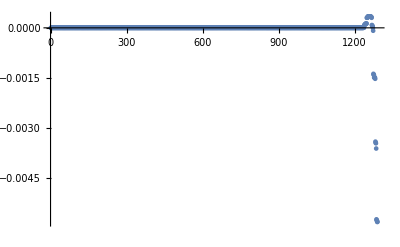

```mathematica
ListPlot["BETXBEAT"/.test,PlotRange->All]
```

### Function definition: LHCSqueezeStrFNAnalysis

```mathematica
LHCSqueezeStrFNAnalysis::usage="LHCSqueezeStrFNAnalysis[sqdir] returns a set containing a list of the beta star values at the different points, a list of the strength names involved in the squeeze, a list of rules for these strenghtnames to their value at the different squeeze points, a plot of the the beta star values at each step and finally an interpolation function for each of the strengthnames."

LHCSqueezeStrFNAnalysis[sqdir_]:=Module[{sqfiles,betaStrFile,sqstrnames,sqex},
sqfiles=FileNames["*.str",sqdir];
betaStrFile[sqfile_String]:=ToExpression[StringReplace[sqfile,__~~"_"~~f__~~".str":>f]];
sqstrnames=Cases[madLHCStrengthSettings[First[sqfiles]],MADset[k1_String,_]|MADsetDelayed[k1_String,_]->k1,∞];
sqex=LHCFilterSqueeze[sqfiles,sqstrnames,(sqstrnames[[1]]/.#1)>(sqstrnames[[1]]/.#2)&];
{Reverse[Sort[Flatten[ToExpression[betaStrFile/@sqfiles]],#2>#1&]],
sqstrnames,
sqex,
SqueezeInterpolation[sqex,#]&/@sqstrnames(*,
ListPlot["BETA.IP2"/.sqex,AxesLabel->{"Step","β^*[m]"}]*)
}
]
```

LHCSqueezeStrFNAnalysis[sqdir] returns a set containing a list of the beta star values at the different points, a list of the strength names involved in the squeeze, a list of rules for these strenghtnames to their value at the different squeeze points, a plot of the the beta star values at each step and finally an interpolation function for each of the strengthnames.

### Function test: LHCSqueezeStrFNAnalysis + additional plot fo the strength evolution of a selection of the quadrupoles involved in the squeeze

```mathematica
sqdataana=LHCSqueezeStrFNAnalysis[FileNameJoin[{$madLHCOpticsDatabaseStem,"V6.503","IR2","7.0TeV"}]];
```

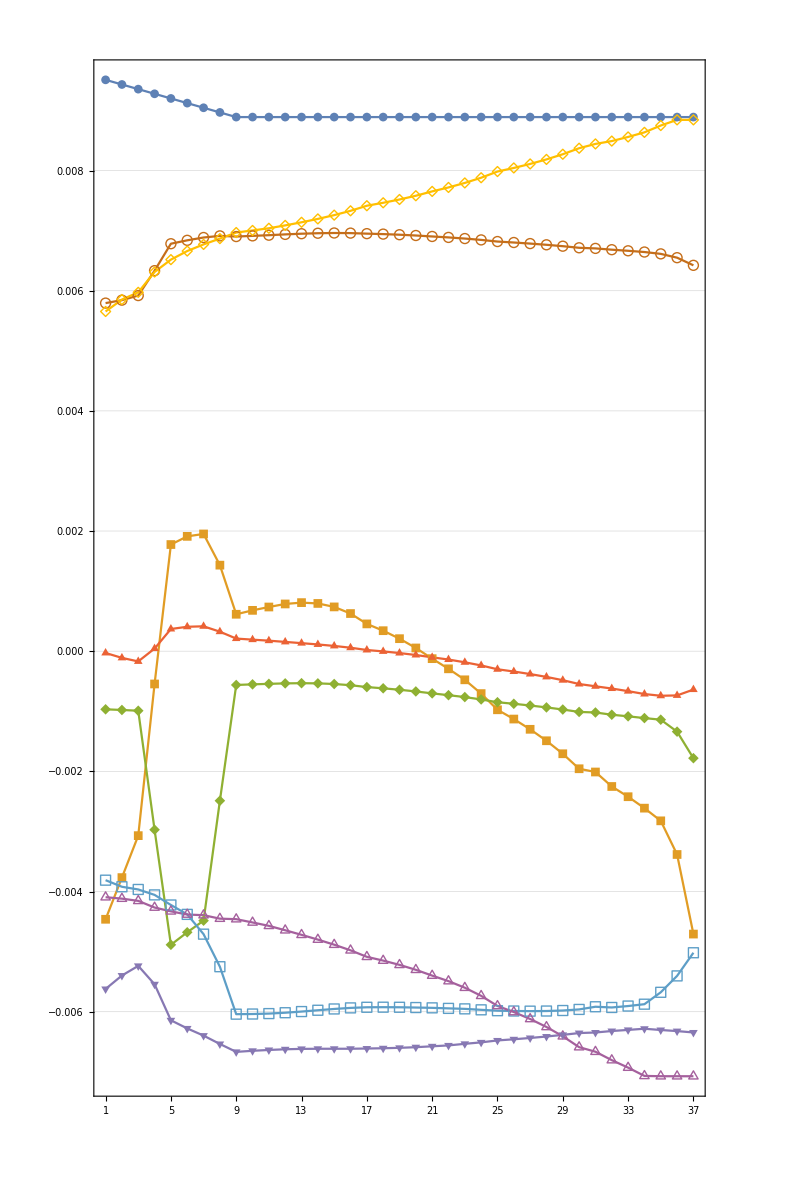

```mathematica
FilterSqueezePlot[sqdataana[[3]],sqdataana[[2,4;;12]]]
```

### Function definition : LHCSqueezeBBSimple

Maybe below change the name LHCSqueezeSeqBeamProcesStepInterpolat to LHCSqueezeSeqBeamProcesCompare such that the  [[1]] can be eliminated in the defintion of modlopt which would make more sense.

```mathematica
LHCSqueezeBBSimple::usage="LHCSqueezeBBSimple[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesCompare,mod] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{\"SqueezeIndex\"→n,\"QDIFF\"→dq,\"DQDIFF\"→ddq,\"BETXBEATMean\"→bxbMean,\"BETYBEATMean\"→bybMean,\"BETXBEATRMS\"→bxbRMS,\"BETYBEATRMS\"→bybRMS,\"BETXBEATPEAK\"→Max[Abs[bxb]],\"BETYBEATPEAK\"→Max[Abs[byb]],
\"DXDIFFMean\"→dxdMean,\"DYDIFFMean\"→dydMean,\"DXDIFFRMS\"→dxdRMS,\"DYDIFFRMS\"→dydRMS,\"DXDIFFPEAK\"→Max[Abs[dxdiff]],\"DYDIFFPEAK\"→Max[Abs[dydiff]],
\"BETXBEAT\"→bxb,\"BETYBEAT\"→byb,\"DXDIFF\"→dxdiff,\"DYDIFF\"→dydiff, \"MUXDIFF\"→dmux,\"MUYDIFF\"→dmuy}"

LHCSqueezeBBSimple[LHCSqueezeSeqBeamProcesStep_,LHCSqueezeSeqBeamProcesStepInterpolat_,mod_]:=Module[{OptsTableOriginal,OptsTableInterpolat,modlopt,bxb,byb,modlref,bxbMean,bybMean,dxdMean,dydMean,dxdiff,dydiff,bxbRMS,bybRMS,dxdRMS,dydRMS,dq,ddq,dmux,dmuy,s,q,dqq},

If[StringTake[mod,-2]=="B1",OptsTableOriginal="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesStep,OptsTableOriginal="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesStep];

If[StringTake[mod,-2]=="B1",OptsTableInterpolat="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesStepInterpolat,OptsTableInterpolat="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesStepInterpolat];

modlopt=mfsOpticsRange[Get[OptsTableInterpolat[[1]]],LHCModule[mod]];
modlref=mfsOpticsRange[Get[OptsTableOriginal],LHCModule[mod]];
s=mfsColumn[modlopt,"S"];
bxb=mfsColumn[modlopt,"BETX"]/mfsColumn[modlref,"BETX"]-1;
byb=mfsColumn[modlopt,"BETY"]/mfsColumn[modlref,"BETY"]-1;
dxdiff=mfsColumn[modlopt,"DX"]-mfsColumn[modlref,"DX"];
dydiff=mfsColumn[modlopt,"DY"]-mfsColumn[modlref,"DY"];
dmux=mfsColumn[modlopt,"MUX"]-mfsColumn[modlref,"MUX"];
dmuy=mfsColumn[modlopt,"MUY"]-mfsColumn[modlref,"MUY"];
bxbMean=Mean[bxb];bybMean=Mean[byb];
dxdMean=Mean[dxdiff];dydMean=Mean[dydiff];
bxbRMS=StandardDeviation[bxb];bybRMS=StandardDeviation[byb];
dxdRMS=StandardDeviation[dxdiff];dydRMS=StandardDeviation[dydiff];
q=mfsKeyValue[modlopt,{"Q1","Q2"}];
dqq=mfsKeyValue[modlref,{"DQ1","DQ2"}];
dq=mfsKeyValue[modlopt,{"Q1","Q2"}]-mfsKeyValue[modlref,{"Q1","Q2"}];ddq=mfsKeyValue[modlopt,{"DQ1","DQ2"}]-mfsKeyValue[modlref,{"DQ1","DQ2"}];

{"Q"->q,"DQ"->dqq,"QDIFF"->dq,"DQDIFF"->ddq,"BETXBEATMean"->bxbMean,"BETYBEATMean"->bybMean,"BETXBEATRMS"->bxbRMS,"BETYBEATRMS"->bybRMS,"BETXBEATPEAK"->Max[Abs[bxb]],"BETYBEATPEAK"->Max[Abs[byb]],
"DXDIFFMean"->dxdMean,"DYDIFFMean"->dydMean,"DXDIFFRMS"->dxdRMS,"DYDIFFRMS"->dydRMS,"DXDIFFPEAK"->Max[Abs[dxdiff]],"DYDIFFPEAK"->Max[Abs[dydiff]],
"BETXBEAT"->Transpose[{s,bxb}],"BETYBEAT"->Transpose[{s,byb}],"DXDIFF"->Transpose[{s,dxdiff}],"DYDIFF"->Transpose[{s,dydiff}], "MUXDIFF"->Transpose[{s,dmux}],"MUYDIFF"->Transpose[{s,dmuy}]}]
```

LHCSqueezeBBSimple[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesCompare,mod] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{"SqueezeIndex"→n,"QDIFF"→dq,"DQDIFF"→ddq,"BETXBEATMean"→bxbMean,"BETYBEATMean"→bybMean,"BETXBEATRMS"→bxbRMS,"BETYBEATRMS"→bybRMS,"BETXBEATPEAK"→Max[Abs[bxb]],"BETYBEATPEAK"→Max[Abs[byb]],
"DXDIFFMean"→dxdMean,"DYDIFFMean"→dydMean,"DXDIFFRMS"→dxdRMS,"DYDIFFRMS"→dydRMS,"DXDIFFPEAK"→Max[Abs[dxdiff]],"DYDIFFPEAK"→Max[Abs[dydiff]],
"BETXBEAT"→bxb,"BETYBEAT"→byb,"DXDIFF"→dxdiff,"DYDIFF"→dydiff, "MUXDIFF"→dmux,"MUYDIFF"→dmuy}

### Function definition : LHCSqueezeBBElimInterpolat

```mathematica
LHCSqueezeBBElimInterpolat::usage="LHCSqueezeBetaBeatingModule[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesInterpolat,mod,n] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{\"SqueezeIndex\"→n,\"QDIFF\"→dq,\"DQDIFF\"→ddq,\"BETXBEATMean\"→bxbMean,\"BETYBEATMean\"→bybMean,\"BETXBEATRMS\"→bxbRMS,\"BETYBEATRMS\"→bybRMS,\"BETXBEATPEAK\"→Max[Abs[bxb]],\"BETYBEATPEAK\"→Max[Abs[byb]],
\"DXDIFFMean\"→dxdMean,\"DYDIFFMean\"→dydMean,\"DXDIFFRMS\"→dxdRMS,\"DYDIFFRMS\"→dydRMS,\"DXDIFFPEAK\"→Max[Abs[dxdiff]],\"DYDIFFPEAK\"→Max[Abs[dydiff]],
\"BETXBEAT\"→bxb,\"BETYBEAT\"→byb,\"DXDIFF\"→dxdiff,\"DYDIFF\"→dydiff, \"MUXDIFF\"→dmux,\"MUYDIFF\"→dmuy}"

LHCSqueezeBBElimInterpolat[LHCSqueezeSeqBeamProcesOriginal_,LHCSqueezeSeqBeamProcesInterpolat_,mod_,n_]:=Module[{OptsTableOriginal,OptsTableInterpolat,modlopt,bxb,byb,modlref,bxbMean,bybMean,dxdMean,dydMean,dxdiff,dydiff,bxbRMS,bybRMS,dxdRMS,dydRMS,dq,ddq,dmux,dmuy,s,q,dqq},

If[StringTake[mod,-2]=="B1",OptsTableOriginal="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesOriginal,OptsTableOriginal="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesOriginal];

If[StringTake[mod,-2]=="B1",OptsTableInterpolat="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesInterpolat,OptsTableInterpolat="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesInterpolat];

modlopt=mfsOpticsRange[Get[OptsTableInterpolat[[n]]],LHCModule[mod]];
modlref=mfsOpticsRange[Get[OptsTableOriginal[[n+1]]],LHCModule[mod]];
s=mfsColumn[modlopt,"S"];

bxb=mfsColumn[modlopt,"BETX"]/mfsColumn[modlref,"BETX"]-1;
byb=mfsColumn[modlopt,"BETY"]/mfsColumn[modlref,"BETY"]-1;
dxdiff=mfsColumn[modlopt,"DX"]-mfsColumn[modlref,"DX"];
dydiff=mfsColumn[modlopt,"DY"]-mfsColumn[modlref,"DY"];
dmux=mfsColumn[modlopt,"MUX"]-mfsColumn[modlref,"MUX"];
dmuy=mfsColumn[modlopt,"MUY"]-mfsColumn[modlref,"MUY"];
bxbMean=Mean[bxb];bybMean=Mean[byb];
dxdMean=Mean[dxdiff];dydMean=Mean[dydiff];
bxbRMS=StandardDeviation[bxb];bybRMS=StandardDeviation[byb];
dxdRMS=StandardDeviation[dxdiff];dydRMS=StandardDeviation[dydiff];
q=mfsKeyValue[modlopt,{"Q1","Q2"}];
dqq=mfsKeyValue[modlref,{"DQ1","DQ2"}];
dq=mfsKeyValue[modlopt,{"Q1","Q2"}]-mfsKeyValue[modlref,{"Q1","Q2"}];ddq=mfsKeyValue[modlopt,{"DQ1","DQ2"}]-mfsKeyValue[modlref,{"DQ1","DQ2"}];

{"SqueezeIndex"->n,"Q"->q,"DQ"->dqq,"QDIFF"->dq,"DQDIFF"->ddq,"BETXBEATMean"->bxbMean,"BETYBEATMean"->bybMean,"BETXBEATRMS"->bxbRMS,"BETYBEATRMS"->bybRMS,"BETXBEATPEAK"->Max[Abs[bxb]],"BETYBEATPEAK"->Max[Abs[byb]],
"DXDIFFMean"->dxdMean,"DYDIFFMean"->dydMean,"DXDIFFRMS"->dxdRMS,"DYDIFFRMS"->dydRMS,"DXDIFFPEAK"->Max[Abs[dxdiff]],"DYDIFFPEAK"->Max[Abs[dydiff]],
"BETXBEAT"->Transpose[{s,bxb}],"BETYBEAT"->Transpose[{s,byb}],"DXDIFF"->Transpose[{s,dxdiff}],"DYDIFF"->Transpose[{s,dydiff}], "MUXDIFF"->Transpose[{s,dmux}],"MUYDIFF"->Transpose[{s,dmuy}]}]
```

LHCSqueezeBetaBeatingModule[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesInterpolat,mod,n] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{"SqueezeIndex"→n,"QDIFF"→dq,"DQDIFF"→ddq,"BETXBEATMean"→bxbMean,"BETYBEATMean"→bybMean,"BETXBEATRMS"→bxbRMS,"BETYBEATRMS"→bybRMS,"BETXBEATPEAK"→Max[Abs[bxb]],"BETYBEATPEAK"→Max[Abs[byb]],
"DXDIFFMean"→dxdMean,"DYDIFFMean"→dydMean,"DXDIFFRMS"→dxdRMS,"DYDIFFRMS"→dydRMS,"DXDIFFPEAK"→Max[Abs[dxdiff]],"DYDIFFPEAK"→Max[Abs[dydiff]],
"BETXBEAT"→bxb,"BETYBEAT"→byb,"DXDIFF"→dxdiff,"DYDIFF"→dydiff, "MUXDIFF"→dmux,"MUYDIFF"→dmuy}

### Function definition : LHCSqueezeBBSimpleBPM

```mathematica
LHCSqueezeBBSimpleBPM::usage="LHCSqueezeBBSimple[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesInterpolat,mod] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) at the BPMs in the main arcs (places that can be correlated with measurements)when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{\"SqueezeIndex\"→n,\"QDIFF\"→dq,\"DQDIFF\"→ddq,\"BETXBEATMean\"→bxbMean,\"BETYBEATMean\"→bybMean,\"BETXBEATRMS\"→bxbRMS,\"BETYBEATRMS\"→bybRMS,\"BETXBEATPEAK\"→Max[Abs[bxb]],\"BETYBEATPEAK\"→Max[Abs[byb]],
\"DXDIFFMean\"→dxdMean,\"DYDIFFMean\"→dydMean,\"DXDIFFRMS\"→dxdRMS,\"DYDIFFRMS\"→dydRMS,\"DXDIFFPEAK\"→Max[Abs[dxdiff]],\"DYDIFFPEAK\"→Max[Abs[dydiff]],
\"BETXBEAT\"→bxb,\"BETYBEAT\"→byb,\"DXDIFF\"→dxdiff,\"DYDIFF\"→dydiff, \"MUXDIFF\"→dmux,\"MUYDIFF\"→dmuy}"

LHCSqueezeBBSimpleBPM[LHCSqueezeSeqBeamProcesStep_,LHCSqueezeSeqBeamProcesStepInterpolat_,mod_]:=Module[{OptsTableOriginal,OptsTableInterpolat,modlopt,bxb,byb,modlref,bxbMean,bybMean,dxdMean,dydMean,dxdiff,dydiff,bxbRMS,bybRMS,dxdRMS,dydRMS,dq,ddq,dmux,dmuy,s,q,dqq,modloptreduced,modlrefreduced},

If[StringTake[mod,-2]=="B1",OptsTableOriginal="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesStep,OptsTableOriginal="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesStep];

If[StringTake[mod,-2]=="B1",OptsTableInterpolat="LHCB1OpticsFile"/.LHCSqueezeSeqBeamProcesStepInterpolat,OptsTableInterpolat="LHCB2OpticsFile"/.LHCSqueezeSeqBeamProcesStepInterpolat];

modlopt=mfsOpticsRange[Get[OptsTableInterpolat[[1]]],LHCModule[mod]];
modlref=mfsOpticsRange[Get[OptsTableOriginal],LHCModule[mod]];
modloptreduced=mfsSelect[modlopt,StringTake[mfsColumnValue[modlopt,#,"NAME"],{1,3}]=="BPM"&& ToExpression[StringDrop[StringDrop[mfsColumnValue[modlopt,#,"NAME"],4],-5]]>13&];
modlrefreduced=mfsSelect[modlref,StringTake[mfsColumnValue[modlref,#,"NAME"],{1,3}]=="BPM"&& ToExpression[StringDrop[StringDrop[mfsColumnValue[modlref,#,"NAME"],4],-5]]>13&];
s=mfsColumn[modloptreduced,"S"];
bxb=mfsColumn[modloptreduced,"BETX"]/mfsColumn[modlrefreduced,"BETX"]-1;
byb=mfsColumn[modloptreduced,"BETY"]/mfsColumn[modlrefreduced,"BETY"]-1;
dxdiff=mfsColumn[modloptreduced,"DX"]-mfsColumn[modlrefreduced,"DX"];
dydiff=mfsColumn[modloptreduced,"DY"]-mfsColumn[modlrefreduced,"DY"];
dmux=mfsColumn[modloptreduced,"MUX"]-mfsColumn[modlrefreduced,"MUX"];
dmuy=mfsColumn[modloptreduced,"MUY"]-mfsColumn[modlrefreduced,"MUY"];
bxbMean=Mean[bxb];bybMean=Mean[byb];
dxdMean=Mean[dxdiff];dydMean=Mean[dydiff];
bxbRMS=StandardDeviation[bxb];bybRMS=StandardDeviation[byb];
dxdRMS=StandardDeviation[dxdiff];dydRMS=StandardDeviation[dydiff];
q=mfsKeyValue[modlopt,{"Q1","Q2"}];
dqq=mfsKeyValue[modlref,{"DQ1","DQ2"}];
dq=mfsKeyValue[modlopt,{"Q1","Q2"}]-mfsKeyValue[modlref,{"Q1","Q2"}];ddq=mfsKeyValue[modlopt,{"DQ1","DQ2"}]-mfsKeyValue[modlref,{"DQ1","DQ2"}];

{"Q"->q,"DQ"->dqq,"QDIFF"->dq,"DQDIFF"->ddq,"BETXBEATMean"->bxbMean,"BETYBEATMean"->bybMean,"BETXBEATRMS"->bxbRMS,"BETYBEATRMS"->bybRMS,"BETXBEATPEAK"->Max[Abs[bxb]],"BETYBEATPEAK"->Max[Abs[byb]],
"DXDIFFMean"->dxdMean,"DYDIFFMean"->dydMean,"DXDIFFRMS"->dxdRMS,"DYDIFFRMS"->dydRMS,"DXDIFFPEAK"->Max[Abs[dxdiff]],"DYDIFFPEAK"->Max[Abs[dydiff]],
"BETXBEAT"->Transpose[{s,bxb}],"BETYBEAT"->Transpose[{s,byb}],"DXDIFF"->Transpose[{s,dxdiff}],"DYDIFF"->Transpose[{s,dydiff}], "MUXDIFF"->Transpose[{s,dmux}],"MUYDIFF"->Transpose[{s,dmuy}]}]
```

LHCSqueezeBBSimple[LHCSqueezeSeqBeamProcesOriginal,LHCSqueezeSeqBeamProcesInterpolat,mod] Returns a set of rules containing all relevant information about the changes in the optics relevant for the squeeze sequence (i.e. beta beating, dispersion differences,...) at the BPMs in the main arcs (places that can be correlated with measurements)when replacing squeeze points by interpolated values. Note that this function assumes that LHCCreateAdditionalModules[] has been loaded.  Assumes that module names end either with
{"SqueezeIndex"→n,"QDIFF"→dq,"DQDIFF"→ddq,"BETXBEATMean"→bxbMean,"BETYBEATMean"→bybMean,"BETXBEATRMS"→bxbRMS,"BETYBEATRMS"→bybRMS,"BETXBEATPEAK"→Max[Abs[bxb]],"BETYBEATPEAK"→Max[Abs[byb]],
"DXDIFFMean"→dxdMean,"DYDIFFMean"→dydMean,"DXDIFFRMS"→dxdRMS,"DYDIFFRMS"→dydRMS,"DXDIFFPEAK"→Max[Abs[dxdiff]],"DYDIFFPEAK"→Max[Abs[dydiff]],
"BETXBEAT"→bxb,"BETYBEAT"→byb,"DXDIFF"→dxdiff,"DYDIFF"→dydiff, "MUXDIFF"→dmux,"MUYDIFF"→dmuy}

Plotting Functions

These functions assume that the Beam Process has been fed to the LHCBeamBeamOptics function.

## General Functions

```mathematica
SizeMultiplier::usage="This functions just enlarges the plots of a set of plots, can be handy whene the standard output of some plotting function generates a long list of small plots."

SizeMultiplier[x_,m1_,m2_] :=Style[x,ImageSizeMultipliers->{m1,m2}]
```

This functions just enlarges the plots of a set of plots, can be handy whene the standard output of some plotting function generates a long list of small plots.

## Separation plots

### Function Definition : LHCSepXYPlots

```mathematica
LHCbeambeamdataPlots[optcbb_mfs,bbq_String,dsbb_,smin_,smax_,beamlinegrahppos_,opts:OptionsPattern[]]:=Module[{ff,fc,fmin,fmax,wid},
ff=mfsRow[optcbb,{"S",bbq}];fc=mfsColumn[optcbb,bbq];fmin=Min[Re[fc]];fmax=Max[Re[fc]];wid=(Max[Re[fc]]-Min[Re[fc]])/8.;
SetOptions[BeamLineElementGraphic,FilterRules[{opts},Options[BeamLineElementGraphic]]];
ListPlot[ff,(*PlotRange->{fmin-1.5 wid,fmax+3.5 wid},*)AxesLabel->{"s/m",mfsOpticsNotation[bbq]},FilterRules[{opts},Options[ListPlot]],Epilog->{{Directive[Dashed,Black],(Line[{{#1,-beamlinegrahppos},{#1,beamlinegrahppos}}]&)/@sbeambeam[optcbb,dsbb,smin,smax]},Translate[mfsOpticsBeamLineGraphics[optcbb/."K0L"->"ANGLE"],{0,beamlinegrahppos}]}]
]
```

```mathematica
LHCbbdataPlots::usage="Returns the plots of the Beam-Beam SEPRSIGXY1 for beam 1 and beam2. Has an option to set the vertical position of the BeamLineGraphics and also all the options of ListPlot are available."

Options[LHCbbdataPlots]=Flatten[{beamlinegrahppos->60,parampos->{100,60},Options[ListPlot],Options[BeamLineElementGraphic]}];

LHCbbdataPlots[scan_,IR_String,bbvar1_,bbvar2_,opts:OptionsPattern[]]:=
Module[{},{
LHCbeambeamdataPlots[IR/.(Get["LHCB1BeamBeamOpticsFile"/.#]),bbvar1,dsbb,-100,100,OptionValue[beamlinegrahppos],FilterRules[{opts},Options[ListPlot]],FilterRules[{opts},Options[BeamLineElementGraphic]],Prolog->Inset[{{Style["ENERGY = "<>ToString["ENERGY1"/.Get["BeamProcessOptions"/.#]]<>" GeV",16]},{Style["SEPX = "<>ToString[Flatten[Select[Transpose[mfsColumn["IR2"/.(Get["LHCB1BeamBeamOpticsFile"/.#]),{"NAME","SEPX"}]],#[[1]]=="IP"<>StringTake[IR,-1]&]][[2]]]<>" m",16]}},OptionValue[parampos]]]&/@scan,
LHCbeambeamdataPlots[IR/.(Get["LHCB2BeamBeamOpticsFile"/.#]),bbvar2,dsbb,-100,100,OptionValue[beamlinegrahppos],FilterRules[{opts},Options[ListPlot]],Options[BeamLineElementGraphic],Prolog->Inset[{{Style["ENERGY = "<>ToString["ENERGY1"/.Get["BeamProcessOptions"/.#]]<>" GeV",16]},{Style["SEPX = "<>ToString[Flatten[Select[Transpose[mfsColumn["IR2"/.(Get["LHCB1BeamBeamOpticsFile"/.#]),{"NAME","SEPX"}]],#[[1]]=="IP"<>StringTake[IR,-1]&]][[2]]]<>" m",16]}},OptionValue[parampos]]]&/@scan}
]
```

Returns the plots of the Beam-Beam SEPRSIGXY1 for beam 1 and beam2. Has an option to set the vertical position of the BeamLineGraphics and also all the options of ListPlot are available.

### Function test : LHCSepXYPlots

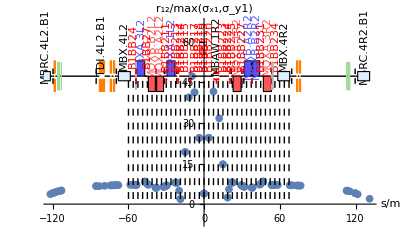
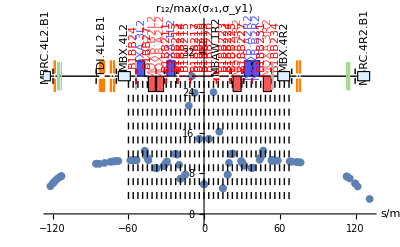
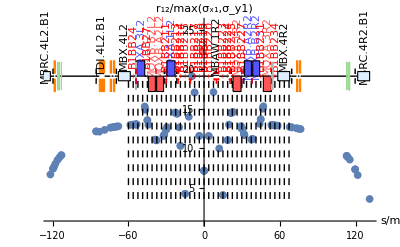
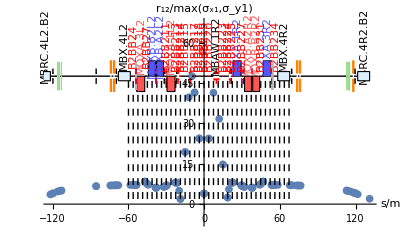
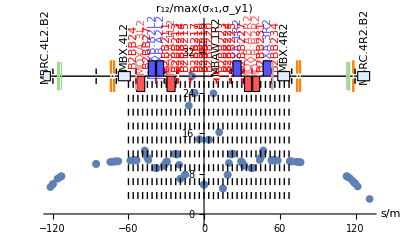
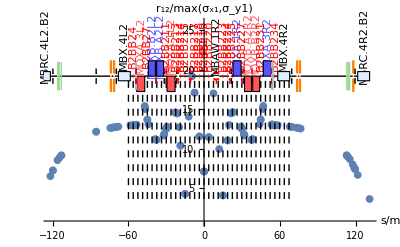

```mathematica
SizeMultiplier[#,1,2]&/@LHCSepXYPlots[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;3]]]
```

## IR Matching - Squeeze Plots

```mathematica
MADtwissColumns["MatchFunctions"]
```

{BETX,ALFX,MUX,BETY,ALFY,MUY,DX,DPX,DY,DPY}

### Function definition : LHCSqueezeMatchingVarPlots

```mathematica
LHCModuleCreate["LHC.B1","LHCB1",{"IP6","LHCB1IP6_P_"}]
```

{{IP6,0},{LHCB1IP6_P_,26658.9}}

```mathematica
LHCModuleCreate["LHC.B2","LHCB2",{"IP6","LHCB2IP6_P_"}]
```

{{IP6,0},{LHCB2IP6_P_,26658.9}}

```mathematica
LHCSqueezeMatchingVarPlots::usage="LHCSqueezeMatchingVarPlots[SqueezeBeamProcess,beam,mod,dir] returns a list of plots of which the first is a plot of the tunes and chromaticity follow by a set of mfsOpticsClassicBeamLinePlots and the others are the variables defined in MADtwissColumns[\"MatchFunctions\"]. All plots are also exported as *.png files to the directory specified in the options by the user if the export option is set to true (defaults are the notebook directory and true)"

Options[LHCSqueezeMatchingVarPlots]= {export->True,directory->NotebookDirectory[]};

LHCSqueezeMatchingVarPlots[SqueezeBeamProcess_,beam_Integer,mod_String,opts:OptionsPattern[]] :=Module[{optfn,data,tunesPlot,chromaticityPlot,beamlinePlot,phasexPlot,phaseyPlot,alfxPlot,alfyPlot,dxPlot,dyPlot,dpxPlot,dpyPlot,tunesPlotfn,chromaticityPlotfn,beamlinePlotfn,phasexPlotfn,phaseyPlotfn,alfxPlotfn,alfyPlotfn,dxPlotfn,dyPlotfn,dpxPlotfn,dpyPlotfn,dir},
dir=OptionValue[directory];
optfn = "LHCB"<>ToString[beam]<>"OpticsFile";
data =mfsOpticsRange[Get[optfn/.#],LHCModule[mod]]&/@SqueezeBeamProcess;

SetOptions[BeamLineElementGraphic,{BeamLineGraphicWidth->40,BeamLineGraphicDot->0.3,BeamLineGraphicLabelLength->20.}];
tunesPlotfn=FileNameJoin[{dir,"tunesPlot.png"}];
chromaticityPlotfn=FileNameJoin[{dir,"chromaticityPlot.png"}];beamlinePlotfn=FileNameJoin[{dir,"beamlinePlot.png"}];
phasexPlotfn= FileNameJoin[{dir,"phasexPlotf.png"}];phaseyPlotfn= FileNameJoin[{dir,"phaseyPlotf.png"}];alfxPlotfn= FileNameJoin[{dir,"alfxPlot.png"}];alfyPlotfn= FileNameJoin[{dir,"alfyPlot.png"}];dxPlotfn= FileNameJoin[{dir,"dxPlot.png"}];dyPlotfn= FileNameJoin[{dir,"dyPlot.png"}];dpxPlotfn= FileNameJoin[{dir,"dpxPlot.png"}];
dpyPlotfn= FileNameJoin[{dir,"dpyPlot.png"}];

tunesPlot=ListLinePlot[{Transpose[{Range[Length[data]],mfsKeyValue[#,{"Q1"}][[1]]&/@data}],Transpose[{Range[Length[data]],mfsKeyValue[#,{"Q2"}][[1]]&/@data}]},PlotLabel->" Q1/Q2 (squeeze steps)"];


chromaticityPlot=ListLinePlot[{Transpose[{Range[Length[data]],mfsKeyValue[#,{"DQ1"}][[1]]&/@data}],Transpose[{Range[Length[data]],mfsKeyValue[#,{"DQ2"}][[1]]&/@data}]},PlotLabel->" DQ1/DQ2 (squeeze steps)"];


beamlinePlot=mfsOpticsClassicBeamLinePlot[#,PlotLabel->mod <>" Squeeze Step " <> ToString[Flatten[Position[data,#]]]]&/@data;


(*phase *)
phasexPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,y}&/@mfsRow[#,{"S","MUX","MUY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","MUX","MUY"}]&/@data]],Below],PlotLabel->mod <>" MUX (squeeze steps)"];


phaseyPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,z}&/@mfsRow[#,{"S","MUX","MUY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","MUX","MUY"}]&/@data]],Below],PlotLabel->mod <>" MUY (squeeze steps)"];


(* alfa *)
alfxPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,y}&/@mfsRow[#,{"S","ALFX","ALFY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","ALFX","ALFY"}]&/@data]],Below],PlotLabel->mod <>" ALFX (squeeze steps)"];


alfyPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,z}&/@mfsRow[#,{"S","ALFX","ALFY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","ALFX","ALFY"}]&/@data]],Below],PlotLabel->mod <>" ALFY (squeeze steps)"];


(*dispersion*)
dxPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,y}&/@mfsRow[#,{"S","DX","DY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","DX","DY"}]&/@data]],Below],PlotLabel->mod <>" DX (squeeze steps)",PlotRange->All];


dyPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,z}&/@mfsRow[#,{"S","DX","DY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","DX","DY"}]&/@data]],Below],PlotLabel->mod <>" DY (squeeze steps)",PlotRange->All];


(*angles*)
dpxPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,y}&/@mfsRow[#,{"S","DPX","DPY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","DPX","DPY"}]&/@data]],Below],PlotLabel->"DX (squeeze steps)",PlotRange->All];

dpyPlot=ListLinePlot[#/.{x_,y_,z_}:>{x,z}&/@mfsRow[#,{"S","DPX","DPY"}]&/@data,PlotLegends->Placed[Range[Length[mfsRow[#,{"S","DPX","DPY"}]&/@data]],Below],PlotLabel->"DY (squeeze steps)",PlotRange->All];

If[OptionValue[export],Export[tunesPlotfn,tunesPlot];Export[chromaticityPlotfn,chromaticityPlot];Export[beamlinePlotfn,beamlinePlot];Export[phasexPlotfn,phasexPlot];Export[phaseyPlotfn,phaseyPlot];Export[alfxPlotfn,alfxPlot];Export[alfyPlotfn,alfyPlot];
Export[dxPlotfn,dxPlot];Export[dyPlotfn,dyPlot];Export[dpxPlotfn,dpxPlot];Export[dpyPlotfn,dpyPlot];,
];
{tunesPlot,chromaticityPlot,beamlinePlot,phasexPlot,phaseyPlot,alfxPlot,alfyPlot,dxPlot,dyPlot,dpxPlot,dpyPlot}]
```

LHCSqueezeMatchingVarPlots[SqueezeBeamProcess,beam,mod,dir] returns a list of plots of which the first is a plot of the tunes and chromaticity follow by a set of mfsOpticsClassicBeamLinePlots and the others are the variables defined in MADtwissColumns["MatchFunctions"]. All plots are also exported as *.png files to the directory specified in the options by the user if the export option is set to true (defaults are the notebook directory and true)

### Function test : LHCSqueezeMatchingVarPlots

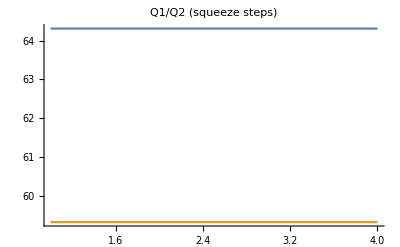
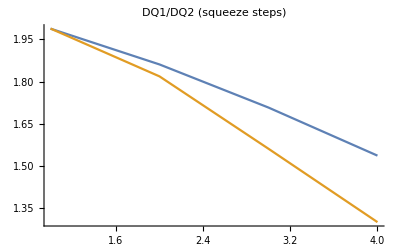
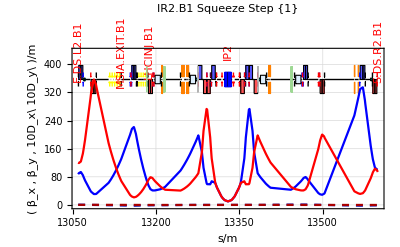
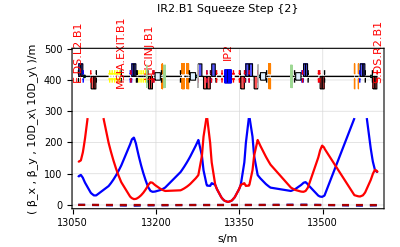
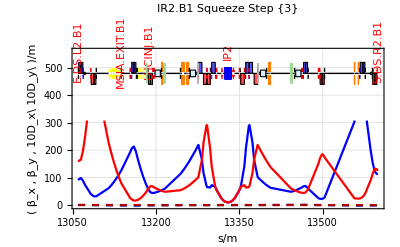
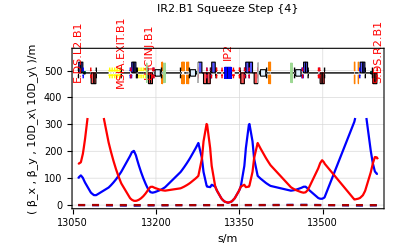
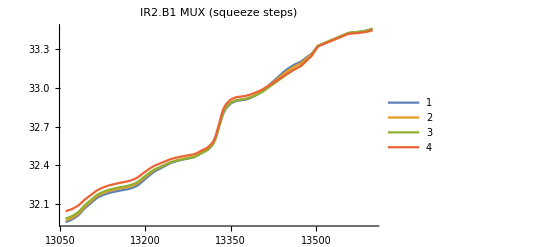
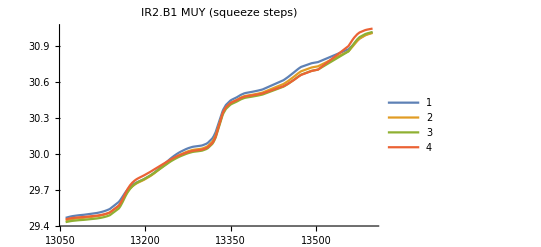

```mathematica
LHCSqueezeMatchingVarPlots[LHCBeamSqueezeOpticsOutput[[1;;4]],1,"IR2.B1",export->True,directory->workDir]
```

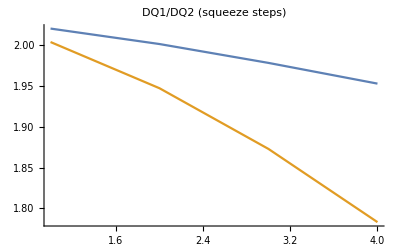
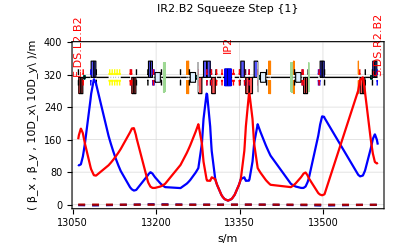
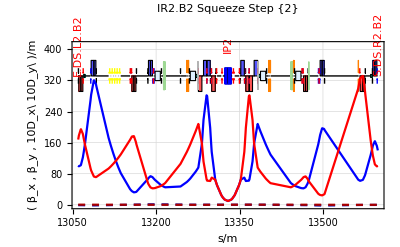
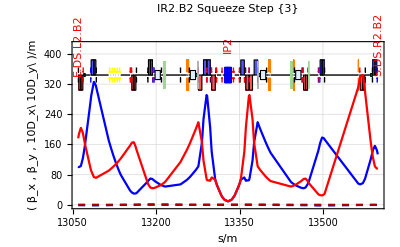
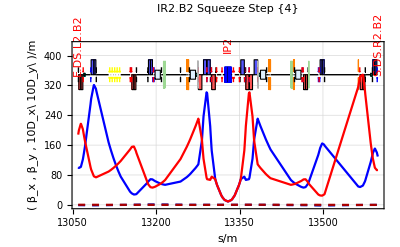
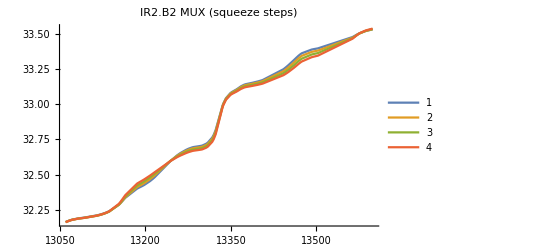
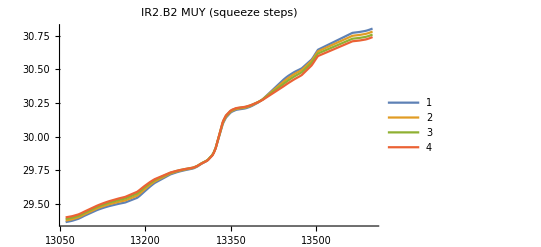
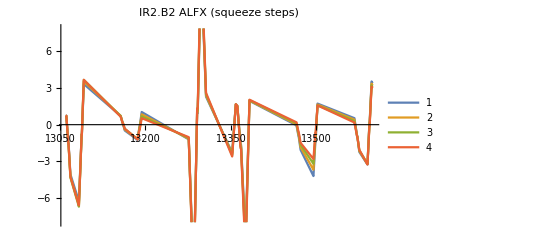
{-Graphics-,-Graphics-,{-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LHCSqueezeMatchingVarPlots[LHCBeamSqueezeOpticsOutput[[1;;4]],2,"IR2.B2"]
```

### Function definition : LHCSqueezeMatchingVarIPPlotsfn

```mathematica
LHCSqueezeMatchingVarIPPlotsfn[SqueezeBeamProcess_,dir_]:=Module[{fn,plotset,val},
fn=FileNameJoin[{dir,"MatchingVarIPPlots.m"}];
plotset=#->{LHCSqueezeMatchingVarPlots[SqueezeBeamProcess,1,#<>".B1"],LHCSqueezeMatchingVarPlots[SqueezeBeamProcess,2,#<>".B2"]}&/@{"IR1","IR2","IR5","IR8"};
Put[plotset,fn];
val={"ResultsDirectoryPath"->dir,"MatchingVarIPPlots"->fn};
val
]
```

### Function test : LHCSqueezeMatchingVarIPPlotsfn

```mathematica
workDir
```

C:\Workspaces\ppPhysics2015

```mathematica
LHCSqueezeMatchingVarIPPlotsfn[LHCBeamSqueezeOpticsOutput[[1;;2]],workDir]
```

{ResultsDirectoryPath→C:\Workspaces\ppPhysics2015,MatchingVarIPPlots→C:\Workspaces\ppPhysics2015\MatchingVarIPPlots.m}

## Tune shift plots

### Function Definition : LHCVTuneShiftPlot

```mathematica
LHCVTuneShiftPlot::usage="Returns the plots of the Beam-Beam vertical tune shift for beam 1 and beam 2. Accepts options from BeamLineGraphic and ListPlot augmented with a rule for setting the vertical position of the BeamLineGraphic (beamlinegrahppos→60). "

Options[LHCVTuneShiftPlot] = Flatten[{beamlinegrahppos->60,Options[ListPlot],Options[BeamLineElementGraphic]}];

LHCVTuneShiftPlot[scan_,IR_String,opts:OptionsPattern[]]:=
Module[{},{

beambeamListPlot[IR/.(Get["LHCB1BeamBeamOpticsFile"/.#]),"BBDQY",dsbb,-100,100,OptionValue[beamlinegrahppos],FilterRules[{opts},Options[ListPlot]],FilterRules[{opts},Options[BeamLineElementGraphic]],Prolog->Inset[{{Style["ENERGY = "<>ToString["ENERGY1"/.Get["BeamProcessOptions"/.#]]<>" GeV",16]},{Style["SEPX = "<>ToString[Flatten[Select[Transpose[mfsColumn["IR2"/.(Get["LHCB1BeamBeamOpticsFile"/.#]),{"NAME","SEPX"}]],#[[1]]=="IP"<>StringTake[IR,-1]&]][[2]]]<>" m",16]}},{100,0.00002}]]&/@scan,
beambeamListPlot[IR/.(Get["LHCB1BeamBeamOpticsFile"/.#]),"BBDQY",dsbb,-100,100,OptionValue[beamlinegrahppos],FilterRules[{opts},Options[ListPlot]],FilterRules[{opts},Options[BeamLineElementGraphic]],Prolog->Inset[{{Style["ENERGY = "<>ToString["ENERGY1"/.Get["BeamProcessOptions"/.#]]<>" GeV",16]},{Style["SEPX = "<>ToString[Flatten[Select[Transpose[mfsColumn["IR2"/.(Get["LHCB2BeamBeamOpticsFile"/.#]),{"NAME","SEPX"}]],#[[1]]=="IP"<>StringTake[IR,-1]&]][[2]]]<>" m",16]}},{100,0.00002}]]&/@scan}
]
```

Returns the plots of the Beam-Beam vertical tune shift for beam 1 and beam 2. Accepts options from BeamLineGraphic and ListPlot augmented with a rule for setting the vertical position of the BeamLineGraphic (beamlinegrahppos→60).

### Function test : LHCVTuneShiftPlot

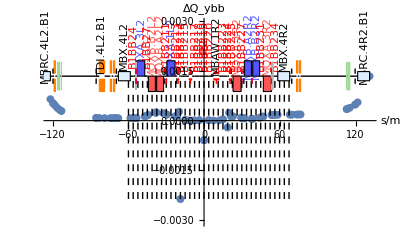
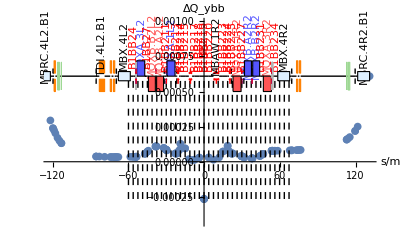
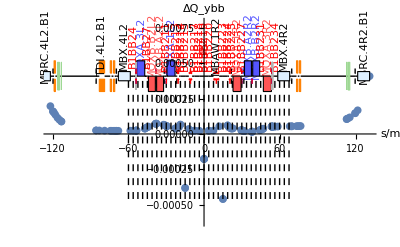
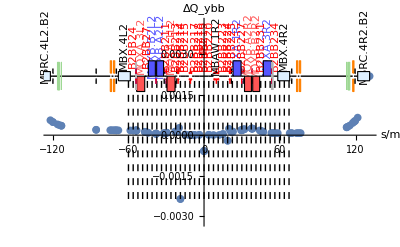
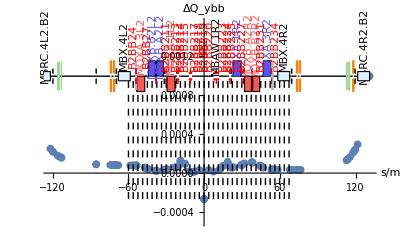
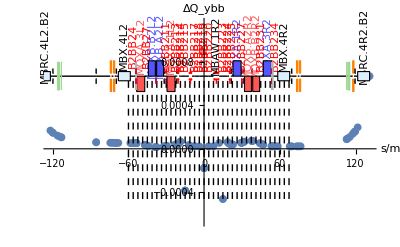

```mathematica
SizeMultiplier[#,1,2]&/@LHCVTuneShiftPlot[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;3]]]
```

### Function Definition : LHCHTuneShiftPlot

```mathematica
LHCHTuneShiftPlot::usage="Returns the plots of the Beam-Beam horizontal tune shift for beam 1 and beam2."

LHCHTuneShiftPlot[scan_]:=
Module[{},{
beambeamListPlot["IR2"/.(Get["LHCB1BeamBeamOpticsFile"/.#]),"BBDQX",dsbb,-100,100]&/@scan,
beambeamListPlot["IR2"/.(Get["LHCB2BeamBeamOpticsFile"/.#]),"BBDQX",dsbb,-100,100]&/@scan}
]
```

Returns the plots of the Beam-Beam horizontal tune shift for beam 1 and beam2.

### Function test : LHCVTuneShiftPlot

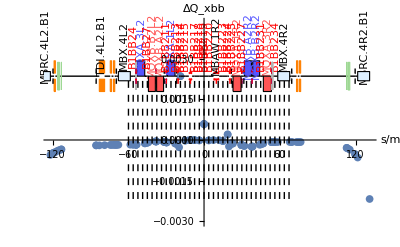
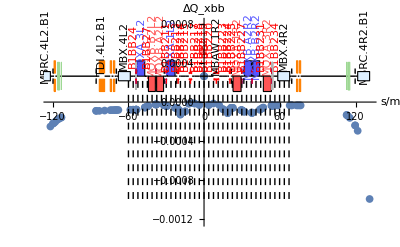
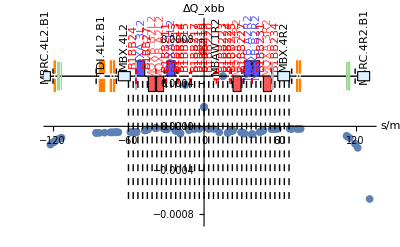
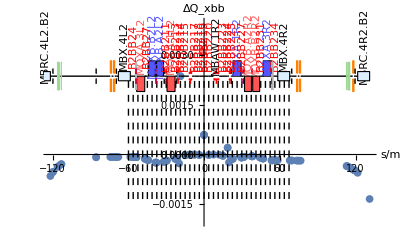
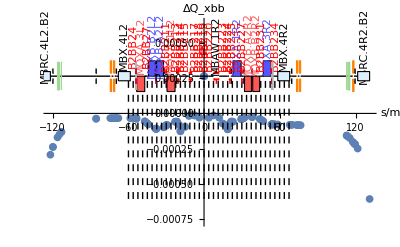
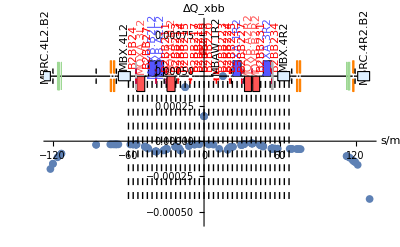

```mathematica
SizeMultiplier[#,1,2]&/@LHCHTuneShiftPlot[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1,1;;3]]]
```

## Corrector Strength Plots

### Function definition : LHCVCorrMAXStrPlot

```mathematica
LHCVCorrMAXStrPlot::usage="LHCVCorrMAXStrPlot[BeamProcess,ProcesParameter,IR] Returns a list of plots of evolutions of the VKICKER maximum strengths through the beam process, where the evolution is with respect to a parameters that varies through the beam process. "

LHCVCorrMAXStrPlot[scan_,ProcesParameter_,IR_String] :=Module[{datab1,datab2,convdatab1,convdatab2},{
datab1=mfsMember[IR/.Get["LHCB1CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER"}]&/@scan;
datab2=mfsMember[IR/.Get["LHCB2CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER"}]&/@scan;
convdatab1=mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","VKICK"}]/.{n_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab1;
convdatab2=mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","VKICK"}]/.{n_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab2;
{ListPlot[Transpose[{ProcesParameter,Flatten[#/.{x_,y_,z_}:>{y},1]}],PlotLabel->#[[2,1]],Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None}]&/@Transpose[convdatab1],
ListPlot[Transpose[{ProcesParameter,Flatten[#/.{x_,y_,z_}:>{y},1]}],PlotLabel->#[[2,1]],Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None}]&/@Transpose[convdatab2]}
}]
```

LHCVCorrMAXStrPlot[BeamProcess,ProcesParameter,IR] Returns a list of plots of evolutions of the VKICKER maximum strengths through the beam process, where the evolution is with respect to a parameters that varies through the beam process.

### Function test : LHCVCorrMAXStrPlot

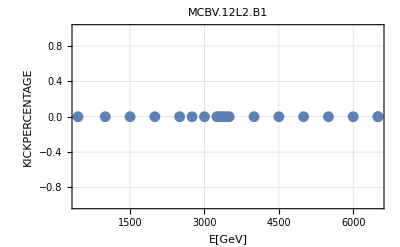
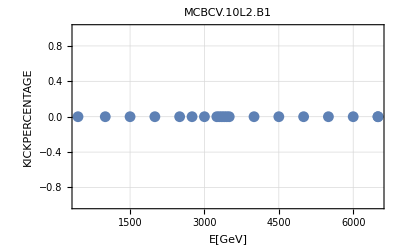
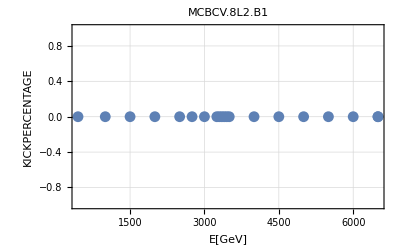
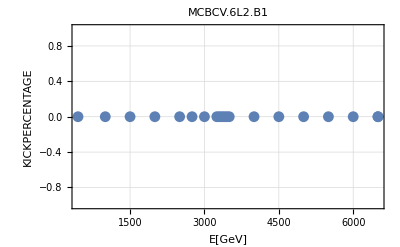
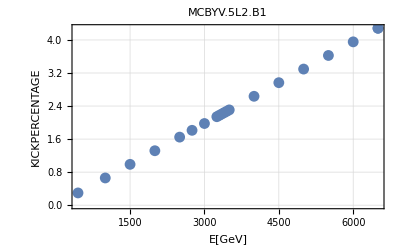
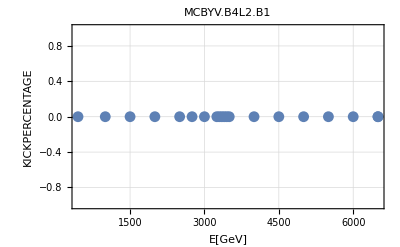
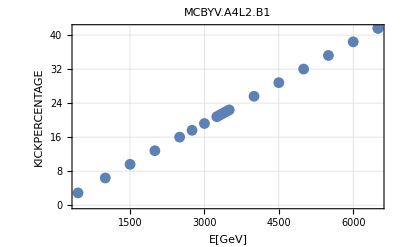
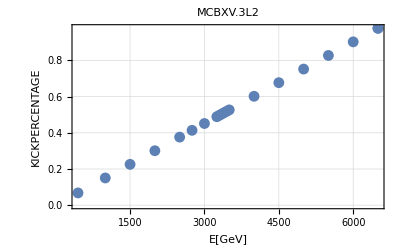
{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
LHCVCorrMAXStrPlot[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1]],EnergyTable,"IR2"]
```

### Function definition : LHCHCorrMAXStrPlot

```mathematica
LHCHCorrMAXStrPlot::usage=" LHCHCorrMAXStrPlot[BeamProcess,ProcesParameter,IR] Returns a list of plots of evolutions of the HKICKER maximum strengths through the beam process, where the evolution is with respect to a parameters that varies through the beam process."

LHCHCorrMAXStrPlot[scan_,ProcesParameter_,IR_String] :=Module[{datab1,datab2,convdatab1,convdatab2},{
datab1=mfsMember[IR/.Get["LHCB1CorrectorStrengthFile"/.#],"KEYWORD",{"HKICKER"}]&/@scan;
datab2=mfsMember[IR/.Get["LHCB2CorrectorStrengthFile"/.#],"KEYWORD",{"HKICKER"}]&/@scan;
convdatab1=mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","HKICK"}]/.{n_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab1;
convdatab2=mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","HKICK"}]/.{n_,x_,y_,v_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab2;
{ListPlot[Transpose[{ProcesParameter,Flatten[#/.{x_,y_,z_}:>{y},1]}],PlotLabel->#[[2,1]],Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None}]&/@Transpose[convdatab1],
ListPlot[Transpose[{ProcesParameter,Flatten[#/.{x_,y_,z_}:>{y},1]}],PlotLabel->#[[2,1]],Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None}]&/@Transpose[convdatab2]}
}]
```

LHCHCorrMAXStrPlot[BeamProcess,ProcesParameter,IR] Returns a list of plots of evolutions of the HKICKER maximum strengths through the beam process, where the evolution is with respect to a parameters that varies through the beam process.

### Function test : LHCHCorrMAXStrPlot

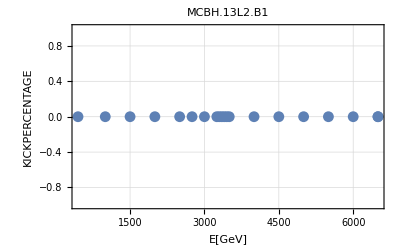
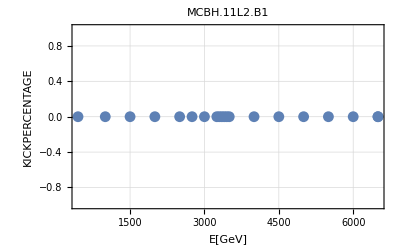
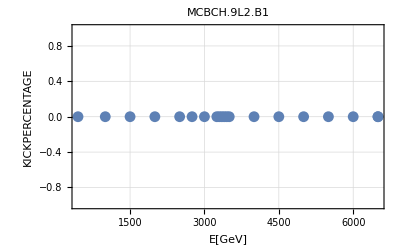
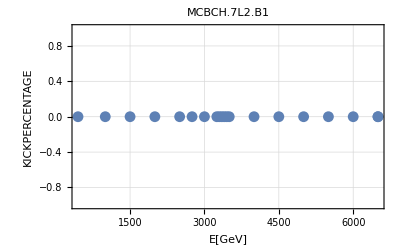
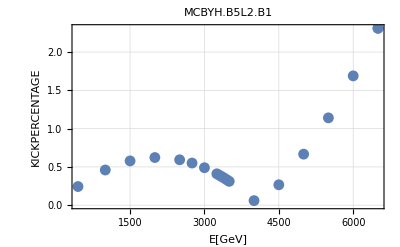
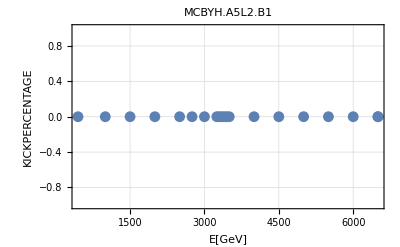
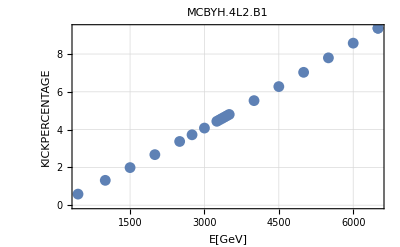
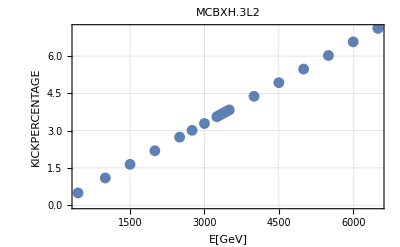
{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
LHCHCorrMAXStrPlot[RampFixedSEPX35mmLinCurrentA2LinSEPreduced[[1]],EnergyTable,"IR2"]
```

### Function

```mathematica
MaxStrListPlot::usage="Returns a set of combined plots of the correcters depending on a given IR and knob (Ex. '*ON_SEP*')"

Options[MaxStrListPlot]= Options[ListPlot];

MaxStrListPlot[scan_,EnergyList_,IR_String,var_String,opts:OptionsPattern[]] :=Module[{datab1,datab2,convdatab1,convdatab2,onsep2list,datab1selected},
datab1=mfsMember[IR/.Get["LHCB1CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER","HKICKER"}]&/@scan;
datab2=mfsMember[IR/.Get["LHCB2CorrectorStrengthFile"/.#],"KEYWORD",{"VKICKER","HKICKER"}]&/@scan;
onsep2list=StringSplit@MADInputLines[{madLHCOpticsSetup[]},{StringDrop[var,-1]<>StringTake[IR,-1]<>"*"}][[9;;-2]];
convdatab1=Select[mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","HKICK","KICKNAMES"}],MemberQ[ToUpperCase[onsep2list[[All,1]]],#[[5,1]]]&]/.{n_,x_,y_,v_,name_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab1;
convdatab2=Select[mfsRow[#,{"NAME","KICKPERCENTMIN","KICKPERCENTMAX","HKICK","KICKNAMES"}],MemberQ[ToUpperCase[onsep2list[[All,1]]],#[[5,1]]]&]/.{n_,x_,y_,v_,name_}:>If[Abs[x]>Abs[y],{n,Abs[y],v},{n,Abs[x],v}]&/@datab2;

Flatten[{ListPlot[Transpose[{EnergyList,Flatten[#/.{x_,y_,z_}:>{y},1]}]&/@Transpose[convdatab1],PlotLegends->{#[[2,1]]&/@Transpose[convdatab1]},Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None},PlotLabel->"BEAM 1 "<>StringDrop[var,-1]<>StringTake["IR2",-1]<>"*",opts],
ListPlot[Transpose[{EnergyList,Flatten[#/.{x_,y_,z_}:>{y},1]}]&/@Transpose[convdatab2],PlotLegends->{#[[2,1]]&/@Transpose[convdatab2]},Frame->{True,True,False,False},GridLines->Automatic,PlotRange->All,FrameLabel->{"E[GeV]","KICKPERCENTAGE",None,None},PlotLabel->"BEAM 2 "<>StringDrop[var,-1]<>StringTake["IR2",-1]<>"*",opts]},1]
]
```

Returns a set of combined plots of the correcters depending on a given IR and knob (Ex. '*ON_SEP*')

## Quadrupole Strength Plots

recheck for squeeze after adding energy dependence

### Function definition : LHCQuadMAXStrPlot

```mathematica
LHCQuadMAXStrPlot::usage="LHCQuadMAXStrPlot[SqueezeBeamProcess,beam,IR] returns a plot of the strength used by the quadrupoles at the given IR expressed in percentage."
Options[LHCQuadMAXStrPlot]=Flatten[{keyvalparameter->"STEP",Options[ListLinePlot]}];
LHCQuadMAXStrPlot[SqueezeBeamProcess_,beam_Integer,IR_String,opts:OptionsPattern[]] :=Module[{optfn,data,convdata,labels},
optfn = "LHCB"<>ToString[beam]<>"QuadrupoleStrengthFile";
data =IR/.Get[optfn/.#]&/@SqueezeBeamProcess;
If[OptionValue[keyvalparameter]=="STEP",convdata= mfsRow[#,{"K1NAMES","K1PERCENTMIN","K1PERCENTMAX"}]/.{x_,y_,z_}:>If[Abs[y]≥Abs[z],Abs[z],Abs[y]]&/@data,
convdata= mfsRow[#,{"K1NAMES","K1PERCENTMIN","K1PERCENTMAX"}]/.{x_,y_,z_}:>If[Abs[y]≥Abs[z],{mfsKeyValue[#,OptionValue[keyvalparameter]],Abs[z]},{mfsKeyValue[#,OptionValue[keyvalparameter]],Abs[y]}]&/@data];
labels=Flatten[mfsRow[#,{"K1NAMES"}]]&/@data;

ListLinePlot[Transpose[convdata],PlotLegends->Placed[labels[[1]],Below],Frame->{True,True,False,False},FrameLabel->{Style["Squeeze Step",16],Style["Percentage",16]},AxesOrigin->{1,0},ImageSize->Large,PlotLabel->Style["Quadrupole Strengths at " <> IR,16],FilterRules[{opts},Options[ListLinePlot]]]
]
```

LHCQuadMAXStrPlot[SqueezeBeamProcess,beam,IR] returns a plot of the strength used by the quadrupoles at the given IR expressed in percentage.

### Function test : LHCQuadMAXStrPlot

```mathematica
LHCQuadMAXStrPlot[LHCBeamProcessSqueezeSequence[[1;;4]],1,"IR2"]
```

-Graphics-

## Beta

```mathematica
?mfs*Plot*
```

mfsOpticsClassicBeamLinePlot[opt] returns a plot of the beta-functions and dispersions, together with a BeamLineGraphics of the layout, contained in the mfs optics opt.  It has options of itw own and can also be controlled by setting options of BeamLineGraphic.

```mathematica
mfsOpticsClassicPlot[]
```

```mathematica
Convert[207.976652071`12.AMU,GeV/c^2]*SpeedOfLight^2/GeV
```

193.729

```mathematica
dpPb::usage="dpPb[δm,δQ] returns the fractional rigidity change of a Pb208 nucleus when it's mass changes by δm and it's charge changes by δQ.";
dpPb[dm_,dQ_]:=ToFundamentalSI[N[(1+dm/mPb)/(1+dQ/Q)-1/.{mPb->(193.72917484892244 GeV)/c^2,A->208,Q->82}]]
```

```mathematica
Options[LHCBeamBFPPOptics]=Flatten[{"SPECIES1"->"PROTON","SPECIES2"->"PROTON",
"ENERGY1"->450, "ENERGY2"->450,"EXN1"->3.75 × 10^-6,"EYN1"->3.75 × 10^-6,"EXN2"->3.75 × 10^-6,"EYN2"->3.75 × 10^-6,"KBUNCH1"->2808,"KBUNCH2"->2808,"NPART1"-> 1.4 × 10^11,"NPART2"-> 1.4 × 10^11, "ET1"->0.000034394400000000004, "SIGE1"->3.06 ×10^-4,"SIGT1"->11.24×10^-2,"ET2"->0.000034394400000000004, "SIGE2"->3.06 ×10^-4,"SIGT2"->11.24×10^-2,optRange->MADfull[],
Options[madLHCOpticsSetup]
}
];

LHCBeamBFPPOptics[opts:OptionsPattern[]]:=Module[{madrunningsetup,bbdir=FileNameTimeStamped["LHCBFPPOptics"],knobfn,madtwissb1,madtwissb2,optfn1,optfn2,optrange,madfn,moufn},

madfn=FileNameJoin[{bbdir,"BFPP.madx"}];
moufn=FileNameJoin[{bbdir,"BFPP.mou"}];
knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
optrange = OptionValue[optRange];


If[FilterRules[{opts},optRange]≠{},
madrunningsetup = {madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],MADuse["LHCB1"],madtwissb1,	MADuse["LHCB2"],madtwissb2}/.{madtwissb1->MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADrange[optrange]},Initial/.FilterRules[{opts},Initial]],madtwissb2->MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADrange[optrange]},Initial/.FilterRules[{opts},Initial]]
}
,
madrunningsetup = {madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],MADuse["LHCB1"],madtwissb1,	MADuse["LHCB2"],madtwissb2}/.{madtwissb1->MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},Initial/.FilterRules[{opts},Initial]],madtwissb2->MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},Initial/.FilterRules[{opts},Initial]]
}
];

Export[moufn,runMAD[madrunningsetup,runMADTemporaryInputFile->madfn],"Lines"];
tfsRead[optfn1]
]
```

```mathematica
BFPPoptics[dp_,init_List]:=Module[{fnstem=FileNameTimeStamped["BFPPbeam"],optfn,madfn,moufn},
optfn=fnstem<>".tfs";madfn=fnstem<>".madx";moufn=fnstem<>".mou";
Export[moufn,runMAD[
{madLHCOptics[],MADuse["LHCB1"],
MADtwiss[optfn,"LHCB1",MADtwissColumns["LHCtwiss"],
{MADrange[LHCModule["IR5DSR.B1"]]},Flatten[{"DELTAP"->dp,init}]]},
runMADTemporaryInputFile->madfn
],"Lines"];
tfsRead[optfn]
]
```

```mathematica
Options[LHCBeamBFPPOptics]=Flatten[{"SPECIES1"->"PROTON","SPECIES2"->"PROTON",
"ENERGY1"->450, "ENERGY2"->450,"EXN1"->3.75 × 10^-6,"EYN1"->3.75 × 10^-6,"EXN2"->3.75 × 10^-6,"EYN2"->3.75 × 10^-6,"KBUNCH1"->2808,"KBUNCH2"->2808,"NPART1"-> 1.4 × 10^11,"NPART2"-> 1.4 × 10^11, "ET1"->0.000034394400000000004, "SIGE1"->3.06 ×10^-4,"SIGT1"->11.24×10^-2,"ET2"->0.000034394400000000004, "SIGE2"->3.06 ×10^-4,"SIGT2"->11.24×10^-2,"BV1"->1,"BV2"->-1,optRange->MADfull[],
Options[madLHCOpticsSetup]
}
];

LHCBeamBFPPOptics[opts:OptionsPattern[]]:=Module[
{bbdir=FileNameTimeStamped["LHCBFPPOptics"],
BeamProcessOptionsfn,madfn,optfn1,optfn2,moufn,opt1,opt2,madrunningsetup,madtwissb1,madtwissb2,
ips={"IP1","IP2","IP5","IP8"},corr1,corr2,corrfn1,corrfn2,quad1,quad2,quadfn1,quadfn2,
bbopt1,bbopt2,bboptfn1,bboptfn2,moptfn1,moptfn2,ap1,ap2,apfn1,apfn2,val,valfn,knobfn},

CreateDirectory[bbdir];
BeamProcessOptionsfn=FileNameJoin[{bbdir,"BeamProcessOptions.m"}];
madfn=FileNameJoin[{bbdir,"Optics.madx"}];
moufn=FileNameJoin[{bbdir,"Optics.mou"}];
optfn1=FileNameJoin[{bbdir,"LHCB1-Optics.tfs"}];
optfn2=FileNameJoin[{bbdir,"LHCB2-Optics.tfs"}];
moptfn1=FileNameJoin[{bbdir,"LHCB1-Optics.m"}];
moptfn2=FileNameJoin[{bbdir,"LHCB2-Optics.m"}];
apfn1=FileNameJoin[{bbdir,"LHCB1-Aperture.m"}];
apfn2=FileNameJoin[{bbdir,"LHCB2-Aperture.m"}];
valfn=FileNameJoin[{bbdir,"LHCBeamBeamOptics.m"}];
     knobfn=FileNameJoin[{bbdir,"OpticsKnobs.str"}];

If[FilterRules[{opts},OptionValue[optRange]]≠{},
madrunningsetup = {madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],MADuse["LHCB1"],madtwissb1,	MADuse["LHCB2"],madtwissb2}/.{madtwissb1->MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADrange[OptionValue[optRange]]},Initial/.FilterRules[{opts},Initial]],madtwissb2->MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADrange[OptionValue[optRange]]},Initial/.FilterRules[{opts},Initial]]
}
,
madrunningsetup = {madLHCOpticsSetup[FilterRules[{opts},Options[madLHCOpticsSetup]]],
	MADtag["MADSow",{"VALUE,"<>"ON_X2"}],
	MADSave[knobfn,{"ON_A2","ON_A8","ON_O1","ON_O2","ON_O5","ON_O8","ON_SEP1","ON_SEP2","ON_SEP5","ON_SEP8","ON_X1","ON_X2","ON_X5","ON_X8"}],MADuse["LHCB1"],madtwissb1,	MADuse["LHCB2"],madtwissb2}/.{madtwissb1->MADtwiss[optfn1,"LHCB1",MADtwissColumns["LHCtwiss"],{MADfull[]},Initial/.FilterRules[{opts},Initial]],madtwissb2->MADtwiss[optfn2,"LHCB2",MADtwissColumns["LHCtwiss"],{MADfull[]},Initial/.FilterRules[{opts},Initial]]
}
];
(*Compute optics*)
Export[moufn,
	runMAD[madrunningsetup
	,runMADTemporaryInputFile->madfn],"Lines"];

(* save the optics as .m to avoid larger and slower TFS reads *)
opt1=tfsRead[optfn1];opt2=tfsRead[optfn2];
Put[opt1,moptfn1];
Put[opt2,moptfn2];


(*Save apertures for each IR*)
ap1={
"IR1"->LHCIRAperture["LHCB1","IP1"],
	"IR2"->LHCIRAperture["LHCB1","IP2"],
"IR5"->LHCIRAperture["LHCB1","IP5"],
	"IR8"->LHCIRAperture["LHCB1","IP8"]};
Put[ap1,apfn1];

ap2={
"IR1"->LHCIRAperture["LHCB2","IP1"],
"IR2"->LHCIRAperture["LHCB2","IP2"],
"IR5"->LHCIRAperture["LHCB2","IP5"],
"IR8"->LHCIRAperture["LHCB2","IP8"]};
Put[ap2,apfn2];

(*Saving the BeamProcess for later reference*)
Put[opts,BeamProcessOptionsfn];
(*Assemble list of rules pointing to all information and return it*)
val={"Computer"->{$MachineName,$MachineDomain},"ResultsDirectoryPath"->workDir,"ResultsDirectory"->bbdir,"Date"->Date[],
"IPs"->ips,
"MADfile"->madfn,
"MADXTerminalOutputFile"->moufn,
"LHCB1OpticsFile"->moptfn1,
"LHCB2OpticsFile"->moptfn2,
"LHCB1OpticsTFSFile"->optfn1,
"LHCB2OpticsTFSFile"->optfn2,
	   "LHCB1ApertureFile"->apfn1,
	   "LHCB2ApertureFile"->apfn2,
	   "LHCOpticsKnobsFile"->knobfn,
(*"LHCBeamBeamOpticsOptions"->Flatten[{opts}],*)
"BeamProcessOptions"->BeamProcessOptionsfn,
"madLHCOpticsSetupOptionsRestricted"->FilterRules[{opts},Complement[Options[madLHCOpticsSetup],FilterRules[Options[madLHCOpticsSetup],madLHCOpticsEpilog]]]};
Put[val,valfn]; (* save this in a file too, before returning it as the value of this function *)
val
]
```